This is an ancillary file of the paper “Correlation functions of determinant operators in conformal fishnet theory” by Omar Shahpo and Edoardo Vescovi. It contains the last author’s code for the effective theory, which perturbatively computes correlators of determinant and multi-trace operators in the three-coupling double scaling limit of γ-deformed twisted 𝒩=4  SYM theory in four dimensions (a.k.a.  χCFT_4)  in planar limit.

You have to:
- start a new kernel,
- run all definitions  in “Initialization”,
- input the chosen correlator in “Effective theory”, run the  code that computes it at a chosen perturbative order and the read the output.

You can optionally:
- set the couplings (ξ1,ξ2,ξ3,α1,α2,α3) to specific values to study limits of the theory,
- compare the output to a selection of results in “Examples”.

# Initialization

This section contains the functions used in section “Effective theory”. Run it all on a new kernel.

## Miscellanea

This sub-section contains various definitions. Many symbols are self-explanatory, while few are explained in section “Effective theory”.

Hermitian auxiliary matrix ρ_ij (i,j=1,...,m) with zeros on the diagonal and its inverse, both in terms of the independent real and imaginary parts Re(ρ_ij) and Im(ρ_ij) with i≤j.

```mathematica
ρ[i_,j_]:=If[i==j,0,If[i<j,ρR[i,j]+ⅈ ρI[i,j],ρR[j,i]-ⅈ ρI[j,i]]]
ρhatinv[i_,j_]:=Inverse[Table[sqrtd[Min[m,n],Max[m,n]]ρ[m,n],{m,4},{n,4}]][[i,j]]
```

R-symmetry product of polarization vectors

```mathematica
RProduct[ϕϕ1_,ϕϕ2_]:=If[MemberQ[{ϕ1 OverBar[ϕ1],ϕ2 OverBar[ϕ2],ϕ3 OverBar[ϕ3],ψ1 OverBar[ψ1],ψ2 OverBar[ψ2],ψ3 OverBar[ψ3]},ϕϕ1 ϕϕ2],1,0]
```

Free Wick contraction of scalars ((ϕ_k)^i_1)_j_1(x) and ((ϕ_k^†)^i_2)_j_2(x) (with scalar-type index k=1,2,3 and gauge index i,j=1,...N) with gauge indices δ_(i_1 j_2)δ_(i_2 j_1) omitted in result

```mathematica
propagatorScalarStandard[Subscript[ϕ1_[x1_], i1_,j1_],Subscript[ϕ2_[x2_], i2_,j2_]]:=1/N II[{x1,x2}]RProduct[ϕ1,ϕ2]graphSpacetime[{x1<->x2}]
```

Free Wick contraction of spinors ((ψ_(α,k))^i_1)_j_1(x) and ((((ψ̄)_k)^(α̇))^i_2)_j_2(x) (with spinor-type index k=1,2,3 and gauge index i,j=1,...N) with gauge indices δ_(i_1 j_2)δ_(i_2 j_1) omitted in result

```mathematica
propagatorSpinorStandard[Subscript[OverBar[ψ1_][x1_], i1_,j1_,αd_],Subscript[ψ1_[x2_], i2_,j2_,α_]]:=ⅈ/N Subscript[σttDII[{x1,x2}], α,αd] RProduct[OverBar[ψ1],ψ1]graphSpacetime[{x1<->x2}]
propagatorSpinorStandard[Subscript[ψ1_[x2_], i2_,j2_,α_],Subscript[OverBar[ψ1_][x1_], i1_,j1_,αd_]]:=-propagatorSpinorStandard[Subscript[OverBar[ψ1][x1], i1,j1,αd],Subscript[ψ1[x2], i2,j2,α]]

propagatorSpinorStandard[Subscript[ψ1_[x1_], i1_,j1_,α1_],Subscript[ψ2_[x2_], i2_,j2_,α2_]]:=0

propagatorSpinorStandard[Subscript[OverBar[ψ1_][x1_], i1_,j1_,αd1_],Subscript[Subscript[OverBar[ψ2_], _][x2_], i2_,j2_,αd2_]]:=0
```

Free Wick contraction of auxiliary fermions (χ^i)_a and (χ̄)_(i a) (with fermion-type index i=1,...,m and gauge index a=1,...,N) with gauge indices omitted

```mathematica
propagatorAuxFermionStandard[χ̄[i_],χ[j_]]:=-ⅈ/2 ρhatinv[{i,j}]
propagatorAuxFermionStandard[χ[j_],χ̄[i_]]:=-propagatorAuxFermionStandard[χ̄[i],χ[j]]
propagatorAuxFermionStandard[χ[i_],χ[j_]]:=0
propagatorAuxFermionStandard[χ̄[i_],χ̄[j_]]:=0
```

Set coupling constants of biscalar theory or χCFT_4

```mathematica
setTheory[x_]:=Switch[x,"biscalar",Flatten[{{ξ1->0}, {ξ2->0}, {ξ3->ξ}, {α1a->α1}, {α1b->α1}, {α1c->0}, {α2a->α2}, {α2b->0}, {α2c->0}, {α3a->α3}, {α3b->0}, {α3c->0}}],"biscalarSingleTrace",Flatten[{{ξ1->0}, {ξ2->0}, {ξ3->ξ}, {α1a->0}, {α1b->0}, {α1c->0}, {α2a->0}, {α2b->0}, {α2c->0}, {α3a->0}, {α3b->0}, {α3c->0}}],_,Flatten[{{α1a->α1}, {α1b->α1}, {α1c->α1}, {α2a->α2}, {α2b->α2}, {α2c->α2}, {α3a->α3}, {α3b->α3}, {α3c->α3}}]];
```

Value of the coupling constants at the conformal point of the theory
Note: the theory depends on the square of α_1,α_2 and α_3.

```mathematica
fixedPoint={α3->ⅈ ξ3};
fixedPointBiscalar={α2->ⅈ ξ,α3->ⅈ ξ};
```

## contractionScalar

Compute all free Wick contraction of a product of scalars.

Input:
- list is the list of scalars,
- pref is the numerical prefactor of the product.

Output:
- graphSpacetime keeps track of the diagrams’ topology.

Note:
- the product of scalars does not carry free gauge indices (SU(N)-singlet),
- we assume the gauge group to be U(N) and not SU(N) in order to simplify the Wick contractions and speed up the code.

```mathematica
contractionScalar[pref_,list_]:=
Module[{output},

If[pref===0 || Length[list]==0,

output=pref;

,{

output=0;
For[ii=2,ii≤Length[list],ii++,{
bucket={list[[1]]/.{Subscript[ϕϕ_[x_], i_,j_]:>i},list[[1]]/.{Subscript[ϕϕ_[x_], i_,j_]:>j},list[[ii]]/.{Subscript[ϕϕ_[x_], i_,j_]:>i},list[[ii]]/.{Subscript[ϕϕ_[x_], i_,j_]:>j}};
bucket2=contractionscalar[pref  propagatorScalarStandard[list[[1]],list[[ii]]],Drop[Drop[list,{ii}],1]];

bucket2=If[bucket[[1]]===bucket[[4]],bucket2/.{contractionscalar[a_,b_]:>contractionscalar[N a,b]},bucket2/.{bucket[[1]]->bucket[[4]]}];
bucket=bucket/.{bucket[[1]]->bucket[[4]]};

bucket2=If[bucket[[2]]===bucket[[3]],bucket2/.{contractionscalar[a_,b_]:>contractionscalar[N a,b]},bucket2/.{bucket[[2]]->bucket[[3]]}];

output=output+bucket2;

Clear[bucket,bucket2];
}];

}];

output/.{contractionscalar->contractionScalar}

]
```

Example: calculate  <5tr(Φ_1(x_1) Φ_1(x_2) (Φ̄)_1(x_3)(Φ̄)_1(x_4))> in free theory

```mathematica
contractionScalar[5,{Subscript[ϕ1[Subscript[x, 1]], o[1],o[2]],Subscript[ϕ1[Subscript[x, 2]], o[2],o[3]],Subscript[OverBar[ϕ1][Subscript[x, 3]], o[3],o[4]],Subscript[OverBar[ϕ1][Subscript[x, 4]], o[4],o[1]]}]
```

5 N graphSpacetime[{x_1<->x_4}] graphSpacetime[{x_2<->x_3}] II[{x_1,x_4}] II[{x_2,x_3}]+(5 graphSpacetime[{x_1<->x_3}] graphSpacetime[{x_2<->x_4}] II[{x_1,x_3}] II[{x_2,x_4}])/N

## contractionSpinor

Compute all free Wick contraction of a product of spinors.

See contractionScalar for description.

```mathematica
contractionSpinor[pref_,list_]:=
Module[{output},

If[pref===0 || Length[list]==0,

output=pref;

,{

output=0;
For[ii=2,ii≤Length[list],ii++,{
bucket={list[[1]]/.{Subscript[ψψ_[x_], i_,j_,α_]:>i},list[[1]]/.{Subscript[ψψ_[x_], i_,j_,α_]:>j},list[[ii]]/.{Subscript[ψψ_[x_], i_,j_,α_]:>i},list[[ii]]/.{Subscript[ψψ_[x_], i_,j_,α_]:>j}};
bucket2=contractionspinor[(-1)^ii pref  propagatorSpinorStandard[list[[1]],list[[ii]]],Drop[Drop[list,{ii}],1]];

bucket2=If[bucket[[1]]===bucket[[4]],bucket2/.{contractionspinor[a_,b_]:>contractionspinor[N a,b]},bucket2/.{bucket[[1]]->bucket[[4]]}];
bucket=bucket/.{bucket[[1]]->bucket[[4]]};

bucket2=If[bucket[[2]]===bucket[[3]],bucket2/.{contractionspinor[a_,b_]:>contractionspinor[N a,b]},bucket2/.{bucket[[2]]->bucket[[3]]}];

output=output+bucket2;

Clear[bucket,bucket2];
}];

}];

output/.{contractionspinor->contractionSpinor}

]
```

Example: calculate  <5tr(ψ_(1,α)(x_1) ψ_(1,β)(x_2) ((ψ̄)_1)^(α̇)(x_3)((ψ̄)_1)^(β̇)(x_4))> in free theory

```mathematica
contractionSpinor[5,{Subscript[ψ1[Subscript[x, 1]], o[1],o[2],α],Subscript[ψ1[Subscript[x, 2]], o[2],o[3],β],Subscript[OverBar[ψ1][Subscript[x, 3]], o[3],o[4],α̇],Subscript[OverBar[ψ1][Subscript[x, 4]], o[4],o[1],β̇]}]
```

-5 N graphSpacetime[{x_3<->x_2}] graphSpacetime[{x_4<->x_1}] σttDII[{x_3,x_2}]_(β,α̇) σttDII[{x_4,x_1}]_(α,β̇)+(5 graphSpacetime[{x_3<->x_1}] graphSpacetime[{x_4<->x_2}] σttDII[{x_3,x_1}]_(α,α̇) σttDII[{x_4,x_2}]_(β,β̇))/N

## contractionScalarAndTurnIntoS

This is a variant of contractionScalar. It replaces scalars with matrices S in all possible ways, then operates free Wick contractions among  the remaining scalars.

Input:
- list1, list2, list3, list4, list5, list6 are the lists of scalars Φ_1,(Φ̄)_1,Φ_2,(Φ̄)_2,Φ_3,(Φ̄)_3 respectively,
- pref is the numerical prefactor of the product.

Output:
- contractionSS contains a prefactor and a product of matrices S.

Note:
- we discard negative powers of N in the final prefactor for N→∞.

```mathematica
(* some scalars contract, the others turns into S *)
contractionScalarAndTurnIntoS[pref_,list1_,list2_,list3_,list4_,list5_,list6_]:=
Module[{output},

(* lenghts *)
lengths12={Length[list1],Length[list2]};
lengths34={Length[list3],Length[list4]};
lengths56={Length[list5],Length[list6]};

(* cases *)

If[Length[list1]≤Length[list2] && Length[list3]≤Length[list4]&&Length[list5]≤Length[list6],
{output=0;
For[i=0,i≤Length[list1],i++,
For[j=0,j≤Length[list3],j++,
For[k=0,k≤Length[list5],k++,{
subsets1=Subsets[list1,{i}];
subsets2=Subsets[list2,{i+Length[list2]-Length[list1]}];
subsets3=Subsets[list3,{j}];
subsets4=Subsets[list4,{j+Length[list4]-Length[list3]}];
subsets5=Subsets[list5,{k}];
subsets6=Subsets[list6,{k+Length[list6]-Length[list5]}];
output=output+Sum[contractionScalar[contractionSS[pref,Join[subsets1[[j1]],subsets2[[j2]],subsets3[[j3]],subsets4[[j4]],subsets5[[j5]],subsets6[[j6]]]/.{Subscript[ϕ_[x__], i_,j_]:>Subscript[S[x,ϕ], i,j]}],Join[Complement[list1,subsets1[[j1]]],Complement[list2,subsets2[[j2]]],Complement[list3,subsets3[[j3]]],Complement[list4,subsets4[[j4]]],Complement[list5,subsets5[[j5]]],Complement[list6,subsets6[[j6]]]]],{j1,Length[subsets1]},{j2,Length[subsets2]},{j3,Length[subsets3]},{j4,Length[subsets4]},{j5,Length[subsets5]},{j6,Length[subsets6]}];
}]]];
}];

If[Length[list1]>Length[list2] ,
output=contractionScalarAndTurnIntoS[pref,list2,list1,list3,list4,list5,list6];
];

If[Length[list3]>Length[list4],
output=contractionScalarAndTurnIntoS[pref,list1,list2,list4,list3,list5,list6];
];

If[Length[list5]>Length[list6],
output=contractionScalarAndTurnIntoS[pref,list1,list2,list3,list4,list6,list5];
];


output=output/.{S̄->S}//.{a_ contractionSS[b_,c_]:>contractionSS[a b,c]}/.{contractionSS[a_,b_]:>contractionSS[Series[a,{N,∞,0}]//Normal,b]}/.{contractionSS[0,b_]:>0};

output

]
```

Example: calculate  <5N tr(Φ_1(x_1) Φ_2(x_2) (Φ̄)_1(x_3)(Φ̄)_2(x_4))> in free theory

```mathematica
contractionScalarAndTurnIntoS[5N,{Subscript[ϕ1[Subscript[x, 1]], o[1],o[2]]},{Subscript[OverBar[ϕ1][Subscript[x, 3]], o[3],o[4]]},{Subscript[ϕ2[Subscript[x, 2]], o[2],o[3]]},{Subscript[OverBar[ϕ2][Subscript[x, 4]], o[4],o[1]]},{},{}]
```

contractionSS[5 N,{S[x_1,ϕ1]_(o[1],o[2]),S[x_3,OverBar[ϕ1]]_(o[3],o[4]),S[x_2,ϕ2]_(o[2],o[3]),S[x_4,OverBar[ϕ2]]_(o[4],o[1])}]+contractionSS[5 graphSpacetime[{x_1<->x_3}] II[{x_1,x_3}],{S[x_2,ϕ2]_(o[3],o[3]),S[x_4,OverBar[ϕ2]]_(o[4],o[4])}]+contractionSS[5 graphSpacetime[{x_2<->x_4}] II[{x_2,x_4}],{S[x_1,ϕ1]_(o[1],o[1]),S[x_3,OverBar[ϕ1]]_(o[4],o[4])}]+contractionSS[5 graphSpacetime[{x_1<->x_3}] graphSpacetime[{x_2<->x_4}] II[{x_1,x_3}] II[{x_2,x_4}],{}]

Example: calculate  the same, divided by N

```mathematica
contractionScalarAndTurnIntoS[5,{Subscript[ϕ1[Subscript[x, 1]], o[1],o[2]]},{Subscript[OverBar[ϕ1][Subscript[x, 3]], o[3],o[4]]},{Subscript[ϕ2[Subscript[x, 2]], o[2],o[3]]},{Subscript[OverBar[ϕ2][Subscript[x, 4]], o[4],o[1]]},{},{}]
```

contractionSS[5,{S[x_1,ϕ1]_(o[1],o[2]),S[x_3,OverBar[ϕ1]]_(o[3],o[4]),S[x_2,ϕ2]_(o[2],o[3]),S[x_4,OverBar[ϕ2]]_(o[4],o[1])}]

## contractionAuxFermion

Compute all free Wick contraction of a product of auxiliary fermions.

Input:
- list is the list of auxiliary fermions,
- pref is the numerical prefactor of the product.

Output:
- it is returned to contractionS.

Note:
- we discard negative powers of N in the final prefactor for N→∞.

```mathematica
(* keep only terms in (pref) * (result of conctractions) that are O(N^0) *)

contractionAuxFermion[pref_,list_]:=
Module[{output},

If[Length[list]==0,

output=Normal[Series[pref,{N,∞,0}]],

If[Normal[Series[(pref N^(Length[list]/2))/N,{N,∞,0}]]===0,{

(* prefactor and remaining contractions are O(N^0) at best, so we do the N-leading contraction in one shot *)
orderedlist=SortBy[list,(#/.{Subscript[χ_[i_], j_]:>j})&];
(* orderedlist = {Subscript[χ[i], i1],Subscript[χ̄[j], i1],...} *)
output=(-1)^((Signature[list]+Signature[orderedlist])/2+1)Normal[Series[pref N^(Length[list]/2),{N,∞,0}]]Product[propagatorAuxFermionStandard[orderedlist[[2ii-1]]/.{Subscript[χ_[x_], i_]:>χ[x]},orderedlist[[2ii]]/.{Subscript[χ_[x_], i_]:>χ[x]}],{ii,Length[list]/2}];
If[Signature[list]Signature[orderedlist]==0,Print["Assumption failed in contractionAuxFermion."]];

},{

(* prefactor and remaining contractions are O(N^(>0)), so we do all contractions recursively *)
output=0;

For[ii=2,ii≤Length[list],ii++,{
bucket={list[[1]]/.{Subscript[χ_[x_], i_]:>i},list[[ii]]/.{Subscript[χ_[x_], i_]:>i}};
bucket2=(-1)^ii propagatorAuxFermionStandard[list[[1]]/.{Subscript[χ_[x_], i_]:>χ[x]},list[[ii]]/.{Subscript[χ_[x_], i_]:>χ[x]}]contractionauxfermion[pref,Drop[Drop[list,{ii}],1]];
output=output+If[bucket[[1]]===bucket[[2]],bucket2/.{contractionauxfermion[a_,b_]:>contractionauxfermion[N a,b]},bucket2/.{bucket[[1]]->bucket[[2]]}];

}];


}];

];

output/.{contractionauxfermion->contractionAuxFermion}

];
```

## contractionS

Write a product of matrices S as a product of auxiliary fermions and compute all Wick contractions.

Input:
- pref is the numerical prefactor of the product,
- list is the list of matrices S,
- numberDets is the size of the matrix ρ, as well as the number of determinants in the correlator,
- ρhatinvExplicit is the inverse of the matrix ρ̂.

Output:
- contractionSS contains a prefactor and a product of matrices S.

Note:
- we discard negative powers of N in the final prefactor for N→∞.

```mathematica
contractionS[pref_,list_,numberDets_,ρhatinvExplicit_]:=
Module[{output},

If[Length[list]==0,

output=Normal[Series[pref,{N,∞,0}]]//Simplify

,{

listpoints=list/.{Subscript[S[x__,ϕ_], i_,j_]:>x};
listscalars=list/.{Subscript[S[x__,ϕ_], i_,j_]:>ϕ};
Clear[ii];

output=Table[{list[[i]]/.{Subscript[S[x__,ϕ_], j_,k_]:>Subscript[χ[p[i]], j]},list[[i]]/.{Subscript[S[x__,ϕ_], j_,k_]:>Subscript[χ̄[p[i]], k]}},{i,Length[list]}]//Flatten;
output=sum[contractionAuxFermion[pref(-1/(√2 N))^Length[list],output]graphSpacetime[Table[Subscript[x, p[ii]]<->listpoints[[ii]],{ii,Length[listpoints]}]]Product[II[{Subscript[x, p[ii]],listpoints[[ii]]}]Y[p[ii],listscalars[[ii]]],{ii,Length[list]}],Sequence@@Table[{p[ii],numberDets},{ii,Length[list]}]];
output=output/.sum->Sum/.{ρhatinv[list1_]:>ρhatinvExplicit[[Sequence@@list1]]};
output=Normal[Series[output,{N,∞,0}]]//Simplify;
}
];

output

]
```

Example: calculate  <tr(S^Φ_1(x_1)S^Φ_2(x_2)S^((Φ̄)_1)(x_3)S^((Φ̄)_2)(x_4))>_χ  at fixed  (ρ̂)^-1=(0 | 2+3ⅈ
2-3ⅈ | 0), see example in section “contractionScalarAndTurnIntoS”

```mathematica
contractionS[5,{Subscript[S[Subscript[x, 1],ϕ1], o[1],o[2]],Subscript[S[Subscript[x, 3],OverBar[ϕ1]], o[3],o[4]],Subscript[S[Subscript[x, 2],ϕ2], o[2],o[3]],Subscript[S[Subscript[x, 4],OverBar[ϕ2]], o[4],o[1]]},2,({{0, 2+3ⅈ}, {2-3ⅈ, 0}})]
```

-845/64 (graphSpacetime[{x_2<->x_1,x_2<->x_3,x_1<->x_2,x_1<->x_4}] II[{x_1,x_2}] II[{x_1,x_4}] II[{x_2,x_1}] II[{x_2,x_3}] Y[1,ϕ2] Y[1,OverBar[ϕ2]] Y[2,ϕ1] Y[2,OverBar[ϕ1]]+graphSpacetime[{x_1<->x_1,x_1<->x_3,x_2<->x_2,x_2<->x_4}] II[{x_1,x_1}] II[{x_1,x_3}] II[{x_2,x_2}] II[{x_2,x_4}] Y[1,ϕ1] Y[1,OverBar[ϕ1]] Y[2,ϕ2] Y[2,OverBar[ϕ2]])

## vertices

Expand the weight of the path integral e^S_int into a sum of multi-trace operators at small coupling.

Input:
- V  is the number of vertices.

Output:
- contractionFieldsHold contains a prefactor and a product of fields.

Note:
- we hardcoded a large offset for gauge indices, irrelevant for any realistic number of fields in the correlator.

```mathematica
vertices[V_]:=Module[{output},

If[V==0,output=1,{

indexgauge=1001; (* hardcoded offset *)
output=0;

For[V1=0,V1≤V,V1++,
For[V2=0,V2≤V-V1,V2++,
For[V3=0,V3≤V-V1-V2,V3++,
For[V4=0,V4≤V-V1-V2-V3,V4++,
For[V5=0,V5≤V-V1-V2-V3-V4,V5++,
For[V6=0,V6≤V-V1-V2-V3-V4-V5,V6++,
For[V7=0,V7≤V-V1-V2-V3-V4-V5-V6,V7++,
For[V8=0,V8≤V-V1-V2-V3-V4-V5-V6-V7,V8++,
For[V9=0,V9≤V-V1-V2-V3-V4-V5-V6-V7-V8,V9++,
For[V10=0,V10≤V-V1-V2-V3-V4-V5-V6-V7-V8-V9,V10++,
For[V11=0,V11≤V-V1-V2-V3-V4-V5-V6-V7-V8-V9-V10,V11++,
For[V12=0,V12≤V-V1-V2-V3-V4-V5-V6-V7-V8-V9-V10-V11,V12++,
For[V13=0,V13≤V-V1-V2-V3-V4-V5-V6-V7-V8-V9-V10-V11-V12,V13++,
For[V14=0,V14≤V-V1-V2-V3-V4-V5-V6-V7-V8-V9-V10-V11-V12-V13,V14++,
For[V15=0,V15≤V-V1-V2-V3-V4-V5-V6-V7-V8-V9-V10-V11-V12-V13-V14,V15++,
For[V16=0,V16≤V-V1-V2-V3-V4-V5-V6-V7-V8-V9-V10-V11-V12-V13-V14-V15,V16++,
For[V17=0,V17≤V-V1-V2-V3-V4-V5-V6-V7-V8-V9-V10-V11-V12-V13-V14-V15-V16,V17++,

V18=V-V1-V2-V3-V4-V5-V6-V7-V8-V9-V10-V11-V12-V13-V14-V15-V16-V17;

If[V18<0,Break[]];

tmp=1;
indexpt=1;
indexspinor=1;

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 N ξ1^2,{Subscript[OverBar[ϕ2][x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[OverBar[ϕ3][x[indexpt]], m[1+indexgauge],m[2+indexgauge]],Subscript[ϕ2[x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[ϕ3[x[indexpt]], m[3+indexgauge],m[indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V1];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 N ξ2^2,{Subscript[OverBar[ϕ3][x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[OverBar[ϕ1][x[indexpt]], m[1+indexgauge],m[2+indexgauge]],Subscript[ϕ3[x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[ϕ1[x[indexpt]], m[3+indexgauge],m[indexgauge]]}];

indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V2];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 N ξ3^2,{Subscript[OverBar[ϕ1][x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[OverBar[ϕ2][x[indexpt]], m[1+indexgauge],m[2+indexgauge]],Subscript[ϕ1[x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[ϕ2[x[indexpt]], m[3+indexgauge],m[indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V3];

Do[{
tmp=tmp contractionFieldsHold[4π ⅈ N √(ξ1 ξ2) ϵ[α[indexspinor],β[indexspinor]],{Subscript[ψ2[x[indexpt]], m[indexgauge],m[1+indexgauge],α[indexspinor]],Subscript[ϕ3[x[indexpt]], m[1+indexgauge],m[2+indexgauge]],Subscript[ψ1[x[indexpt]], m[2+indexgauge],m[indexgauge],β[indexspinor]]}];
indexpt=indexpt+1;
indexspinor=indexspinor+1;
indexgauge=indexgauge+4;
},V4];

Do[{
tmp=tmp contractionFieldsHold[4π ⅈ N √(ξ2 ξ3) ϵ[α[indexspinor],β[indexspinor]],{Subscript[ψ3[x[indexpt]], m[indexgauge],m[1+indexgauge],α[indexspinor]],Subscript[ϕ1[x[indexpt]], m[1+indexgauge],m[2+indexgauge]],Subscript[ψ2[x[indexpt]], m[2+indexgauge],m[indexgauge],β[indexspinor]]}];
indexpt=indexpt+1;
indexspinor=indexspinor+1;
indexgauge=indexgauge+4;
},V5];

Do[{
tmp=tmp contractionFieldsHold[4π ⅈ N √(ξ1 ξ3) ϵ[α[indexspinor],β[indexspinor]],{Subscript[ψ1[x[indexpt]], m[indexgauge],m[1+indexgauge],α[indexspinor]],Subscript[ϕ2[x[indexpt]], m[1+indexgauge],m[2+indexgauge]],Subscript[ψ3[x[indexpt]], m[2+indexgauge],m[indexgauge],β[indexspinor]]}];
indexpt=indexpt+1;
indexspinor=indexspinor+1;
indexgauge=indexgauge+4;
},V6];

Do[{
tmp=tmp contractionFieldsHold[4π ⅈ N √(ξ1 ξ2) ϵ[αd[indexspinor],βd[indexspinor]],{Subscript[OverBar[ψ2][x[indexpt]], m[indexgauge],m[1+indexgauge],αd[indexspinor]],Subscript[OverBar[ϕ3][x[indexpt]], m[1+indexgauge],m[2+indexgauge]],Subscript[OverBar[ψ1][x[indexpt]], m[2+indexgauge],m[indexgauge],βd[indexspinor]]}];
indexpt=indexpt+1;
indexspinor=indexspinor+1;
indexgauge=indexgauge+4;
},V7];

Do[{
tmp=tmp contractionFieldsHold[4π ⅈ N √(ξ2 ξ3) ϵ[αd[indexspinor],βd[indexspinor]],{Subscript[OverBar[ψ3][x[indexpt]], m[indexgauge],m[1+indexgauge],αd[indexspinor]],Subscript[OverBar[ϕ1][x[indexpt]], m[1+indexgauge],m[2+indexgauge]],Subscript[OverBar[ψ2][x[indexpt]], m[2+indexgauge],m[indexgauge],βd[indexspinor]]}];
indexpt=indexpt+1;
indexspinor=indexspinor+1;
indexgauge=indexgauge+4;
},V8];

Do[{
tmp=tmp contractionFieldsHold[4π ⅈ N √(ξ1 ξ3) ϵ[αd[indexspinor],βd[indexspinor]],{Subscript[OverBar[ψ1][x[indexpt]], m[indexgauge],m[1+indexgauge],αd[indexspinor]],Subscript[OverBar[ϕ2][x[indexpt]], m[1+indexgauge],m[2+indexgauge]],Subscript[OverBar[ψ3][x[indexpt]], m[2+indexgauge],m[indexgauge],βd[indexspinor]]}];
indexpt=indexpt+1;
indexspinor=indexspinor+1;
indexgauge=indexgauge+4;
},V9];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 α1a^2,{Subscript[ϕ1[x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[ϕ1[x[indexpt]], m[1+indexgauge],m[indexgauge]],Subscript[OverBar[ϕ1][x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[OverBar[ϕ1][x[indexpt]], m[3+indexgauge],m[2+indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V10];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 α1b^2,{Subscript[ϕ2[x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[ϕ2[x[indexpt]], m[1+indexgauge],m[indexgauge]],Subscript[OverBar[ϕ2][x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[OverBar[ϕ2][x[indexpt]], m[3+indexgauge],m[2+indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V11];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 α1c^2,{Subscript[ϕ3[x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[ϕ3[x[indexpt]], m[1+indexgauge],m[indexgauge]],Subscript[OverBar[ϕ3][x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[OverBar[ϕ3][x[indexpt]], m[3+indexgauge],m[2+indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V12];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 α2a^2,{Subscript[ϕ1[x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[OverBar[ϕ2][x[indexpt]], m[1+indexgauge],m[indexgauge]],Subscript[OverBar[ϕ1][x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[ϕ2[x[indexpt]], m[3+indexgauge],m[2+indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V13];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 α2b^2,{Subscript[ϕ2[x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[OverBar[ϕ3][x[indexpt]], m[1+indexgauge],m[indexgauge]],Subscript[OverBar[ϕ2][x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[ϕ3[x[indexpt]], m[3+indexgauge],m[2+indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V14];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 α2c^2,{Subscript[ϕ3[x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[OverBar[ϕ1][x[indexpt]], m[1+indexgauge],m[indexgauge]],Subscript[OverBar[ϕ3][x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[ϕ1[x[indexpt]], m[3+indexgauge],m[2+indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V15];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 α3a^2,{Subscript[ϕ1[x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[ϕ2[x[indexpt]], m[1+indexgauge],m[indexgauge]],Subscript[OverBar[ϕ1][x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[OverBar[ϕ2][x[indexpt]], m[3+indexgauge],m[2+indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V16];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 α3b^2,{Subscript[ϕ2[x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[ϕ3[x[indexpt]], m[1+indexgauge],m[indexgauge]],Subscript[OverBar[ϕ2][x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[OverBar[ϕ3][x[indexpt]], m[3+indexgauge],m[2+indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V17];

Do[{
tmp=tmp contractionFieldsHold[(4π)^2 α3c^2,{Subscript[ϕ3[x[indexpt]], m[indexgauge],m[1+indexgauge]],Subscript[ϕ1[x[indexpt]], m[1+indexgauge],m[indexgauge]],Subscript[OverBar[ϕ3][x[indexpt]], m[2+indexgauge],m[3+indexgauge]],Subscript[OverBar[ϕ1][x[indexpt]], m[3+indexgauge],m[2+indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V18];

output=output+contractionFieldsHold[1/(V1!V2!V3!V4!V5!V6!V7!V8!V9!V10!V11!V12!V13!V14!V15!V16!V17!V18!),{}](tmp/.contractionFieldsHold[x_,y_]:>If[x===0,0,contractionFieldsHold[x,y]]);

]]]]]]]]]]]]]]]]];


}];

output

]
```

Example: select the terms with 1 vertex

```mathematica
vertices[1]//.{contractionFieldsHold[pref1_,list1_]contractionFieldsHold[pref2_,list2_]:>contractionFieldsHold[pref1 pref2,Join[list1,list2]]}
```

contractionFieldsHold[16 π^2 α1a^2,{ϕ1[x[1]]_(m[1033],m[1034]),ϕ1[x[1]]_(m[1034],m[1033]),(OverBar[ϕ1][x[1]])_(m[1035],m[1036]),(OverBar[ϕ1][x[1]])_(m[1036],m[1035])}]+contractionFieldsHold[16 π^2 α1b^2,{ϕ2[x[1]]_(m[1029],m[1030]),ϕ2[x[1]]_(m[1030],m[1029]),(OverBar[ϕ2][x[1]])_(m[1031],m[1032]),(OverBar[ϕ2][x[1]])_(m[1032],m[1031])}]+contractionFieldsHold[16 π^2 α1c^2,{ϕ3[x[1]]_(m[1025],m[1026]),ϕ3[x[1]]_(m[1026],m[1025]),(OverBar[ϕ3][x[1]])_(m[1027],m[1028]),(OverBar[ϕ3][x[1]])_(m[1028],m[1027])}]+contractionFieldsHold[16 π^2 α2a^2,{ϕ1[x[1]]_(m[1021],m[1022]),(OverBar[ϕ2][x[1]])_(m[1022],m[1021]),(OverBar[ϕ1][x[1]])_(m[1023],m[1024]),ϕ2[x[1]]_(m[1024],m[1023])}]+contractionFieldsHold[16 π^2 α2b^2,{ϕ2[x[1]]_(m[1017],m[1018]),(OverBar[ϕ3][x[1]])_(m[1018],m[1017]),(OverBar[ϕ2][x[1]])_(m[1019],m[1020]),ϕ3[x[1]]_(m[1020],m[1019])}]+contractionFieldsHold[16 π^2 α2c^2,{ϕ3[x[1]]_(m[1013],m[1014]),(OverBar[ϕ1][x[1]])_(m[1014],m[1013]),(OverBar[ϕ3][x[1]])_(m[1015],m[1016]),ϕ1[x[1]]_(m[1016],m[1015])}]+contractionFieldsHold[16 π^2 α3a^2,{ϕ1[x[1]]_(m[1009],m[1010]),ϕ2[x[1]]_(m[1010],m[1009]),(OverBar[ϕ1][x[1]])_(m[1011],m[1012]),(OverBar[ϕ2][x[1]])_(m[1012],m[1011])}]+contractionFieldsHold[16 π^2 α3b^2,{ϕ2[x[1]]_(m[1005],m[1006]),ϕ3[x[1]]_(m[1006],m[1005]),(OverBar[ϕ2][x[1]])_(m[1007],m[1008]),(OverBar[ϕ3][x[1]])_(m[1008],m[1007])}]+contractionFieldsHold[16 π^2 α3c^2,{ϕ3[x[1]]_(m[1001],m[1002]),ϕ1[x[1]]_(m[1002],m[1001]),(OverBar[ϕ3][x[1]])_(m[1003],m[1004]),(OverBar[ϕ1][x[1]])_(m[1004],m[1003])}]+contractionFieldsHold[16 N π^2 ξ1^2,{(OverBar[ϕ2][x[1]])_(m[1069],m[1070]),(OverBar[ϕ3][x[1]])_(m[1070],m[1071]),ϕ2[x[1]]_(m[1071],m[1072]),ϕ3[x[1]]_(m[1072],m[1069])}]+contractionFieldsHold[16 N π^2 ξ2^2,{(OverBar[ϕ3][x[1]])_(m[1065],m[1066]),(OverBar[ϕ1][x[1]])_(m[1066],m[1067]),ϕ3[x[1]]_(m[1067],m[1068]),ϕ1[x[1]]_(m[1068],m[1065])}]+contractionFieldsHold[16 N π^2 ξ3^2,{(OverBar[ϕ1][x[1]])_(m[1061],m[1062]),(OverBar[ϕ2][x[1]])_(m[1062],m[1063]),ϕ1[x[1]]_(m[1063],m[1064]),ϕ2[x[1]]_(m[1064],m[1061])}]+contractionFieldsHold[4 ⅈ N π √(ξ1 ξ2) ϵ[α[1],β[1]],{ψ2[x[1]]_(m[1057],m[1058],α[1]),ϕ3[x[1]]_(m[1058],m[1059]),ψ1[x[1]]_(m[1059],m[1057],β[1])}]+contractionFieldsHold[4 ⅈ N π √(ξ1 ξ3) ϵ[α[1],β[1]],{ψ1[x[1]]_(m[1049],m[1050],α[1]),ϕ2[x[1]]_(m[1050],m[1051]),ψ3[x[1]]_(m[1051],m[1049],β[1])}]+contractionFieldsHold[4 ⅈ N π √(ξ2 ξ3) ϵ[α[1],β[1]],{ψ3[x[1]]_(m[1053],m[1054],α[1]),ϕ1[x[1]]_(m[1054],m[1055]),ψ2[x[1]]_(m[1055],m[1053],β[1])}]+contractionFieldsHold[4 ⅈ N π √(ξ1 ξ2) ϵ[αd[1],βd[1]],{(OverBar[ψ2][x[1]])_(m[1045],m[1046],αd[1]),(OverBar[ϕ3][x[1]])_(m[1046],m[1047]),(OverBar[ψ1][x[1]])_(m[1047],m[1045],βd[1])}]+contractionFieldsHold[4 ⅈ N π √(ξ1 ξ3) ϵ[αd[1],βd[1]],{(OverBar[ψ1][x[1]])_(m[1037],m[1038],αd[1]),(OverBar[ϕ2][x[1]])_(m[1038],m[1039]),(OverBar[ψ3][x[1]])_(m[1039],m[1037],βd[1])}]+contractionFieldsHold[4 ⅈ N π √(ξ2 ξ3) ϵ[αd[1],βd[1]],{(OverBar[ψ3][x[1]])_(m[1041],m[1042],αd[1]),(OverBar[ϕ1][x[1]])_(m[1042],m[1043]),(OverBar[ψ2][x[1]])_(m[1043],m[1041],βd[1])}]

# Effective theory

This section calculates correlators involving 0, 2 or 4 determinants and an arbitrary number of multi-trace operators made of any fields. In each sub-section you have to edit the input and run it all.

## Correlators of multi-trace operators

In this sub-section we consider the multi-point correlator  <tr(...)...tr(...)>, normalised by its value in free theory. The dots stand for arbitrary products of fields. The algorithm calculates the integrands of the Feynman diagrams with V vertices in position space.

Input:
- traces is the list of fields in the multi-traces, possibly the empty list, where you have to use  x_3, x_4, ... for the the spacetime points and o[1],o[2],... for the gauge indices,
- V  is the number of vertices,
- treeLevel  is the value of the correlator in free theory and it is such that the normalised correlator equals 1 when V=0,
- links is a list of links, possibly the empty list, that determines whether a Feynman graph is connected, hence not discarded.

Output:
- each term in the sum is a diagram with V vertices and it is meant to be integrated over the vertices’ positions  x[1],x[2],... ,
- graphSpacetime keeps track of the diagrams’ topology and can be ignored otherwise.

Note on the algorithm (not necessary to read):
- polarizationComplex is converted into polarizationReal in the basis of the 6 real scalars,
- contractionFieldsHold[pref,list] is a convenient structure to handle an overall factor pref, which some functions evaluate in planar limit, and a product of fields, ordered in list,
- after the function vertices expands e^S_intinto a sum of multi-traces, the function ParallelTable computes the resulting correlators in free theory simultaneously,
- you can use LaunchKernels to set the number of kernels appropriate to your RAM.

Note:
- a Feynman graph is connected if any point (external  x_1,x_2,... and vertices x[1],x[2] ,..) is connected to any other point via a path, made of propagators or the links in links,
- hence links must contain x_3<->x_4  if the correlator contains a bi-local trace like tr(ϕ_1(x_3)ϕ_1(x_4)),
- the practical choice of gauge group U(N) and our way of taking the limit N→∞ produce the correct leading power of N,
- hence the output is correct as long as the loop expansion is always of order N^0 for increasingly higher V.

Set input and run

```mathematica
theory="biscalar";
traces={Subscript[ϕ1[Subscript[x, 1]], o[1],o[2]],Subscript[ϕ1[Subscript[x, 1]], o[2],o[3]],Subscript[ϕ1[Subscript[x, 1]], o[3],o[4]],Subscript[ϕ1[Subscript[x, 1]], o[4],o[1]],Subscript[OverBar[ϕ1][Subscript[x, 2]], o[5],o[6]],Subscript[OverBar[ϕ1][Subscript[x, 2]], o[6],o[7]],Subscript[OverBar[ϕ1][Subscript[x, 2]], o[7],o[8]],Subscript[OverBar[ϕ1][Subscript[x, 2]], o[8],o[5]]};
treeLevel=1;
V=3;
links={};
```

Run and don’t edit past this point

```mathematica
(* merge external traces and interaction traces *)
contractionFieldsHold[1/treeLevel,traces]vertices[V]/.setTheory[theory]//Expand;
%//.{contractionFieldsHold[pref1_,list1_]contractionFieldsHold[pref2_,list2_]:>contractionFieldsHold[pref1 pref2,Join[list1,list2]]}//.{contractionFieldsHold[1,{}]->1};
(* tell apart scalars and spinors, contract scalars and spinors *)
%/.{contractionFieldsHold[pref_,list_]:>contractionSpinor[contractionFieldsHold[pref,Join[Cases[list,Subscript[ϕ1[x__], i__,j__]],Cases[list,Subscript[OverBar[ϕ1][x__], i__,j__]],Cases[list,Subscript[ϕ2[x__], i__,j__]],Cases[list,Subscript[OverBar[ϕ2][x__], i__,j__]],Cases[list,Subscript[ϕ3[x__], i__,j__]],Cases[list,Subscript[OverBar[ϕ3][x__], i__,j__]]]]//Simplify,DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[list,Subscript[ϕ1[x__], i__,j__]],Subscript[OverBar[ϕ1][x__], i__,j__]],Subscript[ϕ2[x__], i__,j__]],Subscript[OverBar[ϕ2][x__], i__,j__]],Subscript[ϕ3[x__], i__,j__]],Subscript[OverBar[ϕ3][x__], i__,j__]]]}//.{pref1_ contractionFieldsHold[pref2_,list_]:>contractionFieldsHold[pref1 pref2//Simplify,list]};
tmp=%/.{contractionFieldsHold[0,list_]->0};

If[Head[tmp]===Plus,tmp=List@@%,tmp={tmp}];
%%==Total[tmp]

SetSharedVariable[tmp];
ParallelTable[{

(* contract scalars *)
(* eliminate terms that cannot be planar *)
tmp[[jj]]=tmp[[jj]]/.{contractionFieldsHold[pref_,list_]:>contractionScalar[pref,list]}//Expand;

(* discard non-connected graphs *)
tmp[[jj]]=tmp[[jj]]//.{graphSpacetime[list1_]^n_:>graphSpacetime[list1]^(n-2)graphSpacetime[Join[list1,list1]]}//.{graphSpacetime[list1_]graphSpacetime[list2_]:>graphSpacetime[Join[list1,list2]]};
tmp[[jj]]=tmp[[jj]]/.{graphSpacetime[list_]:>If[ConnectedGraphQ[Graph[Join[list,links]]],graphSpacetime[list//Sort],0]};
tmp[[jj]]=tmp[[jj]]/.{graphSpacetime[list_]:>graphSpacetime[Table[Sort[list[[ii]]],{ii,Length[list]}]]};

(* large-N limit *)
tmp[[jj]]=Series[tmp[[jj]],{N,∞,0}]//Simplify;

(* clean up *)
tmp[[jj]]=tmp[[jj]]/.{II[list_]:>II[list//Sort]}/.{Subscript[σttDII[list_], α_,β_]:>(-1)^((Signature[list]+Signature[list//Sort])/2+1)Subscript[σttDII[list//Sort], α,β]};

Print["Diagram ",jj," done" ];

},{jj,Length[tmp],1,-1},Method->"FinestGrained"];

(* display result *)
Total[tmp]/.{graphSpacetime[list_]:>graphSpacetime[Graph[list,VertexLabels->"Name"]]}//Simplify
```

True

Diagram 35 done

Diagram 34 done

Diagram 33 done

Diagram 31 done

Diagram 30 done

Diagram 32 done

Diagram 29 done

Diagram 28 done

Diagram 26 done

Diagram 25 done

Diagram 27 done

Diagram 23 done

Diagram 24 done

Diagram 21 done

Diagram 20 done

Diagram 19 done

Diagram 18 done

Diagram 17 done

Diagram 16 done

Diagram 15 done

Diagram 14 done

Diagram 13 done

Diagram 12 done

Diagram 22 done

Diagram 10 done

Diagram 9 done

Diagram 8 done

Diagram 7 done

Diagram 6 done

Diagram 11 done

Diagram 4 done

Diagram 3 done

Diagram 5 done

Diagram 1 done

Diagram 2 done

O[1/N]^2

```mathematica
Clear[V,traces,treeLevel,links,theory]
```

## Correlators of 2 determinants and multi-trace operators

In this sub-section we consider the correlator of two determinants and any number of multi-traces <det((∑^6)_(I=1)Y_1^I ϕ_I(x_1))det((∑^6)_(I=1)Y_2^I ϕ_I(x_2))tr(...)...tr(...)>, normalised by its value in free theory. The dots stand for arbitrary products of fields. The algorithm calculates the integrands of the Feynman diagrams with V vertices in position space.

Input:
- polarizationComplex[1], polarizationComplex[2] are the polarization vectors Y_1^I and Y_2^I respectively, in the basis of the 3 complex scalars (I=ϕ_1,ϕ_1^†,ϕ_2,ϕ_2^†,ϕ_3,ϕ_3^†), e.g. polarizationComplex[1]={1,0,-1,0,0,0} implements the choice  det(ϕ_1-ϕ_2)  for the first determinant,
- traces is the list of fields in the multi-traces, possibly the empty list, where you have to use  x_3, x_4, ... for the the spacetime points and o[1],o[2],... for the gauge indices,
- V  is the number of vertices,
- treeLevel  is the value of the correlator in free theory and it is such that the normalised correlator equals 1 when V=0.

Output:
- each term in the sum is a diagram with V vertices and it is meant to be integrated over the vertices’ positions  x[1],x[2],... ,
- graphSpacetime keeps track of the diagrams’ topology and can be ignored otherwise.

There are other remarks in addition to “note” in the sub-section “Correlators of multi-trace operators”.

Note on the algorithm (not necessary to read):
- ρhatinvExplicit is the inverse of the matrix ρ̂, evaluated on the fluctuations (controlled by v~N^(-1/2)) around the saddle point,
- classicalSaddlePoint is a Boolean variable controlling the saddle-point approximation of the ρ-integral (True = keep quadratic (Gaussian) fluctuations in v, False = keep higher fluctuations).
- loopOperator[V] is the contribution of diagrams with V vertices to <𝒪_loop[ρ]>_χ in the paper,
- CartesianRadiusVariables is the list of non-zero-mode fluctuations around the saddle point,
- jacobian is the Jacobian determinant of the ρ-integral, when changing from Re(ρ_ij) and Im(ρ_ij) to the variables in CartesianRadiusVariables and the zero modes,
- classicalSaddlePoint has to be set to True (see below).

Note:
- also setting classicalSaddlePoint=True is important to produce the correct leading power of N.

Set input and run

```mathematica
theory="biscalar";
polarizationComplex[1]={0,a,1,0,0,0}; 
polarizationComplex[2]={0,b,0,1,0,0};
traces={Subscript[ϕ1[Subscript[x, 3]], o[1],o[2]],Subscript[ϕ1[Subscript[x, 3]], o[2],o[3]],Subscript[ϕ1[Subscript[x, 3]], o[3],o[4]],Subscript[ϕ1[Subscript[x, 3]], o[4],o[1]]};
treeLevel=-(2 a^2 b^2 II[{Subscript[x, 1],Subscript[x, 3]}]^2 II[{Subscript[x, 2],Subscript[x, 3]}]^2)/II[{Subscript[x, 1],Subscript[x, 2]}]^2 N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N;
V=3;
links={};
```

Run and don’t edit past this point

```mathematica
(* build loop operator *)
```

```mathematica
(* polarizations *)
polarizationReal[1]=Flatten[{{(polarizationComplex[1][[1]]+ polarizationComplex[1][[2]])/(√2)}, {ⅈ(polarizationComplex[1][[1]]-polarizationComplex[1][[2]])/(√2)}, {(polarizationComplex[1][[3]]+polarizationComplex[1][[4]])/(√2)}, {ⅈ(polarizationComplex[1][[3]]- polarizationComplex[1][[4]])/(√2)}, {(polarizationComplex[1][[5]]+ polarizationComplex[1][[6]])/(√2)}, {ⅈ(polarizationComplex[1][[5]]- polarizationComplex[1][[6]])/(√2)}}]//Simplify;
{Y[1,ϕ1],Y[1,OverBar[ϕ1]],Y[1,ϕ2],Y[1,OverBar[ϕ2]],Y[1,ϕ3],Y[1,OverBar[ϕ3]]}=Flatten[{{(%[[1]]+ⅈ %[[2]])/(√2)}, {(%[[1]]-ⅈ %[[2]])/(√2)}, {(%[[3]]+ⅈ %[[4]])/(√2)}, {(%[[3]]-ⅈ %[[4]])/(√2)}, {(%[[5]]+ⅈ %[[6]])/(√2)}, {(%[[5]]-ⅈ %[[6]])/(√2)}}]//Simplify;

polarizationReal[2]=Flatten[{{(polarizationComplex[2][[1]]+ polarizationComplex[2][[2]])/(√2)}, {ⅈ(polarizationComplex[2][[1]]-polarizationComplex[2][[2]])/(√2)}, {(polarizationComplex[2][[3]]+polarizationComplex[2][[4]])/(√2)}, {ⅈ(polarizationComplex[2][[3]]- polarizationComplex[2][[4]])/(√2)}, {(polarizationComplex[2][[5]]+ polarizationComplex[2][[6]])/(√2)}, {ⅈ(polarizationComplex[2][[5]]- polarizationComplex[2][[6]])/(√2)}}]//Simplify;
{Y[2,ϕ1],Y[2,OverBar[ϕ1]],Y[2,ϕ2],Y[2,OverBar[ϕ2]],Y[2,ϕ3],Y[2,OverBar[ϕ3]]}=Flatten[{{(%[[1]]+ⅈ %[[2]])/(√2)}, {(%[[1]]-ⅈ %[[2]])/(√2)}, {(%[[3]]+ⅈ %[[4]])/(√2)}, {(%[[3]]-ⅈ %[[4]])/(√2)}, {(%[[5]]+ⅈ %[[6]])/(√2)}, {(%[[5]]-ⅈ %[[6]])/(√2)}}]//Simplify;

(* build matrix *)
ρhatinvExplicit=Table[ρ[i,j]2π √If[i==j,0,polarizationReal[i].polarizationReal[j]II[{Subscript[x, i],Subscript[x, j]}//Sort]],{i,2},{j,2}]/.Flatten[{{ρR[1,2]->(1/(√(16 π^2)√2)+v r[1,2])Cos[θ[1,2]]}, {ρI[1,2]->(1/(√(16 π^2)√2)+v r[1,2])Sin[θ[1,2]]}}]//Inverse//FullSimplify;
classicalSaddlePoint=True;
If[classicalSaddlePoint,ρhatinvExplicit=ρhatinvExplicit/.v->0//FullSimplify];

(* add link between determinants *)
If[polarizationReal[1].polarizationReal[2]=!=0,links=Join[links,{Subscript[x, 1]<->Subscript[x, 2]}]];

(* merge external traces and interaction traces *)
contractionFieldsHold[1,traces]vertices[V]/.setTheory[theory]//Expand;
%//.{contractionFieldsHold[pref1_,list1_]contractionFieldsHold[pref2_,list2_]:>contractionFieldsHold[pref1 pref2,Join[list1,list2]]}//.{contractionFieldsHold[1,{}]->1};
(* tell apart scalars and spinors, contract spinors *)
%/.{contractionFieldsHold[pref_,list_]:>contractionSpinor[contractionFieldsHold[pref,Join[Cases[list,Subscript[ϕ1[x__], i__,j__]],Cases[list,Subscript[OverBar[ϕ1][x__], i__,j__]],Cases[list,Subscript[ϕ2[x__], i__,j__]],Cases[list,Subscript[OverBar[ϕ2][x__], i__,j__]],Cases[list,Subscript[ϕ3[x__], i__,j__]],Cases[list,Subscript[OverBar[ϕ3][x__], i__,j__]]]]//Simplify,DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[list,Subscript[ϕ1[x__], i__,j__]],Subscript[OverBar[ϕ1][x__], i__,j__]],Subscript[ϕ2[x__], i__,j__]],Subscript[OverBar[ϕ2][x__], i__,j__]],Subscript[ϕ3[x__], i__,j__]],Subscript[OverBar[ϕ3][x__], i__,j__]]]}//.{pref1_ contractionFieldsHold[pref2_,list_]:>contractionFieldsHold[pref1 pref2//Simplify,list]};
(* tell apart types of scalars *)
%/.{contractionFieldsHold[pref_,list_]:>contractionFieldsHold[pref,Cases[list,Subscript[ϕ1[x__], i__,j__]],Cases[list,Subscript[OverBar[ϕ1][x__], i__,j__]],Cases[list,Subscript[ϕ2[x__], i__,j__]],Cases[list,Subscript[OverBar[ϕ2][x__], i__,j__]],Cases[list,Subscript[ϕ3[x__], i__,j__]],Cases[list,Subscript[OverBar[ϕ3][x__], i__,j__]]]};
tmp=%/.{contractionFieldsHold[0,list_]->0}/.{contractionFieldsHold[pref1_,{}]contractionFieldsHold[pref2_,list1_,list2_,list3_,list4_,list5_,list6_]:>contractionFieldsHold[pref1 pref2,list1,list2,list3,list4,list5,list6]};

If[Head[tmp]===Plus,tmp=List@@%,tmp={tmp}];
%%==Total[tmp]

SetSharedVariable[tmp];
ParallelTable[{

(* contract some scalars, turn the others into S *)
(* eliminate terms that cannot be planar *)
tmp[[jj]]=tmp[[jj]]/.{contractionFieldsHold[pref_,list1_,list2_,list3_,list4_,list5_,list6_]:>contractionScalarAndTurnIntoS[pref,list1,list2,list3,list4,list5,list6]};

(* convert S into auxiliary fermions and contract *)
(* sum over auxiliary-space indices *)
tmp[[jj]]=tmp[[jj]]/.{contractionSS[pref_,list_]:>contractionS[pref,list,2,ρhatinvExplicit]}//Expand;

(* discard non-connected graphs *)
tmp[[jj]]=tmp[[jj]]//.{graphSpacetime[list1_]^n_:>graphSpacetime[list1]^(n-2)graphSpacetime[Join[list1,list1]]}//.{graphSpacetime[list1_]graphSpacetime[list2_]:>graphSpacetime[Join[list1,list2]]};
tmp[[jj]]=tmp[[jj]]/.{graphSpacetime[list_]:>If[ConnectedGraphQ[Graph[Join[list,links]]],graphSpacetime[list//Sort],0]};
tmp[[jj]]=tmp[[jj]]/.{graphSpacetime[list_]:>graphSpacetime[Table[Sort[list[[ii]]],{ii,Length[list]}]]};

(* clean up *)
tmp[[jj]]=tmp[[jj]]/.{II[list_]:>II[list//Sort]}/.{σttDII[list_]:>(-1)^((Signature[list]+Signature[list//Sort])/2+1)σttDII[list//Sort]};

Print["Diagram ",jj," done" ];

},{jj,Length[tmp],1,-1},Method->"FinestGrained"];

loopOperator[V]=Total[tmp]//Simplify;
```

True

Diagram 394 done

Diagram 395 done

Diagram 393 done

Diagram 392 done

Diagram 391 done

Diagram 390 done

Diagram 389 done

Diagram 388 done

Diagram 385 done

Diagram 384 done

Diagram 383 done

True

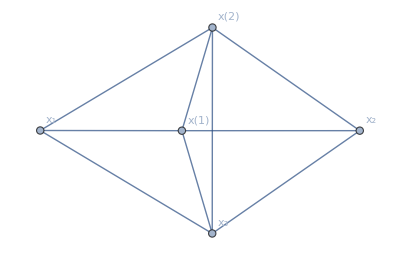
-(256 (π^4 ξ^4 (graphSpacetime[-Graphics-]+graphSpacetime[-Graphics-]) II[{x_1,x[1]}] II[{x_1,x[2]}] II[{x_2,x[1]}] II[{x_2,x[2]}] II[{x_3,x[1]}] II[{x_3,x[2]}] II[{x[1],x[2]}]))/(II[{x_1,x_2}] II[{x_1,x_3}] II[{x_2,x_3}])+O[1/N]^1

```mathematica
If[classicalSaddlePoint,n=1,n=13]; (* n=13 is an hardcoded cutoff and needs to be increased to calculate higher powers of 1/N *)
CartesianRadiusVariables={r[1,2]};

(* Jacobian *)
jacobian=(1/(4π)+v r[1,2]);

(* action *)
N Sum[-(1-i,j)8 π^2 ρ[i,j]ρ[j,i],{i,2},{j,2}]+N Log[Det[Table[-2ⅈ (1-i,j)ρ[i,j]sqrtd[i ,j],{i,2},{j,2}]]]//Collect[#,Log[x__]]&;
%/.{sqrtd[i_,j_]:>2π √(polarizationReal[i].polarizationReal[j]II[{Subscript[x, i],Subscript[x, j]}//Sort])}/.Flatten[{{ρR[1,2]->(1/(4π)+v r[1,2])Cos[θ[1,2]]}, {ρI[1,2]->(1/(4π)+v r[1,2])Sin[θ[1,2]]}}]//Simplify;
tmp=%/.Log[x_]:>Log[x//Simplify]//PowerExpand//Simplify;

(* no linear term in action *)
SeriesCoefficient[tmp,{v,0,1}]==0

(* integrand *)
exponent=v^2 SeriesCoefficient[tmp,{v,0,2}]//CoefficientRules[#,CartesianRadiusVariables]&//Simplify//FromCoefficientRules[#,CartesianRadiusVariables]&;

fieldDepFactor=Table[0,{i,n}];

Monitor[
Table[fieldDepFactor[[i]]=(SeriesCoefficient[jacobian loopOperator[V](Exp[tmp-exponent-(tmp/.v->0)]//ExpandAll//Simplify//PowerExpand//Simplify),{v,0,i-1}]//Normal)/.v->1//CoefficientRules[#,CartesianRadiusVariables]&//FromCoefficientRules[#,CartesianRadiusVariables]&,{i,Length[fieldDepFactor]}],
Row[{ProgressIndicator[i,{1,Length[fieldDepFactor]}],i},""]];

exponent=exponent/.v->1;

fieldDepFactor=Total[fieldDepFactor];

fieldIndepFactor=1/(1/(16π N))^(2(2-1)/2)Exp[tmp/.v->0]/(treeLevel//PowerExpand)//ExpandAll//PowerExpand//Simplify//Distribute;

(* discard odd powers of any field, which would give zero upon Gaussian integration *)
For[i=1,i≤Length[CartesianRadiusVariables],i++,
fieldDepFactor=fieldDepFactor/.{CartesianRadiusVariables[[i]]->ϵ^2 CartesianRadiusVariables[[i]]}/.{ϵ^n_:>If[EvenQ[n/2],1,0]};
];

(* simplify even powers *)
If[Head[tmp2]===Plus,{
tmp2=List@@fieldDepFactor;
Print[Total[tmp2]==fieldDepFactor];
},
tmp2={fieldDepFactor};
];

Monitor[
Table[tmp2[[i]]=tmp2[[i]]//Simplify,{i,Length[tmp2]}],
Row[{ProgressIndicator[i,{1,Length[tmp2]}],i},""]];

fieldDepFactor=Total[tmp2];

(* integration *)
If[Head[tmp3]===Plus,{
tmp3=List@@fieldDepFactor;
Print[Total[tmp3]==fieldDepFactor];
},
tmp3={fieldDepFactor};
];

Monitor[
For[i=1,i≤Length[tmp3],i++,
For[j=1,j≤Length[CartesianRadiusVariables],j++,
tmp3[[i]]=If[(tmp3[[i]]/.{CartesianRadiusVariables[[j]]->0})===0,tmp3[[i]]/.{CartesianRadiusVariables[[j]]^n_:>(-Coefficient[exponent,CartesianRadiusVariables[[j]]^2])^(-1/2-n/2) Gamma[(1+n)/2]},tmp3[[i]](√π)/(√(-Coefficient[exponent,CartesianRadiusVariables[[j]]^2]))];
]],
Row[{ProgressIndicator[i,{1,Length[tmp3]}],i},""]];

(* large-N limit *)
Total[Series[Series[fieldIndepFactor tmp3,{N,∞,0}],{N,∞,0}]]//Simplify;
Integrate[%,{θ[1,2],0,2π}];

(* display result *)
%/.{graphSpacetime[list_]:>graphSpacetime[Graph[list,VertexLabels->"Name"]]}//Simplify

Clear[n,CartesianRadiusVariables,jacobian,exponent,fieldDepFactor,fieldIndepFactor,tmp,tmp2,tmp3]
```

```mathematica
Clear[V,polarizationComplex,polarizationReal,classicalSaddlePoint,traces,treeLevel,links,loopOperator]
```

# Results <tr(...) tr(...)> in χCFT_4

This section contains some results calculated in the sub-section “Correlators of multi-trace operators”.
It can be used to check the correct functioning of the notebook.

## Data 1: <tr(ϕ_1(x_1)ϕ_1(x_2))tr(ϕ_1^†(x_3)ϕ_1^†(x_4))> up to 4 loops

```mathematica
theory="";
traces={Subscript[ϕ1[Subscript[x, 1]], o[1],o[2]],Subscript[ϕ1[Subscript[x, 2]], o[2],o[1]],Subscript[OverBar[ϕ1][Subscript[x, 3]], o[3],o[4]],Subscript[OverBar[ϕ1][Subscript[x, 4]], o[4],o[3]]};
treeLevel=II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}];
links={Subscript[x, 1]<->Subscript[x, 2],Subscript[x, 3]<->Subscript[x, 4]};
```

```mathematica
data[1]=II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}];
```

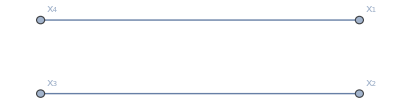
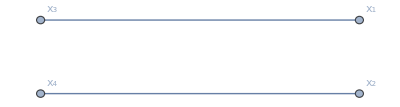
```mathematica
(* V=0 *)
data[1,0]=(graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}])/(II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]);
data[1,0]==1/.{graphSpacetime[x_]:>1}//Simplify
```

True

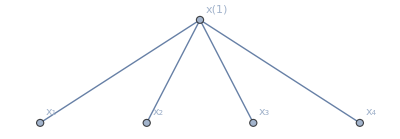
```mathematica
(* V=1 *)
data[1,1]=(64 π^2 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}])/(II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]);
```

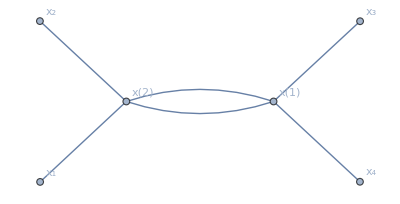
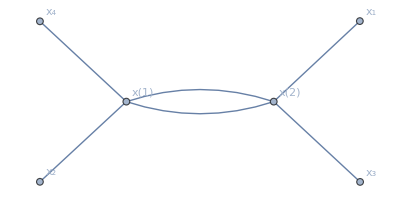
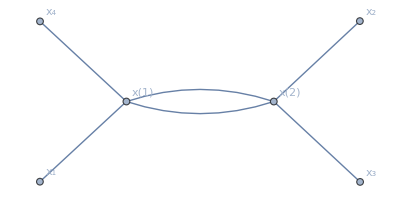
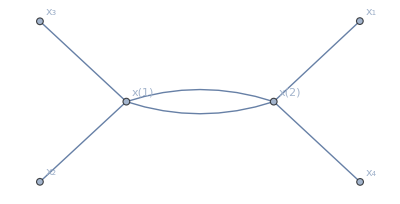
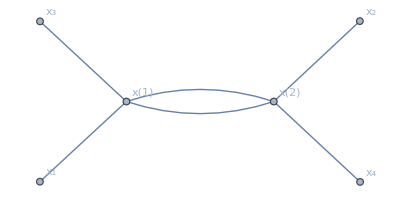
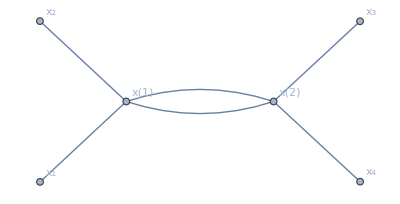
```mathematica
(* V=2 *)
data[1,2]=1/(II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}])128 π^4 (8 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}]+(ξ2^4+ξ3^4) graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+ξ2^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+ξ3^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+ξ2^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]+ξ3^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]+ξ2^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]+ξ3^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]+8 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}]) II[{x[1],x[2]}]^2;
```

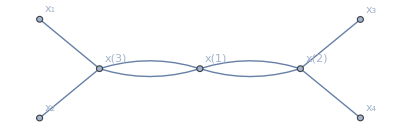
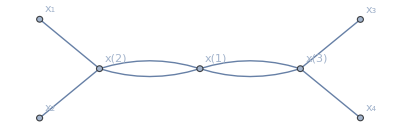
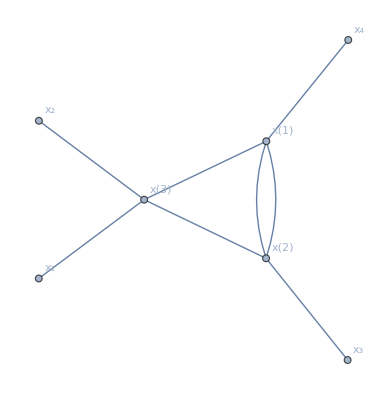
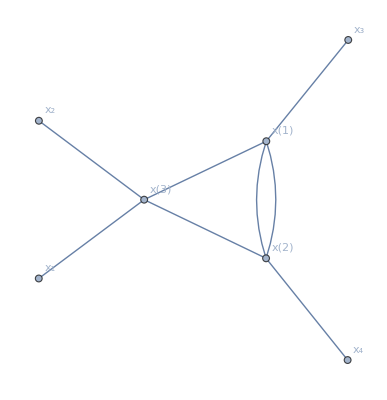
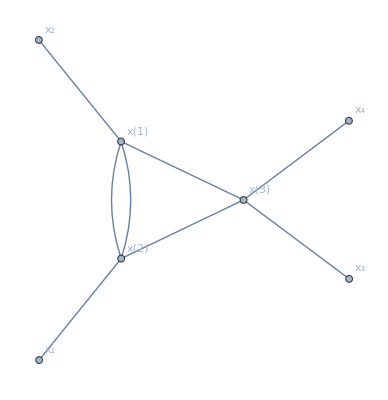
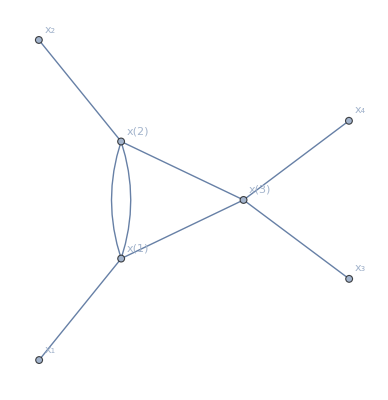
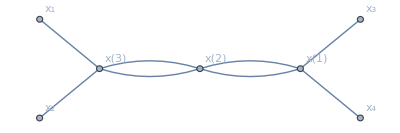
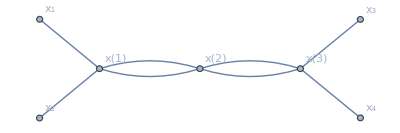
```mathematica
(* V=3 *)
data[1,3]=1/(3 (II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]))8192 π^6 α1^2 (4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2+4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2+II[{x[2],x[3]}] (3 (ξ2^4+ξ3^4) graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]+3 (ξ2^4+ξ3^4) graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]+3 ξ2^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]+3 ξ3^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]+3 ξ2^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]+3 ξ3^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]+4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]+4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]+4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[2],x[3]}]+4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[3]}]));
```

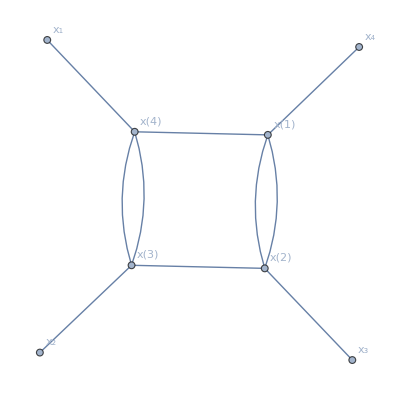
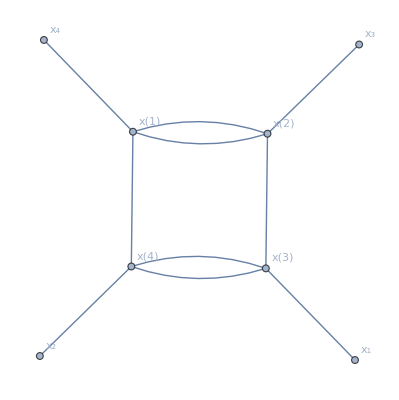
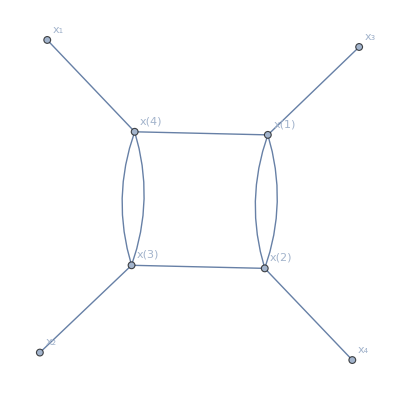
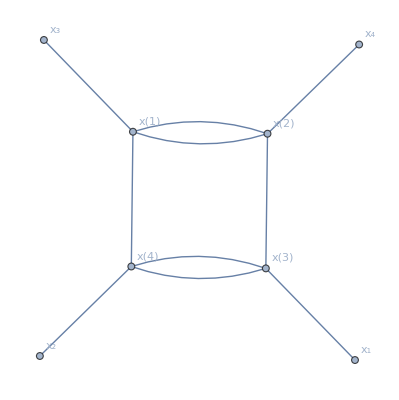
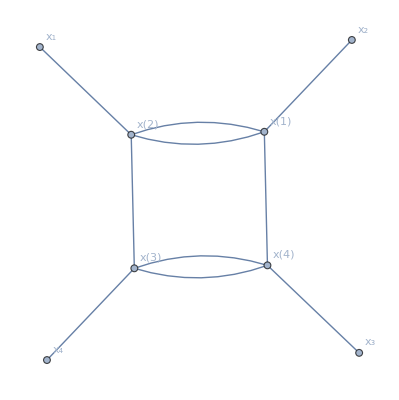
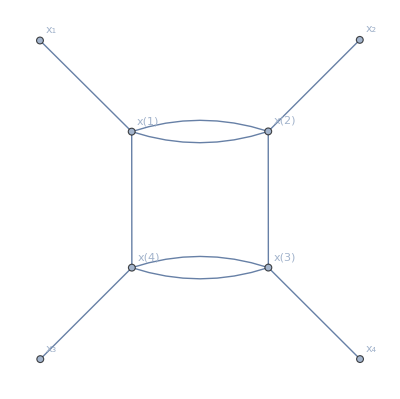
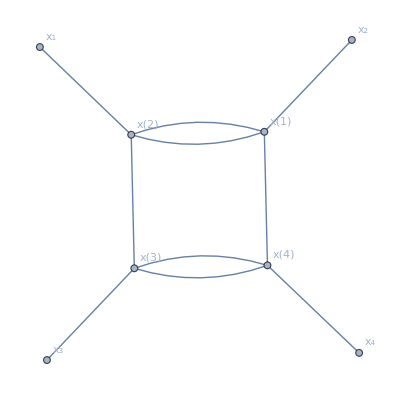
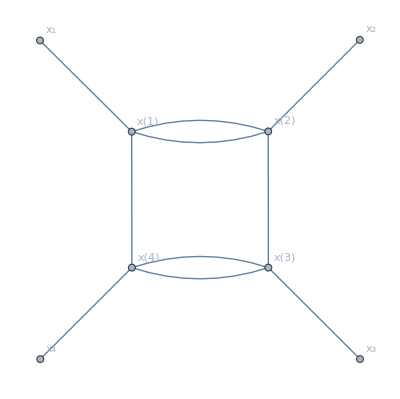
```mathematica
(* V=4 *)

data[1,4]=1/(3 (II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]))64 π^4 (768 π^4 ξ2^4 ξ3^4 II[{x[1],x[2]}]^2 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[4]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[4]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[4]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[4]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[4]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[4]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[2],x[4]}]) II[{x[3],x[4]}]^2+128 π^4 ξ2^8 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2)+128 π^4 ξ3^8 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2)+4096 π^4 α1^8 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]^2)+6144 π^4 α1^4 ξ2^4 II[{x[1],x[2]}]^2 (2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]+2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]+(graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[4]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[4]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}] II[{x[2],x[4]}]) II[{x[3],x[4]}]^2)+6144 π^4 α1^4 ξ3^4 II[{x[1],x[2]}]^2 (2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]+2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]+(graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[4]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[4]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}] II[{x[2],x[4]}]) II[{x[3],x[4]}]^2)-3 ξ2^2 ξ3^2 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+(graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}]) II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]) Subscript[σttDII[{x[1],x[3]}], α[1],αd[3]] Subscript[σttDII[{x[1],x[4]}], β[1],βd[4]] Subscript[σttDII[{x[2],x[3]}], β[2],βd[3]] Subscript[σttDII[{x[2],x[4]}], α[2],αd[4]] ϵ[α[1],β[1]] ϵ[α[2],β[2]] ϵ[αd[3],βd[3]] ϵ[αd[4],βd[4]]-3 ξ2^2 ξ3^2 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+(graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}]) II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]) Subscript[σttDII[{x[1],x[3]}], β[1],βd[3]] Subscript[σttDII[{x[1],x[4]}], α[1],αd[4]] Subscript[σttDII[{x[2],x[3]}], α[2],αd[3]] Subscript[σttDII[{x[2],x[4]}], β[2],βd[4]] ϵ[α[1],β[1]] ϵ[α[2],β[2]] ϵ[αd[3],βd[3]] ϵ[αd[4],βd[4]]);
```

## Data 2: <tr(ϕ_2(x_1)ϕ_1(x_2)ϕ_1(x_1)ϕ_2^†(x_2))tr(ϕ_1^†(x_3)ϕ_1^†(x_4))> up to 3 loops

```mathematica
theory="";
traces={Subscript[ϕ2[Subscript[x, 1]], o[1],o[2]],Subscript[ϕ1[Subscript[x, 2]], o[2],o[3]],Subscript[ϕ1[Subscript[x, 1]], o[3],o[4]],Subscript[OverBar[ϕ2][Subscript[x, 2]], o[4],o[1]],Subscript[OverBar[ϕ1][Subscript[x, 3]], o[5],o[6]],Subscript[OverBar[ϕ1][Subscript[x, 4]], o[6],o[5]]};
treeLevel=(4 π ξ3)^4 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] (II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]) II[{x[1],x[2]}];
links={Subscript[x, 1]<->Subscript[x, 2],Subscript[x, 3]<->Subscript[x, 4]};
```

```mathematica
data[2]=256 π^4 ξ3^4 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] (II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]) II[{x[1],x[2]}];
```

```mathematica
(* V=0,1 *)
data[2,0]=data[2,1]=0;
```

```mathematica
(* V=2 *)
data[2,2]=(graphSpacetime[-Graphics-] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+(graphSpacetime[-Graphics-]+graphSpacetime[-Graphics-]) II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}])/(2 (II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]));
data[2,2]==1/.{graphSpacetime[x_]:>1}//Simplify
```

True

```mathematica
(* V=3 *)
data[2,3]=(32 π^2 α1^2 (graphSpacetime[-Graphics-]+graphSpacetime[-Graphics-]) II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[2],x[3]}])/(II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]);
```

## Continue: check against exact resummation

```mathematica
Subscript[χ, V]=(4π)^2 α1^2;
Subscript[χ, B]=(4π)^4(ξ2^4+ ξ3^4);
Subscript[χ, F]=(4π)^4 ξ2^2 ξ3^2;
pref1=1/(2 II[{Subscript[x, 3],Subscript[x, 4]}]^2);
treeLevel=data[1];
```

```mathematica
(* V=0 *)

(* expansion of exact resummation *)
pref1 II[{Subscript[x, 1],Subscript[x, 3]}]II[{Subscript[x, 2],Subscript[x, 4]}] II[{Subscript[x, 3],Subscript[x, 4]}]^2;
tmp1=%+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}}])+(%/.Flatten[{{Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}, {Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])//PowerExpand//Simplify;

(* effective theory *)
data[1,0];
tmp2=treeLevel%/.{graphSpacetime[x_]:>1};

(* check *)
tmp1-tmp2/.{II[list_]:>II[list//Sort]}//Simplify
```

0

```mathematica
(* V=1 *)

(* expansion of exact resummation *)
pref1((2 Subscript[χ, V])II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}]II[{Subscript[x, 3],x[1]}]II[{Subscript[x, 4],x[1]}])II[{Subscript[x, 3],Subscript[x, 4]}]^2;
tmp1=%+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}}])+(%/.Flatten[{{Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}, {Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])//PowerExpand//Simplify;

(* effective theory *)
data[1,1];
tmp2=treeLevel%/.{graphSpacetime[x_]:>1};

(* check *)
tmp1-tmp2/.{II[list_]:>II[list//Sort]}//Simplify
```

0

```mathematica
(* V=2 *)

(* expansion of exact resummation *)
pref1(Subscript[χ, B] II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}]^2 II[{Subscript[x, 3],x[1]}]II[{Subscript[x, 4],x[2]}]+ (2 Subscript[χ, V])^2 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}] II[{x[1],x[2]}]^2 II[{Subscript[x, 3],x[2]}]II[{Subscript[x, 4],x[2]}])II[{Subscript[x, 3],Subscript[x, 4]}]^2;
tmp1=%+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}}])+(%/.Flatten[{{Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}, {Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])//PowerExpand//Simplify;

(* effective theory *)
data[1,2];
tmp2=treeLevel%/.{graphSpacetime[x_]:>1};

(* check *)
tmp1-tmp2;
(%+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[1]}}]))/(2!)/.{II[list_]:>II[list//Sort]}//Simplify
```

0

```mathematica
(* V=3 *)

(* expansion of exact resummation *)
pref1((2 Subscript[χ, V])Subscript[χ, B] II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}]II[{x[1],x[2]}]II[{x[1],x[3]}] II[{x[2],x[3]}]^2 II[{Subscript[x, 3],x[2]}]II[{Subscript[x, 4],x[3]}]+Subscript[χ, B](2 Subscript[χ, V])II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]II[{x[2],x[3]}]II[{Subscript[x, 3],x[3]}]II[{Subscript[x, 4],x[3]}]+(2 Subscript[χ, V])^3 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]^2 II[{Subscript[x, 3],x[3]}]II[{Subscript[x, 4],x[3]}])II[{Subscript[x, 3],Subscript[x, 4]}]^2;
tmp1=%+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}}])+(%/.Flatten[{{Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}, {Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])//PowerExpand//Simplify;

(* effective theory *)
data[1,3];

tmp2=treeLevel%/.{graphSpacetime[x_]:>1};

(* check *)
tmp1-tmp2;
(%+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[3]}, {x[3]->x[2]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[1]}, {x[3]->x[3]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[3]}, {x[3]->x[1]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[1]}, {x[3]->x[2]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[2]}, {x[3]->x[1]}}]))/(3!)/.{II[list_]:>II[list//Sort]}//Simplify
```

0

```mathematica
(* V=4 *)

(* expansion of exact resummation *)
pref1(Subscript[χ, B]^2 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]II[{x[2],x[4]}] II[{x[3],x[4]}]^2 II[{Subscript[x, 3],x[3]}]II[{Subscript[x, 4],x[4]}]+(2 Subscript[χ, V])^2 Subscript[χ, B] II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]II[{x[2],x[4]}] II[{x[3],x[4]}]^2 II[{Subscript[x, 3],x[3]}]II[{Subscript[x, 4],x[4]}]+(2 Subscript[χ, V])Subscript[χ, B](2 Subscript[χ, V])II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}]II[{x[1],x[2]}]II[{x[1],x[3]}] II[{x[2],x[3]}]^2 II[{x[2],x[4]}]II[{x[3],x[4]}]II[{Subscript[x, 3],x[4]}]II[{Subscript[x, 4],x[4]}]+Subscript[χ, B](2 Subscript[χ, V])^2 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]II[{x[2],x[3]}] II[{x[3],x[4]}]^2 II[{Subscript[x, 3],x[4]}]II[{Subscript[x, 4],x[4]}]+(2 Subscript[χ, V])^4 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]^2 II[{Subscript[x, 3],x[4]}]II[{Subscript[x, 4],x[4]}]-(1/2 Subscript[χ, F] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] (Subscript[σttDII[{x[1],x[3]}], α[2],αd[4]] Subscript[σttDII[{x[1],x[4]}], β[1],βd[4]] Subscript[σttDII[{x[2],x[3]}], β[2],βd[3]] Subscript[σttDII[{x[2],x[4]}], α[1],αd[3]]+Subscript[σttDII[{x[1],x[3]}], β[2],βd[4]] Subscript[σttDII[{x[1],x[4]}], α[1],αd[4]] Subscript[σttDII[{x[2],x[3]}], α[2],αd[3]] Subscript[σttDII[{x[2],x[4]}], β[1],βd[3]]) ϵ[α[1],β[1]] ϵ[α[2],β[2]] ϵ[αd[3],βd[3]] ϵ[αd[4],βd[4]]))II[{Subscript[x, 3],Subscript[x, 4]}]^2;
tmp1=%+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}}])+(%/.Flatten[{{Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}, {Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])//PowerExpand//Simplify;

(* effective theory *)
data[1,4];
tmp2=treeLevel%/.{graphSpacetime[x_]:>1};

(* check *)
tmp1-tmp2;
1/(4!)(%+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[2]}, {x[3]->x[4]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[3]}, {x[3]->x[2]}, {x[4]->x[4]}}])+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[3]}, {x[3]->x[4]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[4]}, {x[3]->x[2]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[4]}, {x[3]->x[3]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[1]}, {x[3]->x[3]}, {x[4]->x[4]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[1]}, {x[3]->x[4]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[3]}, {x[3]->x[1]}, {x[4]->x[4]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[3]}, {x[3]->x[4]}, {x[4]->x[1]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[4]}, {x[3]->x[1]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[4]}, {x[3]->x[3]}, {x[4]->x[1]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[1]}, {x[3]->x[2]}, {x[4]->x[4]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[1]}, {x[3]->x[4]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[2]}, {x[3]->x[1]}, {x[4]->x[4]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[2]}, {x[3]->x[4]}, {x[4]->x[1]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[4]}, {x[3]->x[1]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[4]}, {x[3]->x[2]}, {x[4]->x[1]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[1]}, {x[3]->x[2]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[1]}, {x[3]->x[3]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[2]}, {x[3]->x[1]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[2]}, {x[3]->x[3]}, {x[4]->x[1]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[3]}, {x[3]->x[1]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[3]}, {x[3]->x[2]}, {x[4]->x[1]}}]))/.{II[list_]:>II[list//Sort]}/.{Subscript[σttDII[list_], α_,β_]:>(-1)^((Signature[list]+Signature[list//Sort])/2+1)Subscript[σttDII[list//Sort], α,β]}//Simplify
```

0

```mathematica
Subscript[χ, V]=.;
Subscript[χ, B]=.;
Subscript[χ, F]=.;
Clear[tmp1,tmp2,treeLevel,pref1]
```

# Results <tr(...) tr(...)> in bi-scalar theory

## Data 3: <tr(ϕ_1(x_1)ϕ_1(x_2))tr(ϕ_1^†(x_3)ϕ_1^†(x_4))> up to 4 loops

```mathematica
theory="biscalar";
traces={Subscript[ϕ1[Subscript[x, 1]], o[1],o[2]],Subscript[ϕ1[Subscript[x, 2]], o[2],o[1]],Subscript[OverBar[ϕ1][Subscript[x, 3]], o[3],o[4]],Subscript[OverBar[ϕ1][Subscript[x, 4]], o[4],o[3]]};
treeLevel=II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}];
links={Subscript[x, 1]<->Subscript[x, 2],Subscript[x, 3]<->Subscript[x, 4]};
```

```mathematica
data[3]=II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}];
```

```mathematica
(* V=0 *)
data[3,0]=(graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}])/(II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]);
data[3,0]==1/.{graphSpacetime[x_]:>1}//Simplify
```

True

```mathematica
(* V=1 *)
data[3,1]=(64 π^2 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}])/(II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]);
```

```mathematica
(* V=2 *)
data[3,2]=1/(II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}])128 π^4 (8 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}]+ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]+ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]+8 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}]) II[{x[1],x[2]}]^2;
```

```mathematica
(* V=3 *)
data[3,3]=(8192 π^6 α1^2 (3 ξ^4 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]+(graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}]) II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}]) II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[3]}]+4 α1^4 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2+(graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2+(graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}]) II[{x[1],x[3]}]^2) II[{x[2],x[3]}]^2)))/(3 (II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]));
```

```mathematica
(* V=4 *)

data[3,4]=(8192 π^8 (ξ^8 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2)+32 α1^8 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}]^2 II[{x[3],x[4]}]^2)+48 α1^4 ξ^4 II[{x[1],x[2]}]^2 (2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]+2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]+(graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[4]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[4]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}] II[{x[2],x[4]}]) II[{x[3],x[4]}]^2)))/(3 (II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]));
```

## Data 4: <tr(ϕ_2(x_1)ϕ_1(x_2)ϕ_1(x_1)ϕ_2^†(x_2))tr(ϕ_1^†(x_3)ϕ_1^†(x_4))> up to 4 loops

```mathematica
theory="biscalar";
traces={Subscript[ϕ2[Subscript[x, 1]], o[1],o[2]],Subscript[ϕ1[Subscript[x, 2]], o[2],o[3]],Subscript[ϕ1[Subscript[x, 1]], o[3],o[4]],Subscript[OverBar[ϕ2][Subscript[x, 2]], o[4],o[1]],Subscript[OverBar[ϕ1][Subscript[x, 3]], o[5],o[6]],Subscript[OverBar[ϕ1][Subscript[x, 4]], o[6],o[5]]};
treeLevel=(4 π ξ)^4 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] (II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]) II[{x[1],x[2]}];
links={Subscript[x, 1]<->Subscript[x, 2],Subscript[x, 3]<->Subscript[x, 4]};
```

```mathematica
data[4]=256 π^4 ξ^4 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] (II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]) II[{x[1],x[2]}];
```

```mathematica
(* V=0,1 *)
data[4,0]=data[4,1]=0;
```

```mathematica
(* V=2 *)
data[4,2]=(graphSpacetime[-Graphics-] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+(graphSpacetime[-Graphics-]+graphSpacetime[-Graphics-]) II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}])/(2 (II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]));
data[4,2]==1/.{graphSpacetime[x_]:>1}//Simplify
```

True

```mathematica
(* V=3 *)
data[4,3]=(32 π^2 α1^2 (graphSpacetime[-Graphics-]+graphSpacetime[-Graphics-]) II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[2],x[3]}])/(II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]);
```

```mathematica
(* V=4 *)
data[4,4]=(32 π^4 (48 α1^4 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] (graphSpacetime[-Graphics-] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[2],x[3]}]+(graphSpacetime[-Graphics-]+graphSpacetime[-Graphics-]) II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[4]}] II[{x[2],x[4]}]) II[{x[3],x[4]}]^2+ξ^4 (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}] II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}]^2 II[{x[2],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[3]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[2],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[4]}]^2 II[{x[2],x[3]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[4]}] II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[4]}] II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[4]}] II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[4]}] II[{x[2],x[3]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[4]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[4]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[4]}] II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[3]}] II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}] II[{x[1],x[3]}] II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[3]}] II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[3]}] II[{x[2],x[4]}]^2 II[{x[3],x[4]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[4]}] II[{x[2],x[3]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[4]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[4]}] II[{x[1],x[2]}] II[{x[1],x[3]}] II[{x[2],x[4]}] II[{x[3],x[4]}]^2)))/(3 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] (II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]+II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]) II[{x[1],x[2]}]);
```

# Results <det(...) det(...)> in bi-scalar theory

This section contains some results calculated in the sub-section “Correlators of 2 determinants and multi-trace operators”.
It can be used to check the correct functioning of the notebook.

## Data 5: <det(ω[1]_1 ϕ_1+ω[1]_2 ϕ_2)(x_1)det(ω[2]_1 ϕ_1^†+ω[2]_2 ϕ_2^†)(x_2)> up to 3 loops

```mathematica
theory="biscalar";
polarizationComplex[1]={Subscript[ω[1], 1],0,Subscript[ω[1], 2],0,0,0}; 
polarizationComplex[2]={0,Subscript[ω[2], 1],0,Subscript[ω[2], 2],0,0};
traces={};
treeLevel=N!(((Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])II[{Subscript[x, 1],Subscript[x, 2]}])/N)^N;
links={};
```

```mathematica
data[5]=N!(((Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])II[{Subscript[x, 1],Subscript[x, 2]}])/N)^N;
```

```mathematica
(* V=0 *)
data[5,0]=1;
```

```mathematica
(* V=1 *)
data[5,1]=(16 π^2 (α2^2+ξ^2) graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2])/(II[{Subscript[x, 1],Subscript[x, 2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^2);
```

```mathematica
(* V=2 *)
data[5,2]=1/(II[{Subscript[x, 1],Subscript[x, 2]}]^4 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^4)128 π^4 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2] ((α2^4+2 α2^2 ξ^2+2 ξ^4) graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2]+2 (α2^2+ξ^2)^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{x[1],x[2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^2);
```

```mathematica
(* V=3 *)
```

```mathematica
data[5,3]=1/(3 II[{Subscript[x, 1],Subscript[x, 2]}]^6 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^6)2048 π^6 Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2] (2 (α2^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^4 II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^4+II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] (2 (α2^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^4 II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^4+II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] (2 (α2^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^4 II[{x[1],x[3]}]^2 II[{x[2],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^4+II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2] (2 (α2^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{x[1],x[2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^2+2 (α2^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^2+II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] ((α2^6+3 α2^4 ξ^2+6 α2^2 ξ^4+6 ξ^6) graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2]+2 (α2^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{x[2],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^2)))));
```

## Continue

```mathematica
tmp=data[5]{data[5,0],data[5,1],data[5,2],data[5,3]};
```

```mathematica
(* Subscript[ϕ, 1]^(N-L2)Subscript[ϕ, 2]^L2 and small L2 *)
```

```mathematica
L2=7;
Series[D[((N-L2)!)/(L2!N!)(tmp/.fixedPointBiscalar/.{Subscript[ω[1], 1]->1,Subscript[ω[2], 1]->1})/(N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N)//PowerExpand,{Subscript[ω[1], 2],L2},{Subscript[ω[2], 2],L2}]/.{Subscript[ω[1], 2]->0,Subscript[ω[2], 2]->0}//Simplify,{N,∞,0}]//Simplify
Clear[L2]
```

{1+√O[1/N],0,O[1/N]^2,O[1/N]^2}

```mathematica
(* Subscript[ϕ, 1]^(N-L1)Subscript[ϕ, 2]^L2 and large L2 *)
```

```mathematica
((N-L2)!)/(L2!N!)(tmp/.fixedPoint/.{Subscript[ω[1], 1]->1,Subscript[ω[2], 1]->1})/(N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N)//PowerExpand;

L2=5;
D[%%[[2]]//PowerExpand,{Subscript[ω[1], 2],L2},{Subscript[ω[2], 2],L2}]==0/.fixedPointBiscalar/.{Subscript[ω[1], 2]->0,Subscript[ω[2], 2]->0}//FullSimplify
D[%%%[[3]]//PowerExpand,{Subscript[ω[1], 2],L2},{Subscript[ω[2], 2],L2}]==(128 (-1+L2) L2 (L2-N) (1+L2-N) π^4 ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2)/((-3+N) (-2+N) (-1+N) N II[{Subscript[x, 1],Subscript[x, 2]}]^4)/.fixedPointBiscalar/.{Subscript[ω[1], 2]->0,Subscript[ω[2], 2]->0}//FullSimplify

Clear[L2]
```

True

True

```mathematica
Series[(128 (-1+L2) L2 (L2-N) (1+L2-N) π^4 ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2)/((-3+N) (-2+N) (-1+N) N II[{Subscript[x, 1],Subscript[x, 2]}]^4)/.{L2->N l2},{N,∞,0}]/.fixedPointBiscalar//FullSimplify
```

(128 (-1+l2)^2 l2^2 π^4 ξ^4 graphSpacetime[-Graphics-] II[{x_1,x[1]}]^2 II[{x_1,x[2]}]^2 II[{x_2,x[1]}]^2 II[{x_2,x[2]}]^2)/II[{x_1,x_2}]^4+O[1/N]^1

## Data 6: <det(ω[1]_1 ϕ_1^†+ω[1]_2 ϕ_2)(x_1)det(ω[2]_1 ϕ_1+ω[2]_2 ϕ_2^†)(x_2)> up to 3 loops

```mathematica
theory="biscalar";
polarizationComplex[1]={0,Subscript[ω[1], 1],Subscript[ω[1], 2],0,0,0}; 
polarizationComplex[2]={Subscript[ω[2], 1],0,0,Subscript[ω[2], 2],0,0};
traces={};
treeLevel=N!(((Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])II[{Subscript[x, 1],Subscript[x, 2]}])/N)^N;
links={};
```

```mathematica
data[6]=N!(((Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])II[{Subscript[x, 1],Subscript[x, 2]}])/N)^N;
```

```mathematica
(* V=0 *)
data[6,0]=1;
```

```mathematica
(* V=1 *)
data[6,1]=(16 π^2 (α3^2+ξ^2) graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2])/(II[{Subscript[x, 1],Subscript[x, 2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^2);
```

```mathematica
(* V=2 *)
data[6,2]=1/(II[{Subscript[x, 1],Subscript[x, 2]}]^4 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^4)128 π^4 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2] ((α3^4+2 α3^2 ξ^2+2 ξ^4) graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2]+2 (α3^2+ξ^2)^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{x[1],x[2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^2);
```

```mathematica
(* V=3 *)
```

```mathematica
data[6,3]=1/(3 II[{Subscript[x, 1],Subscript[x, 2]}]^6 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^6)2048 π^6 Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2] ((α3^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^4 II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^4+(α3^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^4 II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^4+II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] (2 (α3^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^4 II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^4+II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] ((α3^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^4 II[{x[1],x[3]}]^2 II[{x[2],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^4+(α3^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^4 II[{x[1],x[3]}]^2 II[{x[2],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^4+II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2] (2 (α3^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{x[1],x[2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^2+2 (α3^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^2+II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] ((α3^6+3 α3^4 ξ^2+6 α3^2 ξ^4+6 ξ^6) graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 2],x[3]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2]+2 (α3^2+ξ^2)^3 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{x[2],x[3]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2])^2)))));
```

## Continue

```mathematica
tmp=data[6]{data[6,0],data[6,1],data[6,2],data[6,3]};
```

```mathematica
(* (Subscript[ϕ, 1]^†)^(N-L2)Subscript[ϕ, 2]^L2 and small L2 *)
```

```mathematica
L2=7;
Series[D[((N-L2)!)/(L2!N!)(tmp/.fixedPointBiscalar/.{Subscript[ω[1], 1]->1,Subscript[ω[2], 1]->1})/(N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N)//PowerExpand,{Subscript[ω[1], 2],L2},{Subscript[ω[2], 2],L2}]/.{Subscript[ω[1], 2]->0,Subscript[ω[2], 2]->0}//Simplify,{N,∞,0}]//Simplify
Clear[L2]
```

{1+√O[1/N],0,O[1/N]^2,O[1/N]^2}

## Data 7: <det(ω[1]_1 ϕ_1+ω[1]_2 ϕ_2+ω[1]_3 ϕ_1^†+ω[1]_4 ϕ_2^†)(x_1)det(ω[2]_1 ϕ_1^†+ω[2]_2 ϕ_2^†+ω[2]_3 ϕ_1+ω[2]_4 ϕ_2(x_2)> up to 2 loops

```mathematica
theory="biscalar";
polarizationComplex[1]={Subscript[ω[1], 1],Subscript[ω[1], 3],Subscript[ω[1], 2],Subscript[ω[1], 4],0,0}; 
polarizationComplex[2]={Subscript[ω[2], 3],Subscript[ω[2], 1],Subscript[ω[2], 4],Subscript[ω[2], 2],0,0};
traces={};
treeLevel=N!(((Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])II[{Subscript[x, 1],Subscript[x, 2]}])/N)^N;
links={};
```

```mathematica
data[7]=N!(((Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])II[{Subscript[x, 1],Subscript[x, 2]}])/N)^N;
```

```mathematica
(* V=0 *)
data[7,0]=1;
```

```mathematica
(* V=1 *)
data[7,1]=-(16 N π^2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[1]}]^2 (Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]+Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 4]))/(II[{Subscript[x, 1],Subscript[x, 2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])^2)+(4 π^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[1]}]^2 (12 (α2^2+ξ^2) Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4]+Subscript[ω[1], 2] (12 (α3^2+ξ^2) Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 3]+Subscript[ω[1], 4] ((12 α2^2+12 α3^2+25 ξ^2) Subscript[ω[2], 1] Subscript[ω[2], 3]+48 α1^2 Subscript[ω[2], 2] Subscript[ω[2], 4]))+Subscript[ω[1], 1] (12 (α2^2+ξ^2) Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2]+12 (α3^2+ξ^2) Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 4]+Subscript[ω[1], 3] (48 α1^2 Subscript[ω[2], 1] Subscript[ω[2], 3]+(12 α2^2+12 α3^2+25 ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4]))))/(3 II[{Subscript[x, 1],Subscript[x, 2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])^2);
```

```mathematica
(* V=2 *)
data[7,2]=(128 N^2 π^4 ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 (Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]+Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 4])^2)/(II[{Subscript[x, 1],Subscript[x, 2]}]^4 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])^4)+(32 N π^4 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] (-ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] (Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]+Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 4])^2-24 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] (Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]+Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 4]) ((α2^2+ξ^2) Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4]+Subscript[ω[1], 2] ((α3^2+ξ^2) Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 3]+Subscript[ω[1], 4] ((α2^2+α3^2+6 ξ^2) Subscript[ω[2], 1] Subscript[ω[2], 3]+4 α1^2 Subscript[ω[2], 2] Subscript[ω[2], 4]))+Subscript[ω[1], 1] ((α2^2+ξ^2) Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2]+(α3^2+ξ^2) Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 4]+Subscript[ω[1], 3] (4 α1^2 Subscript[ω[2], 1] Subscript[ω[2], 3]+(α2^2+α3^2+6 ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4])))+12 ξ^4 II[{Subscript[x, 1],Subscript[x, 2]}] (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}]) II[{x[1],x[2]}] (Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4] (Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])+Subscript[ω[1], 1]^2 Subscript[ω[2], 1]^2 (Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4]+Subscript[ω[1], 2] Subscript[ω[2], 2] (Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4]))+Subscript[ω[1], 1] Subscript[ω[2], 1] (Subscript[ω[1], 2]^2 Subscript[ω[2], 2]^2 (Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])+Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4] (Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])+Subscript[ω[1], 2] Subscript[ω[2], 2] (Subscript[ω[1], 3]^2 Subscript[ω[2], 3]^2+4 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4]+Subscript[ω[1], 4]^2 Subscript[ω[2], 4]^2)))))/(3 II[{Subscript[x, 1],Subscript[x, 2]}]^4 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])^4)+(4 π^4 (ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 (Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]+Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 4])^2-24 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] (-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] (Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]+Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 4]) ((α2^2+ξ^2) Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4]+Subscript[ω[1], 2] ((α3^2+ξ^2) Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 3]+Subscript[ω[1], 4] ((α2^2+α3^2+6 ξ^2) Subscript[ω[2], 1] Subscript[ω[2], 3]+4 α1^2 Subscript[ω[2], 2] Subscript[ω[2], 4]))+Subscript[ω[1], 1] ((α2^2+ξ^2) Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2]+(α3^2+ξ^2) Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 4]+Subscript[ω[1], 3] (4 α1^2 Subscript[ω[2], 1] Subscript[ω[2], 3]+(α2^2+α3^2+6 ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4])))+ξ^4 II[{Subscript[x, 1],Subscript[x, 2]}] (graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}]) II[{x[1],x[2]}] (Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4] (Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])+Subscript[ω[1], 1]^2 Subscript[ω[2], 1]^2 (Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4]+Subscript[ω[1], 2] Subscript[ω[2], 2] (Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4]))+Subscript[ω[1], 1] Subscript[ω[2], 1] (Subscript[ω[1], 2]^2 Subscript[ω[2], 2]^2 (Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])+Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4] (Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])+Subscript[ω[1], 2] Subscript[ω[2], 2] (Subscript[ω[1], 3]^2 Subscript[ω[2], 3]^2+4 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4]+Subscript[ω[1], 4]^2 Subscript[ω[2], 4]^2))))+288 (ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 II[{x[1],x[2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])^2 (Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 3]+Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 4])+2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])^2 ((α2^2+ξ^2)^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4]+Subscript[ω[1], 2] ((α3^2+ξ^2)^2 Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 3]+Subscript[ω[1], 4] ((α2^4+α3^4+2 α2^2 ξ^2+2 α3^2 ξ^2+2 ξ^4) Subscript[ω[2], 1] Subscript[ω[2], 3]+(8 α1^4+ξ^4) Subscript[ω[2], 2] Subscript[ω[2], 4]))+Subscript[ω[1], 1] ((α2^2+ξ^2)^2 Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2]+(α3^2+ξ^2)^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 4]+Subscript[ω[1], 3] ((8 α1^4+ξ^4) Subscript[ω[2], 1] Subscript[ω[2], 3]+(α2^4+α3^4+2 α2^2 ξ^2+2 α3^2 ξ^2+2 ξ^4) Subscript[ω[2], 2] Subscript[ω[2], 4])))+graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 (α2^4 Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2+2 α2^2 α3^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2+α3^4 Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2+24 α2^2 ξ^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2+24 α3^2 ξ^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2+58 ξ^4 Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2+2 α2^2 α3^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2+2 α3^4 Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2+2 α2^2 ξ^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2+26 α3^2 ξ^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2+24 ξ^4 Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2+α3^4 Subscript[ω[1], 2]^2 Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3]^2+2 α3^2 ξ^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3]^2+2 ξ^4 Subscript[ω[1], 2]^2 Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3]^2+8 α1^2 α2^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]+8 α1^2 α3^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]+96 α1^2 ξ^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]+8 α1^2 α3^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]+8 α1^2 ξ^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]+2 α2^4 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+2 α2^2 α3^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+26 α2^2 ξ^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+2 α3^2 ξ^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+24 ξ^4 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+2 α2^2 α3^2 Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+2 α2^2 ξ^2 Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+2 α3^2 ξ^2 Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+4 ξ^4 Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+16 α1^4 Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 4]^2+8 α1^2 α2^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2+8 α1^2 ξ^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2+α2^4 Subscript[ω[1], 3]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 3]^2 Subscript[ω[2], 4]^2+2 α2^2 ξ^2 Subscript[ω[1], 3]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 3]^2 Subscript[ω[2], 4]^2+2 ξ^4 Subscript[ω[1], 3]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 3]^2 Subscript[ω[2], 4]^2+Subscript[ω[1], 1]^2 ((α2^4+2 α2^2 ξ^2+2 ξ^4) Subscript[ω[1], 2]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 2]^2+(α3^4+2 α3^2 ξ^2+2 ξ^4) Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 4]^2+2 (α3^2+ξ^2) Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 4] (4 α1^2 Subscript[ω[2], 1] Subscript[ω[2], 3]+(α2^2+α3^2+12 ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4])+Subscript[ω[1], 3]^2 (16 α1^4 Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2+8 α1^2 (α2^2+α3^2+12 ξ^2) Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]+(α2^4+α3^4+24 α3^2 ξ^2+58 ξ^4+2 α2^2 (α3^2+12 ξ^2)) Subscript[ω[2], 2]^2 Subscript[ω[2], 4]^2)+2 Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2] ((α2^2 (α3^2+ξ^2)+ξ^2 (α3^2+2 ξ^2)) Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 4]+(α2^2+ξ^2) Subscript[ω[1], 3] (4 α1^2 Subscript[ω[2], 1] Subscript[ω[2], 3]+(α2^2+α3^2+12 ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4])))+2 Subscript[ω[1], 1] (Subscript[ω[1], 2]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] ((α2^2 (α3^2+ξ^2)+ξ^2 (α3^2+2 ξ^2)) Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 3]+(α2^2+ξ^2) Subscript[ω[1], 4] ((α2^2+α3^2+12 ξ^2) Subscript[ω[2], 1] Subscript[ω[2], 3]+4 α1^2 Subscript[ω[2], 2] Subscript[ω[2], 4]))+Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 3] Subscript[ω[2], 4] ((α2^2 (α3^2+ξ^2)+ξ^2 (α3^2+2 ξ^2)) Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 4]+(α2^2+ξ^2) Subscript[ω[1], 3] (4 α1^2 Subscript[ω[2], 1] Subscript[ω[2], 3]+(α2^2+α3^2+12 ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4]))+Subscript[ω[1], 2] ((α3^2+ξ^2) Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 4] ((α2^2+α3^2+12 ξ^2) Subscript[ω[2], 1] Subscript[ω[2], 3]+4 α1^2 Subscript[ω[2], 2] Subscript[ω[2], 4])+(α3^2+ξ^2) Subscript[ω[1], 3]^2 Subscript[ω[2], 2] Subscript[ω[2], 3] (4 α1^2 Subscript[ω[2], 1] Subscript[ω[2], 3]+(α2^2+α3^2+12 ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4])+Subscript[ω[1], 3] Subscript[ω[1], 4] (4 α1^2 (α2^2+α3^2+12 ξ^2) Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2+2 (8 α1^4+α2^4+α3^4+13 α3^2 ξ^2+31 ξ^4+α2^2 (α3^2+13 ξ^2)) Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]+4 α1^2 (α2^2+α3^2+12 ξ^2) Subscript[ω[2], 2]^2 Subscript[ω[2], 4]^2))))+ξ^2 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] (ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}]^2 II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}]^2 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])^2 (Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 3]+Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 4])+II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] (-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^3 Subscript[ω[2], 3]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^3 Subscript[ω[2], 3]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^3 Subscript[ω[2], 3]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^3 Subscript[ω[2], 3]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^3 Subscript[ω[2], 3]-ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^3 Subscript[ω[2], 3]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 3]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^3 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^3 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^3 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^3 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^3 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^3 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^3 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 3]-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 3]^2-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3]^2-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]^3-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]^3-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]^3-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]^3-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]^3-ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]^3-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^3 Subscript[ω[1], 3] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^3 Subscript[ω[1], 3] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^3 Subscript[ω[1], 3] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^3 Subscript[ω[1], 3] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^3 Subscript[ω[1], 3] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^3 Subscript[ω[1], 3] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]-ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^3 Subscript[ω[1], 3] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 2]^3 Subscript[ω[2], 4]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 2]^3 Subscript[ω[2], 4]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 2]^3 Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 2]^3 Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 2]^3 Subscript[ω[2], 4]-ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[2], 2]^3 Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]+8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]+8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-8 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-8 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-32 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 3] Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^3 Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^3 Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^3 Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^3 Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^3 Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^3 Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^3 Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3]^2 Subscript[ω[2], 4]+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]^2-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]^2-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]^2-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]^2-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]^2-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]^2-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4] Subscript[ω[2], 2]^2 Subscript[ω[2], 4]^2+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 4]^3 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 4]^3 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 4]^3 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 4]^3 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 4]^3 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 4]^3 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 4]^3 Subscript[ω[2], 1] Subscript[ω[2], 3] Subscript[ω[2], 4]^2+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}]^2 II[{Subscript[x, 2],x[1]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2+2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}]^2 II[{Subscript[x, 2],x[2]}]^2 Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-4 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-16 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-4 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-4 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3]^2 Subscript[ω[1], 4] Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-8 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 2] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 3] Subscript[ω[2], 4]^2-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]^3-2 ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]^3-8 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]^3-2 α2^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]^3-2 α3^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]^3-ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{x[2],x[2]}] Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[1], 4]^2 Subscript[ω[2], 2] Subscript[ω[2], 4]^3-ξ^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{x[1],x[1]}] (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])^2 (Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 3]+Subscript[ω[1], 1] Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 4])+graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{x[1],x[2]}] (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4]) (-2 (4 α1^2+ξ^2) Subscript[ω[1], 1]^2 Subscript[ω[1], 3] Subscript[ω[2], 1] Subscript[ω[2], 2] Subscript[ω[2], 4]-2 Subscript[ω[1], 2] Subscript[ω[1], 4] Subscript[ω[2], 3] ((4 α1^2+ξ^2) Subscript[ω[1], 2] Subscript[ω[2], 1] Subscript[ω[2], 2]+(4 α1^2+ξ^2) Subscript[ω[1], 4] Subscript[ω[2], 1] Subscript[ω[2], 4]+Subscript[ω[1], 3] ((α2^2+α3^2+ξ^2) Subscript[ω[2], 1] Subscript[ω[2], 3]+(α2^2+α3^2+4 ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4]))-Subscript[ω[1], 1] (Subscript[ω[1], 3] Subscript[ω[2], 4] (2 (4 α1^2+ξ^2) Subscript[ω[1], 3] Subscript[ω[2], 2] Subscript[ω[2], 3]+2 Subscript[ω[1], 4] ((α2^2+α3^2+4 ξ^2) Subscript[ω[2], 1] Subscript[ω[2], 3]+(α2^2+α3^2+ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4]))+Subscript[ω[1], 2] (Subscript[ω[1], 3] Subscript[ω[2], 2] (2 (α2^2+α3^2+4 ξ^2) Subscript[ω[2], 1] Subscript[ω[2], 3]+2 (α2^2+α3^2+ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4])+Subscript[ω[1], 4] Subscript[ω[2], 1] (2 (α2^2+α3^2+ξ^2) Subscript[ω[2], 1] Subscript[ω[2], 3]+2 (α2^2+α3^2+4 ξ^2) Subscript[ω[2], 2] Subscript[ω[2], 4])))))))))/(9 II[{Subscript[x, 1],Subscript[x, 2]}]^4 (Subscript[ω[1], 1] Subscript[ω[2], 1]+Subscript[ω[1], 2] Subscript[ω[2], 2]+Subscript[ω[1], 3] Subscript[ω[2], 3]+Subscript[ω[1], 4] Subscript[ω[2], 4])^4);
```

## Continue

```mathematica
tmp=data[7]{data[7,0],data[7,1],data[7,2]};
```

```mathematica
(* Subscript[ϕ, 1]^(N-L1-L2-L3)Subscript[ϕ, 2]^L1(Subscript[ϕ, 1]^†)^L2(Subscript[ϕ, 2]^†)^L3 and small L1, L2, L3 *)
```

```mathematica
For[L1=0,L1≤4,L1++,
For[L2=0,L2≤4,L2++,
For[L3=0,L3≤4,L3++,
Series[D[D[D[((N-L1-L2-L3)!)/(L1!L2!L3!N!)(tmp/.fixedPointBiscalar/.{Subscript[ω[1], 1]->1,Subscript[ω[2], 1]->1})/(N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N)//PowerExpand,{Subscript[ω[1], 2],L1},{Subscript[ω[2], 2],L1}]/.{Subscript[ω[1], 2]->0,Subscript[ω[2], 2]->0},{Subscript[ω[1], 3],L2},{Subscript[ω[2], 3],L2}]/.{Subscript[ω[1], 3]->0,Subscript[ω[2], 3]->0},{Subscript[ω[1], 4],L3},{Subscript[ω[2], 4],L3}]/.{Subscript[ω[1], 4]->0,Subscript[ω[2], 4]->0},{N,∞,0}]//Simplify//Normal//Print
]]]
Clear[L1,L2,L3]
```

{1,0,0}

{1,0,0}

{1,0,0}

«34 more identical outputs»

# Results <det(...) det(...) tr(...)> in bi-scalar theory

This section contains some results calculated in the sub-section “Correlators of 2 determinants and multi-trace operators”.
It can be used to check the correct functioning of the notebook.

## Data 8: <det(ϕ_2+ω[1]ϕ_1^†)(x_1)det(ϕ_2^†+ω[2]ϕ_1^†)(x_2)> up to 3 loops

```mathematica
theory="biscalar";
polarizationComplex[1]={ω[1],0,1,0,0,0}; 
polarizationComplex[2]={ω[2],0,0,1,0,0};
traces={};
treeLevel=N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N;
links={};
```

```mathematica
data[8]=N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N;
```

```mathematica
(* V=0 *)
data[8,0]=1;
```

```mathematica
(* V=1,2 *)
data[8,1]=data[8,2]=0=data[8,3]=0;
```

Set::setraw: Cannot assign to raw object 0.

## Data 9: <det(ϕ_2+ω[1]ϕ_1)(x_1)det(ϕ_2^†+ω[2]ϕ_1)(x_2)tr(ϕ_1^†(x_3)ϕ_1^†(x_4))> up to 3 loops

```mathematica
theory="biscalar";
polarizationComplex[1]={ω[1],0,1,0,0,0}; 
polarizationComplex[2]={ω[2],0,0,1,0,0};
traces={Subscript[OverBar[ϕ1][Subscript[x, 3]], o[1],o[2]],Subscript[OverBar[ϕ1][Subscript[x, 4]], o[2],o[1]]};
treeLevel=N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N((II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]) ω[1] ω[2])/II[{Subscript[x, 1],Subscript[x, 2]}];
links={};
```

```mathematica
data[9]=N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N((II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]) ω[1] ω[2])/II[{Subscript[x, 1],Subscript[x, 2]}];
```

```mathematica
(* V=0 *)
data[9,0]=(graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}])/(II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]);
data[9,0]==1/.{graphSpacetime[x_]:>1}//Simplify
```

True

```mathematica
1/N^2 D[data[9]data[9,0],{ω[1],1},{ω[2],1}]/.{ω[1]->0,ω[2]->0}//PowerExpand;
(N!)/N^(N+2)II[{Subscript[x, 1],Subscript[x, 2]}]^(N-1)data[3]data[3,0]-(N!)/N^(N+2)II[{Subscript[x, 1],Subscript[x, 2]}]^(N-2)data[4]data[4,0];

%==%%//Simplify
```

True

```mathematica
(* V=1 *)
data[9,1]=(64 π^2 α1^2 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}])/(II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]);
```

```mathematica
1/N^2 D[data[9]data[9,1],{ω[1],1},{ω[2],1}]/.{ω[1]->0,ω[2]->0}//PowerExpand;
(N!)/N^(N+2)II[{Subscript[x, 1],Subscript[x, 2]}]^(N-1)data[3]data[3,1]-(N!)/N^(N+2)II[{Subscript[x, 1],Subscript[x, 2]}]^(N-2)data[4]data[4,1];

%==%%//Simplify
```

True

```mathematica
(* V=2 *)
data[9,2]=(128 π^4 II[{x[1],x[2]}] (-ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]-ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]-ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]-ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]+8 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]+ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]+ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]+ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]+ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]+8 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]))/(II[{Subscript[x, 1],Subscript[x, 2]}] (II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]));
```

```mathematica
1/N^2 D[data[9]data[9,2],{ω[1],1},{ω[2],1}]/.{ω[1]->0,ω[2]->0}//PowerExpand;
(N!)/N^(N+2)II[{Subscript[x, 1],Subscript[x, 2]}]^(N-1)data[3]data[3,2]-(N!)/N^(N+2)II[{Subscript[x, 1],Subscript[x, 2]}]^(N-2)data[4]data[4,2];

(%-%%)+(%-%%/.Flatten[{{x[1]->x[2]}, {x[2]->x[1]}}])/.{graphSpacetime[x_]:>1}/.{II[list_]:>II[list//Sort]}//Simplify
```

0

```mathematica
(* V=3 *)
data[9,3]=(8192 π^6 α1^2 (4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2+4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]^2+II[{x[2],x[3]}] (-3 ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}]-3 ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}] II[{x[1],x[3]}]+II[{Subscript[x, 1],Subscript[x, 2]}] (3 ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]+3 ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]+3 ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]+3 ξ^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]+4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[3]}] II[{Subscript[x, 2],x[3]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]+4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[3]}] II[{Subscript[x, 4],x[3]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]+4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[3]}]^2 II[{x[2],x[3]}]+4 α1^4 graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[3]}]^2 II[{x[2],x[3]}]))))/(3 II[{Subscript[x, 1],Subscript[x, 2]}] (II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]));
```

```mathematica
1/N^2 D[data[9]data[9,3],{ω[1],1},{ω[2],1}]/.{ω[1]->0,ω[2]->0}//PowerExpand;
(N!)/N^(N+2)II[{Subscript[x, 1],Subscript[x, 2]}]^(N-1)data[3]data[3,3]-(N!)/N^(N+2)II[{Subscript[x, 1],Subscript[x, 2]}]^(N-2)data[4]data[4,3];


(%-%%)+(%-%%/.Flatten[{{x[1]->x[1]}, {x[2]->x[3]}, {x[3]->x[2]}}])+(%-%%/.Flatten[{{x[1]->x[2]}, {x[2]->x[1]}, {x[3]->x[3]}}])+(%-%%/.Flatten[{{x[1]->x[2]}, {x[2]->x[3]}, {x[3]->x[1]}}])+(%-%%/.Flatten[{{x[1]->x[3]}, {x[2]->x[1]}, {x[3]->x[2]}}])+(%-%%/.Flatten[{{x[1]->x[3]}, {x[2]->x[2]}, {x[3]->x[1]}}])/.{graphSpacetime[x_]:>1}/.{II[list_]:>II[list//Sort]}//Simplify
```

0

## Data 10: <det(ϕ_2+ω[1]ϕ_1)(x_1)det(ϕ_2^†+ω[2]ϕ_1)(x_2)tr(ϕ_1^†(x_3)ϕ_1^†(x_4))> without double traces up to 2 loops

```mathematica
theory="biscalarSingleTrace";
polarizationComplex[1]={ω[1],0,1,0,0,0}; 
polarizationComplex[2]={ω[2],0,0,1,0,0};
traces={Subscript[OverBar[ϕ1][Subscript[x, 3]], o[1],o[2]],Subscript[OverBar[ϕ1][Subscript[x, 4]], o[2],o[1]]};
treeLevel=N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N((II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]) ω[1] ω[2])/II[{Subscript[x, 1],Subscript[x, 2]}];
links={};
```

```mathematica
data[10]=N!(II[{Subscript[x, 1],Subscript[x, 2]}]/N)^N((II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]) ω[1] ω[2])/II[{Subscript[x, 1],Subscript[x, 2]}];
```

```mathematica
(* V=0 *)
data[10,0]=(graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}])/(II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]);
data[10,0]==1/.{graphSpacetime[x_]:>1}//Simplify
```

True

```mathematica
(* V=1 *)
data[10,1]=0;
```

```mathematica
(* V=2 *)
data[10,2]=(128 π^4 ξ^4 II[{x[1],x[2]}] (-graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]-graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}]-graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]-graphSpacetime[-Graphics-] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[2]}] II[{Subscript[x, 4],x[1]}] II[{x[1],x[2]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[2]}] II[{Subscript[x, 2],x[1]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]+graphSpacetime[-Graphics-] II[{Subscript[x, 1],Subscript[x, 2]}] II[{Subscript[x, 1],x[1]}] II[{Subscript[x, 2],x[2]}] II[{Subscript[x, 3],x[1]}] II[{Subscript[x, 4],x[2]}] II[{x[1],x[2]}]))/(II[{Subscript[x, 1],Subscript[x, 2]}] (II[{Subscript[x, 1],Subscript[x, 4]}] II[{Subscript[x, 2],Subscript[x, 3]}]+II[{Subscript[x, 1],Subscript[x, 3]}] II[{Subscript[x, 2],Subscript[x, 4]}]));
```

```mathematica
(* V=3 *)
data[10,3]=0;
```

## <tr(ϕ_2(x_1)ϕ_1(x_2)ϕ_1(x_1)ϕ_2^†(x_2))tr(ϕ_1^†(x_3)ϕ_1^†(x_4))> - check against exact result

```mathematica
Subscript[χ, B]=(4π)^4 ξ^4;
Subscript[χ, V]=(4π)^2 α1^2;
pref1=(N!)/N^(N+2)II[{Subscript[x, 1],Subscript[x, 2]}]^(N-1)1/2;
pref2=-(N!)/N^(N+2)II[{Subscript[x, 1],Subscript[x, 2]}]^(N-2)(4π ξ)^4/2;
```

```mathematica
(* V=0 *)

(* graph-building method *)
pref1 II[{Subscript[x, 1],Subscript[x, 3]}]II[{Subscript[x, 2],Subscript[x, 4]}];
tmp1=%+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}}])+(%/.Flatten[{{Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}, {Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])//PowerExpand//Simplify;

(* Mathematica's contractions *)
tmp2=1/N^2 D[data[9] data[9,0],ω[1],ω[2]]/.{ω[1]->0,ω[2]->0}/.{graphSpacetime[x_]:>1}//PowerExpand;

tmp1-tmp2/.{II[list_]:>II[list//Sort]}//Simplify
```

0

```mathematica
(* V=1 *)

(* graph-building method *)
pref1((2 Subscript[χ, V])II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}]II[{Subscript[x, 3],x[1]}]II[{Subscript[x, 4],x[1]}]);
tmp1=%+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}}])+(%/.Flatten[{{Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}, {Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])//PowerExpand//Simplify;

(* Mathematica's contractions *)
tmp2=1/N^2 D[data[9] data[9,1],ω[1],ω[2]]/.{ω[1]->0,ω[2]->0}/.{graphSpacetime[x_]:>1}//PowerExpand;

tmp1-tmp2/.{II[list_]:>II[list//Sort]}//Simplify
```

0

```mathematica
(* V=2 *)

(* graph-building method (diagrams g + i) *)
pref1(Subscript[χ, B] II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}]^2 II[{Subscript[x, 3],x[1]}]II[{Subscript[x, 4],x[2]}]+ (2 Subscript[χ, V])^2 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}] II[{x[1],x[2]}]^2 II[{Subscript[x, 3],x[2]}]II[{Subscript[x, 4],x[2]}])+ pref2 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 1],x[2]}]II[{Subscript[x, 2],x[1]}]II[{Subscript[x, 2],x[2]}]II[{x[1],x[2]}]II[{Subscript[x, 3],x[1]}]II[{Subscript[x, 4],x[2]}];
tmp1=%+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}}])+(%/.Flatten[{{Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}, {Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])//PowerExpand//Simplify;

(* Mathematica's contractions *)
tmp2=1/N^2 D[data[9] data[9,2],ω[1],ω[2]]/.{ω[1]->0,ω[2]->0}/.{graphSpacetime[x_]:>1}//PowerExpand;

tmp1-tmp2;
(%+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[1]}}]))/(2!)/.{II[list_]:>II[list//Sort]}//Simplify
```

0

```mathematica
(* V=3 *)

(* graph-building method *)
pref1((2 Subscript[χ, V])Subscript[χ, B] II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}]II[{x[1],x[2]}]II[{x[1],x[3]}] II[{x[2],x[3]}]^2 II[{Subscript[x, 3],x[2]}]II[{Subscript[x, 4],x[3]}]+Subscript[χ, B](2 Subscript[χ, V])II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]II[{x[2],x[3]}]II[{Subscript[x, 3],x[3]}]II[{Subscript[x, 4],x[3]}]+(2 Subscript[χ, V])^3 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]^2 II[{Subscript[x, 3],x[3]}]II[{Subscript[x, 4],x[3]}])+ pref2 (2 Subscript[χ, V]) II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 1],x[2]}]II[{Subscript[x, 2],x[1]}]II[{Subscript[x, 2],x[2]}]II[{x[1],x[2]}]II[{x[1],x[3]}]II[{x[2],x[3]}]II[{Subscript[x, 3],x[3]}]II[{Subscript[x, 4],x[3]}];
tmp1=%+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}}])+(%/.Flatten[{{Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}, {Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])//PowerExpand//Simplify;

(* Mathematica's contractions *)
tmp2=1/N^2 D[data[9] data[9,3],ω[1],ω[2]]/.{ω[1]->0,ω[2]->0}/.{graphSpacetime[x_]:>1}//PowerExpand;

tmp1-tmp2;
(%+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[3]}, {x[3]->x[2]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[1]}, {x[3]->x[3]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[3]}, {x[3]->x[1]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[1]}, {x[3]->x[2]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[2]}, {x[3]->x[1]}}]))/(3!)/.{II[list_]:>II[list//Sort]}//Simplify
```

0

```mathematica
(*(* V=4 *)

(* graph-building method (diagrams g + i) *)
pref1(Subscript[χ, B]^2 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]II[{x[2],x[4]}] II[{x[3],x[4]}]^2 II[{Subscript[x, 3],x[3]}]II[{Subscript[x, 4],x[4]}]+(2 Subscript[χ, V])^2 Subscript[χ, B] II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]II[{x[2],x[4]}] II[{x[3],x[4]}]^2 II[{Subscript[x, 3],x[3]}]II[{Subscript[x, 4],x[4]}]+(2 Subscript[χ, V])Subscript[χ, B](2 Subscript[χ, V])II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}]II[{x[1],x[2]}]II[{x[1],x[3]}] II[{x[2],x[3]}]^2 II[{x[2],x[4]}]II[{x[3],x[4]}]II[{Subscript[x, 3],x[4]}]II[{Subscript[x, 4],x[4]}]+Subscript[χ, B](2 Subscript[χ, V])^2 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[2]}] II[{x[1],x[2]}]^2 II[{x[1],x[3]}]II[{x[2],x[3]}] II[{x[3],x[4]}]^2 II[{Subscript[x, 3],x[4]}]II[{Subscript[x, 4],x[4]}]+(2 Subscript[χ, V])^4 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 2],x[1]}] II[{x[1],x[2]}]^2 II[{x[2],x[3]}]^2 II[{x[3],x[4]}]^2 II[{Subscript[x, 3],x[4]}]II[{Subscript[x, 4],x[4]}])+ pref2 (Subscript[χ, B] II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 1],x[2]}]II[{Subscript[x, 2],x[1]}]II[{Subscript[x, 2],x[2]}]II[{x[1],x[2]}]II[{x[1],x[3]}]II[{x[2],x[4]}] II[{x[3],x[4]}]^2 II[{Subscript[x, 3],x[3]}]II[{Subscript[x, 4],x[4]}]+(2 Subscript[χ, V])^2 II[{Subscript[x, 1],x[1]}]II[{Subscript[x, 1],x[2]}]II[{Subscript[x, 2],x[1]}]II[{Subscript[x, 2],x[2]}]II[{x[1],x[2]}]II[{x[1],x[3]}]II[{x[2],x[3]}] II[{x[3],x[4]}]^2 II[{Subscript[x, 3],x[4]}]II[{Subscript[x, 4],x[4]}]);
tmp1=%+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}}])+(%/.Flatten[{{Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])+(%/.Flatten[{{Subscript[x, 1]->Subscript[x, 2]}, {Subscript[x, 2]->Subscript[x, 1]}, {Subscript[x, 3]->Subscript[x, 4]}, {Subscript[x, 4]->Subscript[x, 3]}}])//PowerExpand//Simplify;

(* Mathematica's contractions *)
tmp2=data[3]data[3,4]/.{graphSpacetime[x_]:>1};

tmp1-tmp2;
1/(4!)(%+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[2]}, {x[3]->x[4]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[3]}, {x[3]->x[2]}, {x[4]->x[4]}}])+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[3]}, {x[3]->x[4]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[4]}, {x[3]->x[2]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[1]}, {x[2]->x[4]}, {x[3]->x[3]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[1]}, {x[3]->x[3]}, {x[4]->x[4]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[1]}, {x[3]->x[4]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[3]}, {x[3]->x[1]}, {x[4]->x[4]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[3]}, {x[3]->x[4]}, {x[4]->x[1]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[4]}, {x[3]->x[1]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[2]}, {x[2]->x[4]}, {x[3]->x[3]}, {x[4]->x[1]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[1]}, {x[3]->x[2]}, {x[4]->x[4]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[1]}, {x[3]->x[4]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[2]}, {x[3]->x[1]}, {x[4]->x[4]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[2]}, {x[3]->x[4]}, {x[4]->x[1]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[4]}, {x[3]->x[1]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[3]}, {x[2]->x[4]}, {x[3]->x[2]}, {x[4]->x[1]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[1]}, {x[3]->x[2]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[1]}, {x[3]->x[3]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[2]}, {x[3]->x[1]}, {x[4]->x[3]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[2]}, {x[3]->x[3]}, {x[4]->x[1]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[3]}, {x[3]->x[1]}, {x[4]->x[2]}}])+(%/.Flatten[{{x[1]->x[4]}, {x[2]->x[3]}, {x[3]->x[2]}, {x[4]->x[1]}}]))/.{II[list_]:>II[list//Sort]}//Simplify
```

```mathematica
Subscript[χ, B]=.;
Subscript[χ, V]=.;
Clear[tmp1,tmp2,pref1,pref2]
```

## <tr(ϕ_2(x_1)ϕ_1(x_2)ϕ_1(x_1)ϕ_2^†(x_2))tr(ϕ_1^†(x_3)ϕ_1^†(x_4))> - complex analysis

```mathematica
(* dimension *)
```

```mathematica
Δ=2-pm ⅈ √(2 √(1+4 ξ^4)-2);
((Δ-4)(Δ-2)^2 Δ==16 ξ^4//Simplify)/.{pm^2->1}

Series[Δ,{ξ,0,2},Assumptions->ξ>0]

1/(π^2 √((4-Δ)Δ-2))√(Gamma[4-Δ]/Gamma[Δ-1])Gamma[Δ/2]/Gamma[2-Δ/2];
Series[%,{ξ,0,2},Assumptions->ξ>0]

Clear[Δ]
```

True

2-2 ⅈ pm ξ^2+O[ξ]^3

1/(√2 π^2)+(ⅈ pm ξ^2)/(√2 π^2)+O[ξ]^3

```mathematica
(* rewritings Δ *)
```

```mathematica
a=RandomReal[];
S=1;

{{√((S+1)^2+1+2 √((S+1)^2+a))}, {√((S+1)^2+1-2 √((S+1)^2+a))}}//Flatten
{{-ⅈ √(-(S+1)^2-1-2 √((S+1)^2+a))}, {-ⅈ √(-(S+1)^2-1+2 √((S+1)^2+a))}}//Flatten//Chop

{{√((+1)^2+1+2 √((+1)^2+a))}, {√((+1)^2+1-2 √((+1)^2+a))}}//Flatten
{{√(2+2 √(1+a))}, {√(2-2 √(1+a))}}//Flatten
{{-ⅈ √(-2-2 √(1+a))}, {ⅈ √(-2+2 √(1+a))}}//Flatten//Chop

Clear[S,a]
```

{3.07366,0.743361}

{3.07366,0.743361}

{2.18842,0.+0.888356 ⅈ}

{2.18842,0.+0.888356 ⅈ}

{2.18842,0.+0.888356 ⅈ}

```mathematica
(* s-channel limit *)
```

```mathematica
kk[β_,x_]:=x^(β/2)Hypergeometric2F1[β/2,β/2,β,x]
g=(-1)^S(z zb)/(z-zb)(kk[Δ+S,z]kk[Δ-S-2,zb]-kk[Δ+S,zb]kk[Δ-S-2,z]);
%/.Solve[{u==z zb,v==(1-z)(1- zb)},{z, zb}][[1]];
Series[%,{u,0,1},{v,1,0},Assumptions->v<1]//Normal//FullSimplify
```

ⅇ^(ⅈ π S) u^(1/2 (-S+Δ)) (1-v)^S

```mathematica
(* ν->-ⅈ∞ limit *)
```

```mathematica
measure=1/(-(ⅈ (-1)^S π^5 Gamma[1+S/2-ⅈ ν]^2 Gamma[1+S+2 ⅈ ν])/((1+S) ν Gamma[1+S/2+ⅈ ν]^2 Gamma[2+S-2 ⅈ ν]));
h11=((16 π^4)/((4 π^2)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1+(2π)^2 α1^2(Subscript[u, X X̄])^2(DiracDelta[ν]KroneckerDelta[S])/(4π)^2-(2π)^4 ξ^4(Subscript[u, X X̄] Subscript[u, Z Z̄])^2(16 π^4)/((4 π^2)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)));
h=(ⅈ π^4)/((4 π^2)^5)((PolyGamma[1,(S/2+ⅈ ν+1)/2]-PolyGamma[1,(S/2+ⅈ ν+2)/2])/(2(S+1)ν)+(PolyGamma[1,(S/2-ⅈ ν+1)/2]-PolyGamma[1,(S/2-ⅈ ν+2)/2])/(-2(S+1)ν));
```

```mathematica
(* S≠0 *)
```

```mathematica
measure h11(-1)^S u^(1/2 (-S+Δ)) (1-v)^S//PowerExpand;
%/.{Δ->2+2ⅈ ν};
Series[inf^5 %/.{DiracDelta[ν]->0,ν->-ⅈ inf},{inf,∞,0}]//Normal;
%/inf^5//Simplify

measure h11 h(-1)^S u^(1/2 (-S+Δ)) (1-v)^S//PowerExpand;
%/.{Δ->2+2ⅈ ν};
Series[inf^5 %/.{DiracDelta[ν]->0,ν->-ⅈ inf},{inf,∞,0}]//Normal;
%/inf^5//Simplify
```

-(4^(-7-2 inf) (1+S) (-32 inf^2+128 inf^3-5 (7+8 S+4 S^2)+4 inf (29+24 S+12 S^2)) u^(1+inf-S/2) (1-v)^S Tan[inf π-(π S)/2])/(inf^5 π^9)

-(4^(-11-2 inf) (29-8 inf+32 inf^2+24 S+12 S^2) u^(1+inf-S/2) (1-v)^S Cos[1/2 π (3-2 inf+S)]^2 Csc[π (2 inf-S)] (Tan[1/4 π (4-2 inf+S)]^2-Tan[1/4 π (6-2 inf+S)]^2))/(inf^5 π^13)

```mathematica
(* S=0 *)
```

```mathematica
measure h11(-1)^S u^(1/2 (-S+Δ)) (1-v)^S;
%/.{Δ->2+2ⅈ ν,S->0}//Together//Simplify;
Series[inf^5 %/.{ν->-ⅈ inf},{inf,∞,0}]//Normal;
%/inf^5//Simplify

measure h11 h(-1)^S u^(1/2 (-S+Δ)) (1-v)^S;
%/.{Δ->2+2ⅈ ν,S->0}//Together//Simplify;
Series[inf^5 %/.{ν->-ⅈ inf},{inf,∞,0}]//Normal;
%/inf^5//Simplify
```

-(4^(-7-2 inf) (-35+116 inf-32 inf^2+128 inf^3) u^(1+inf) Tan[inf π])/(inf^5 π^9)

(2^(-21-4 inf) (29-8 inf+32 inf^2) u^(1+inf) Csc[inf π])/(inf^5 π^13)

```mathematica
(* poles of measure *)
```

```mathematica
(2^(S+1)S!Gamma[2ⅈ ν]Gamma[-2ⅈ ν](4 ν^2+(2+S-1)^2)^-1)/(π^-7 Gamma[1+2ⅈ ν]Gamma[1-2ⅈ ν]Gamma[2+S])/((2^(S-1)π^7)/((S+1)ν^2(4 ν^2+(S+1)^2)))/.{Δ->2+2ⅈ ν}//FullSimplify

(2 π^5(-1)^S S!Gamma[Δ-2]Gamma[Δ+S-1]Gamma[(4-Δ+S)/2]Gamma[(4-Δ+S)/2])/(Gamma[Δ-1]Gamma[2+S]Gamma[(Δ+S)/2]Gamma[(Δ+S)/2]Gamma[4-Δ+S])measure/.{Δ->2+2ⅈ ν}//FullSimplify
```

1

1

```mathematica
tmp=measure/.{ν->(Δ-2)/(2ⅈ)}//Simplify;
tmp2=%/.{Δ->S+3+k+2ⅈ ϵ};
SeriesCoefficient[Table[tmp2,{k,0,10}],{ϵ,0,-1}];
tmp2=-((-1)^k ⅈ k Gamma[(k+1)/2]^2)/(2 Gamma[k+1]^2 Gamma[(-k+1)/2]^2)(tmp/.{S->S+k}/.{Δ->S+3});
Table[tmp2,{k,0,10}];
%-%%%//FullSimplify
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*2{S/2+ⅈ ν+1,-k}-S-2//Simplify
-{S-2ⅈ ν+2,-k}+S+2//Simplify
```

```mathematica
measure/.{ν->(1+k+S)/(2ⅈ)}//Simplify
```

((-1)^-S (1+S) (1+k+S) Gamma[1-k] Gamma[3/2+k/2+S]^2)/(2 π^5 Gamma[1/2-k/2]^2 Gamma[2+k+2 S])

```mathematica
measure//Simplify;
tmp=(ν-(1+k+S)/(2ⅈ))%//Simplify;
Table[Series[tmp,{ν,(1+k+S)/(2ⅈ),0}],{k,0,5}]//Normal//Simplify;

tmp=-((-1)^k ⅈ k Gamma[(k+1)/2]^2)/(2 Gamma[k+1]^2 Gamma[(-k+1)/2]^2)measure/.{S->S+k}/.{ν->(1+S)/(2ⅈ)};
Table[Series[tmp,{k,n,0}],{n,0,5}]//Normal//Simplify;

%==%%%//Simplify
```

True

```mathematica
(* poles of eigenvalue *)
```

```mathematica
(* S≠0 *)
```

```mathematica
tmp=h11//.{DiracDelta[ν]->0}//Simplify

Solve[1/%==0/.{ξ^4->ξ4},ξ4]//FullSimplify

Solve[1/(%%)==0,Δ]//FullSimplify//MatrixForm
```

1/(16 π^4 (4 S^3+S^4-4 S (-2+Δ)^2+(-4+Δ) (-2+Δ)^2 Δ-2 S^2 (2-4 Δ+Δ^2)-ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))

{{ξ4→((2+S-Δ) (4+S-Δ) (-2+S+Δ) (S+Δ))/(u_(X X̄)^2 u_(Z Z̄)^2)}}

(Δ→2-√(2+S (2+S)-√(4 (1+S)^2+ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))
Δ→2+√(2+S (2+S)-√(4 (1+S)^2+ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))
Δ→2-√(2+S (2+S)+√(4 (1+S)^2+ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))
Δ→2+√(2+S (2+S)+√(4 (1+S)^2+ξ^4 u_(X X̄)^2 u_(Z Z̄)^2)))

```mathematica
Series[{{2-√(2+S (2+S)-√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))}, {2+√(2+S (2+S)-√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))}, {2-√(2+S (2+S)+√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))}, {2+√(2+S (2+S)+√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))}},{ξ,0,5}]//Simplify;
Simplify[%,Assumptions->S>0]//MatrixForm
```

((2-S)+(u_(X X̄)^2 u_(Z Z̄)^2 ξ^4)/(8 S+8 S^2)+O[ξ]^6
(2+S)-(u_(X X̄)^2 u_(Z Z̄)^2 ξ^4)/(8 S+8 S^2)+O[ξ]^6
-S-((u_(X X̄)^2 u_(Z Z̄)^2) ξ^4)/(8 (2+3 S+S^2))+O[ξ]^6
(4+S)+(u_(X X̄)^2 u_(Z Z̄)^2 ξ^4)/(8 (2+3 S+S^2))+O[ξ]^6)

```mathematica
h11//.{DiracDelta[ν]->0}//Simplify;

Series[%/.{Δ->2+√(2+S (2+S)-√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))+2ⅈ ϵ},{ϵ,0,-1}]==1/(256 π^4 √(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2) (√(2+S (2+S)-√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2)))/(2ⅈ))1/ϵ//Simplify//Normal
Series[%%/.{Δ->2+√(2+S (2+S)+√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))+2ⅈ ϵ},{ϵ,0,-1}]==-1/(256 π^4 √(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2) (√(2+S (2+S)+√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2)))/(2ⅈ))1/ϵ//Simplify//Normal
```

True

True

```mathematica
(* S=0 *)
```

```mathematica
tmp2=h11/.{Δ->2+2ⅈ ν,S->0}//Together//Simplify
tmp2==(tmp/.{Δ->2+2ⅈ ν,S->0})//Simplify
```

1/(16 π^4 (16 (ν^2+ν^4)-ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))

True

```mathematica
1/(2ⅈ)({{-√(2+S (2+S)-√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))}, {+√(2+S (2+S)-√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))}, {-√(2+S (2+S)+√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))}, {+√(2+S (2+S)+√(4 (1+S)^2+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))}})/.S->0
Series[%,{ξ,0,2},Assumptions->ξ>0]//PowerExpand//MatrixForm
```

{{1/2 ⅈ √(2-√(4+ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))},{-1/2 ⅈ √(2-√(4+ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))},{1/2 ⅈ √(2+√(4+ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))},{-1/2 ⅈ √(2+√(4+ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))}}

(-1/4 (u_(X X̄) u_(Z Z̄)) ξ^2+O[ξ]^3
1/4 u_(X X̄) u_(Z Z̄) ξ^2+O[ξ]^3
ⅈ+O[ξ]^3
-ⅈ+O[ξ]^3)

```mathematica
Series[ϵ tmp2/.{ν->-1/2 ⅈ √(2-√(4+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))+ϵ},{ϵ,0,0}]==1/(256 π^4 √(4+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))1/(-1/2 ⅈ √(2-√(4+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2)))//Normal//Simplify
Series[ϵ tmp2/.{ν->1/2 ⅈ √(2-√(4+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))+ϵ},{ϵ,0,0}]==1/(256 π^4 √(4+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2))1/(1/2 ⅈ √(2-√(4+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2)))//Normal//Simplify
```

True

True

```mathematica
(-1/2 ⅈ √(2-√(4+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2)))^4+(-1/2 ⅈ √(2-√(4+ξ^4 Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2)))^2-ξ^4(Subscript[u, X X̄]^2 Subscript[u, Z Z̄]^2)/16==0//Simplify
```

True

```mathematica
(* poles of extra "eigenvalue" *)
```

```mathematica
(*4{(S/2+ⅈ ν+1)/2,-k}-S-2//Simplify
4{(S/2+ⅈ ν+2)/2,-k}-S-4//Simplify
```

```mathematica
h/.ν->(2k+S+2)/(2ⅈ)//Simplify
```

(-PolyGamma[1,1/2-k/2]+PolyGamma[1,-k/2]-PolyGamma[1,1/2 (2+k+S)]+PolyGamma[1,1/2 (3+k+S)])/(1024 π^6 (1+S) (2+2 k+S))

```mathematica
Series[h,{ν,0,0}]//Normal
```

-(PolyGamma[2,(2+S)/4]-PolyGamma[2,(4+S)/4])/(2048 π^6 (1+S))

```mathematica
Table[Series[measure,{ν,(2k+S+2)/(2ⅈ),1}],{k,0,10}]//Simplify;
Table[-(ⅈ (-1)^-S 4^(-1-k) (1+S) (2+2 k+S) Gamma[1+k] Gamma[2+k+S]^2)/(π^(9/2) Gamma[1/2+k] Gamma[3+2 k+2 S])(ν-(2k+S+2)/(2ⅈ)),{k,0,10}]//Simplify;
%==%%//Normal//Simplify
```

True

```mathematica
Table[Series[h,{ν,(2k+S+2)/(2ⅈ),0}],{k,0,10}]/.{series->Series}//Normal//Simplify;

(ⅈ π^4)/((4 π^2)^5)Table[ⅈ/((1+S) (2+2 k+S))((4 (-1)^k)/(ν-((2k+S+2)/(2ⅈ)))^2-(8ⅈ (-1)^k)/(2+2 k+S)1/(ν-((2k+S+2)/(2ⅈ)))+2/3 (-1)^k (π^2-24/(2+2 k+S)^2)+PolyGamma[1,(k+2)/2]-PolyGamma[1,(k+1)/2]+PolyGamma[1,(k+S+2)/2]-PolyGamma[1,(k+S+3)/2]),{k,0,10}]//Normal//Simplify;

%==%%//Simplify
```

True

```mathematica
(-(ⅈ (-1)^-S 4^(-1-k) (1+S) (2+2 k+S) Gamma[1+k] Gamma[2+k+S]^2)/(π^(9/2) Gamma[1/2+k] Gamma[3+2 k+2 S]))((ⅈ π^4)/((4 π^2)^5)ⅈ/((1+S) (2+2 k+S))((4 (-1)^k)/1))==(ⅈ (-1)^(k-S) Gamma[1+k] Gamma[2+k+S])/((4 π^2)^5 4^(1+2 k+S) Gamma[1/2+k] Gamma[3/2+k+S])//FullSimplify
```

True

```mathematica
(* poles of conformal blocks *)
```

```mathematica
(*{Δ-S-2,-2k-1}+S//.{Δ->2+2ⅈ ν}
{Δ+S,-2k-1}-S-2//.{Δ->2+2ⅈ ν}
```

```mathematica
g//.{Δ->2+2ⅈ ν,ν->(-k+S)/(2ⅈ)}//Simplify
```

((-1)^S z^(1-k/2) zb^(1-k/2) (z^(1+S) Hypergeometric2F1[-k/2,-k/2,-k,zb] Hypergeometric2F1[1-k/2+S,1-k/2+S,2-k+2 S,z]-zb^(1+S) Hypergeometric2F1[-k/2,-k/2,-k,z] Hypergeometric2F1[1-k/2+S,1-k/2+S,2-k+2 S,zb]))/(z-zb)

```mathematica
SS=RandomInteger[{1,12}];
z=RandomComplex[{-(1+ⅈ)/2,-(1+ⅈ)/2}];
zb=Conjugate[z];

g//.{Δ->2+2ⅈ ν}//Simplify;
tmp=(ν-(-k+S)/(2ⅈ)) %//Simplify;
Table[tmp//.{ν->(-k+S)/(2ⅈ)+ϵ},{k,0,SS-1}]/.{S->SS,ϵ->10^-9}//Chop//MatrixForm

Table[(-(-1)^k ⅈ (k+1) Gamma[k/2+1]^2)/(2 Gamma[k+2]^2 Gamma[-k/2]^2)(g/.{S->S-k-1}/.{Δ->S+3}),{k,0,SS-1}]//.{S->SS}//Chop//MatrixForm

%%-%//Chop//MatrixForm

Clear[SS,z,zb]
```

(0
0.-0.0000257111 ⅈ
0
0.-8.69323×10^-7 ⅈ
0
0.+7.80709×10^-8 ⅈ
0
0.+7.10357×10^-9 ⅈ
0)

(0
0.-0.0000257111 ⅈ
0
0.-8.69323×10^-7 ⅈ
0
0.+7.80709×10^-8 ⅈ
0
0.+7.10357×10^-9 ⅈ
0)

(0
0
0
0
0
0
0
0
0)

```mathematica
(* residue cancellation *)
```

```mathematica
h11/.{DiracDelta[ν]->0};
%/.{Δ->S+k+3}//Simplify
%%/.{S->S+k}/.{Δ->S+3}//Simplify
%/%%//Simplify
```

1/(16 π^4 ((-1+k^2) (3+k^2+8 S+4 S^2+4 k (1+S))-ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))

1/(16 π^4 ((-1+k^2) (3+k^2+8 S+4 S^2+4 k (1+S))-ξ^4 u_(X X̄)^2 u_(Z Z̄)^2))

1

```mathematica
h/.{ν->(Δ-2)/(2ⅈ)}//Simplify;
%/.{Δ->S+k+3}//Simplify;
%%/.{S->S-k}/.{Δ->S+3}//Simplify;
%/%%//Simplify
```

((1+k+S) (PolyGamma[1,(1-k)/4]-PolyGamma[1,(3-k)/4]-PolyGamma[1,1/4 (3-k+2 S)]+PolyGamma[1,1/4 (5-k+2 S)]))/((1-k+S) (PolyGamma[1,(1-k)/4]-PolyGamma[1,(3-k)/4]-PolyGamma[1,1/4 (3+k+2 S)]+PolyGamma[1,1/4 (5+k+2 S)]))

## <tr(ϕ_2(x_1)ϕ_1(x_2)ϕ_1(x_1)ϕ_2^†(x_2))tr(ϕ_1^†(x_3)ϕ_1^†(x_4))> - new complex analysis

### Dimensions

```mathematica
(* identity *)
sqrtS=√((S+1)^2+1+pm 2 √((S+1)^2+4 ξ^4));
1/((4-Δ)Δ+S(S+2)-2)==-pm/(2 √((S+1)^2+4 ξ^4))/.{Δ->2+sqrtS}//PowerExpand//Simplify;
%/.{pm^2->1}//Simplify
```

True

```mathematica
(* dimensions for S≥1 - pm=1 is wrong in [1901.00011] *)
Series[2+sqrtS/.{pm->-1},{ξ,0,4},Assumptions->ξ>0&&S>0]//Simplify
Series[2+sqrtS/.{pm->1},{ξ,0,4},Assumptions->ξ>0&&S>0]//Simplify;
%/.{√((2+S)^2)->S+2,1/(√((2+S)^2))->1/(S+2)}
```

(2+S)-(2 ξ^4)/(S+S^2)+O[ξ]^5

(4+S)+(2 ξ^4)/((1+S) (2+S))+O[ξ]^5

```mathematica
(* dimensions for S=0 *)
Series[2+pm √((S+1)^2+1-2 √((S+1)^2+4 ξ^4))/.{pm->-1,S->0},{ξ,0,10},Assumptions->ξ>0&&S>0]//Simplify
Series[2+pm √((S+1)^2+1-2 √((S+1)^2+4 ξ^4))/.{pm->1,S->0},{ξ,0,10},Assumptions->ξ>0&&S>0]//Simplify
```

2-2 ⅈ ξ^2+ⅈ ξ^6-(7 ⅈ ξ^10)/4+O[ξ]^11

2+2 ⅈ ξ^2-ⅈ ξ^6+(7 ⅈ ξ^10)/4+O[ξ]^11

### Length-2 contribution - ξ!=0

```mathematica
(* check non-physical residues *)
```

```mathematica
c2[ν_,S_]:=1/(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))
kk[β_,x_]:=x^(β/2)Hypergeometric2F1[β/2,β/2,β,x]
g[Δ_,S_]:=(-1)^S(z zb)/(z-zb)(kk[Δ+S,z]kk[Δ-S-2,zb]-kk[Δ+S,zb]kk[Δ-S-2,z]);

tmp={};

For[S=0,S<=6,S++,
For[k=0,k<=6,k++,
tmp=Join[tmp,{Residue[1/c2[ν,S],{ν,(S+k+1)/(2ⅈ)}]-(-((-1)^k ⅈ k Gamma[(k+1)/2]^2)/(2 Gamma[k+1]^2 Gamma[(-k+1)/2]^2)1/c2[(S+1)/(2ⅈ),S+k])//FullSimplify}];
]];

For[S=1,S<=6,S++,
For[k=0,k<=S-1,k++,
tmp=Join[tmp,{Residue[g[2+2ⅈ ν,S],{ν,(S-k)/(2ⅈ)}]-(-((-1)^k ⅈ (k+1) Gamma[k/2+1]^2)/(2 Gamma[k+2]^2 Gamma[-k/2]^2)g[S+3,S-k-1])//FullSimplify}];
]];

tmp//Chop//Union

Clear[c2,kk,g,S,k,tmp]
```

{0}

```mathematica
(* cancellation non-physical residues *)
```

```mathematica
c2[ν_,S_]:=1/(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))

(* (∑_(S=0))^∞(∑_(k=0))^∞f1[k,S] *)
(* (∑_(S=1))^∞(∑_(k=0))^(S-1)f2[k,S]=(∑_(S=0))^∞(∑_(k=1))^∞f2[k-1,S+k]=(∑_(S=0))^∞(∑_(k=0))^∞f2[k-1,S+k]-(∑_(S=0))^∞f2[0-1,S+0] *)

(-1)^S(-((-1)^k ⅈ k Gamma[(k+1)/2]^2)/(2 Gamma[k+1]^2 Gamma[(-k+1)/2]^2)1/c2[(S+1)/(2ⅈ),S+k])(h11[2+2ⅈ ν,S]gg[2+2ⅈ ν,S]/.{ν->(S+k+1)/(2ⅈ)})+((-1)^S(1/c2[ν,S] h11[2+2ⅈ ν,S]/.{ν->(S-k)/(2ⅈ)})(-((-1)^k ⅈ (k+1) Gamma[k/2+1]^2)/(2 Gamma[k+2]^2 Gamma[-k/2]^2)gg[S+3,S-k-1])/.{k->k-1}/.{S->S+k})/.{h11[3+k+S,S]->h11[3+S,S+k]}//Simplify;
Table[%==0,{k,0,10}]//Union

(-1)^S(1/c2[ν,S] h11[2+2ⅈ ν,S]/.{ν->(S-k)/(2ⅈ)})(-((-1)^k ⅈ (k+1) Gamma[k/2+1]^2)/(2 Gamma[k+2]^2 Gamma[-k/2]^2)gg[S+3,S-k-1])==0/.{k->k-1}/.{S->S+k}/.k->0

Clear[c2]
```

{True}

True

```mathematica
(* check physical residues *)
```

```mathematica
pm=-1;
Residue[(1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1 -(4π ξ)^4 1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/.{Δ->2+2ⅈ ν}//Simplify,{ν,sqrtS/(2ⅈ)}]==(-pm/(512 π^4 √((S+1)^2+4 ξ^4)ν)/.{ν->sqrtS/(2ⅈ)})//Simplify
pm=1;
Residue[(1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1 -(4π ξ)^4 1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/.{Δ->2+2ⅈ ν}//Simplify,{ν,sqrtS/(2ⅈ)}]==(-pm/(512 π^4 √((S+1)^2+4 ξ^4)ν)/.{ν->sqrtS/(2ⅈ)})//Simplify
Clear[pm]
```

True

True

```mathematica
(* sum physical residues *)
```

```mathematica
√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1);
1/2;
(4 π^2)^2(-1)^S/(x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2);
(-2π ⅈ)(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))(-pm/(512 π^4 √((S+1)^2+4 ξ^4)ν))(Subscript[g, Δ,S])//.{ν->(Δ-2)/(2ⅈ)};
 4% %% %%% %%%%==-pm/(x[{Subscript[x, 1],Subscript[x, 2]}]^(2N)x[{Subscript[x, 3],Subscript[x, 4]}]^2)1/(π^2 N(4 π^2 ⅇ)^N)√(π/(2N((S+1)^2+4 ξ^4)))((S+1) Gamma[(S+Δ)/2]^2 Gamma[S-Δ+4])/(Gamma[(S-Δ)/2+2]^2 Gamma[S+Δ-1])Subscript[g, Δ,S]//PowerExpand//Simplify
```

True

```mathematica
(* CC matched [1711.04786] up to overall 1/4 *)
tmp1=1/4 1/(x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2)((1+S) Gamma[4+S-Δ] Gamma[(S+Δ)/2]^2)/(π^4 ((4-Δ)Δ+S(S+2)-2) Gamma[1/2 (4+S-Δ)]^2 Gamma[-1+S+Δ])Subscript[g, Δ,S];
(%==(-pm/(x[{Subscript[x, 1],Subscript[x, 2]}]^(2N)x[{Subscript[x, 3],Subscript[x, 4]}]^2)1/(π^2 N(4 π^2 ⅇ)^N)√(π/(2N((S+1)^2+4 ξ^4)))((S+1) Gamma[(S+Δ)/2]^2 Gamma[S-Δ+4])/(Gamma[(S-Δ)/2+2]^2 Gamma[S+Δ-1])Subscript[g, Δ,S])/(√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1))/.{Δ->2+sqrtS}//PowerExpand//Simplify)/.{pm^2->1}
```

True

```mathematica
(* CC matches [1808.02688] and almost matches [1901.00011] - S!=0 is wrong therein and it is corrected here *)
Series[Table[(((4 π^2)^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2 tmp1)/(2 Subscript[g, Δ,S])//.{Δ->2+sqrtS,pm->-1})-(S!)^2/((2S)!)(1+(-2 ξ^4((-4 S^2+S-1)/(2 S (2 S^2+S-1))+HarmonicNumber[S-1]-HarmonicNumber[2 S-2]))/(S (1+S)))//Simplify,{S,2,8,2}],{ξ,0,4},Assumptions->ξ>0]
Series[Table[(((4 π^2)^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2 tmp1)/(2 Subscript[g, Δ,S])//.{Δ->2+sqrtS,pm->1})-((S+1)!)^2/(√((S+1)(S+2))(2S+2)!)(ξ^4/(2 √((S+1)(S+2))))//Simplify,{S,2,8,2}],{ξ,0,4},Assumptions->ξ>0]

Series[(((4 π^2)^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2 tmp1)/(2 Subscript[g, Δ,S])//.{Δ->2+sqrtS,pm->-1,S->0})-(1-2ⅈ ξ^2-2 ξ^4-ⅈ ξ^6(4Zeta[3]-5))//Simplify,{ξ,0,6},Assumptions->ξ>0]//N[#,10]&//Chop
Series[(((4 π^2)^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2 tmp1)/(2 Subscript[g, Δ,S])//.{Δ->2+sqrtS,pm->1,S->0})-(ξ^4/8)//Simplify,{ξ,0,6},Assumptions->ξ>0]
```

{O[ξ]^5,O[ξ]^5,O[ξ]^5,O[ξ]^5}

{O[ξ]^5,O[ξ]^5,O[ξ]^5,O[ξ]^5}

Series::ztest1: Unable to decide whether numeric quantity -(8 ⅈ)/3+2/3 ⅈ PolyGamma[2,1]+4/3 ⅈ PolyGamma[2,2]+4 ⅈ Zeta[3] is equal to zero. Assuming it is.

O[ξ]^7

O[ξ]^7

### Length-2 contribution - weak coupling

```mathematica
kk[β_,x_]:=x^(β/2)Hypergeometric2F1[β/2,β/2,β,x]
g[Δ_,S_]:=(-1)^S(z zb)/(z-zb)(kk[Δ+S,z]kk[Δ-S-2,zb]-kk[Δ+S,zb]kk[Δ-S-2,z])


(* from exact resummation - contribution 2 *)
Series[Series[Table[√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1)tmp1/.{Δ->2+sqrtS}//.{pm->1,Subscript[g, a_,b_]:>g[a,b]},{S,0,14,2}]//Simplify,{ξ,0,4},Assumptions->ξ>0&&S≥0],{ξ,0,2}]/.{√(1/N^3)->(√(1/N^3)//PowerExpand),(1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N->((1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N//PowerExpand)}//Simplify//Normal


(* from exact resummation - contribution 1 *)
Series[Table[√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1)tmp1/.{Δ->2+sqrtS}//.{(-1)^S ->1,(-1)^-S ->1,pm->-1,Subscript[g, a_,b_]:>g[a,b]},{S,{0,S}}]//Simplify,{ξ,0,2},Assumptions->ξ>0&&S≥0]/.{√(1/N^3)->(√(1/N^3)//PowerExpand),(1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N->((1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N//PowerExpand)}/.{1/(√((1+S)^2))->1/(1+S),1/(((1+S)^2)^(3/2))->1/(1+S)^3}//Simplify//Normal;


z=SetPrecision[RandomComplex[{-(1+ⅈ)/(√2),(1+ⅈ)/(√2)}],100];
zb=Conjugate[z];


(%%%[[1]]+Sum[%%%[[2]],{S,2,40,2}])/(√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1))//PowerExpand//Simplify


(* from perturbation theory and [Usyukina Davydychev] *)
(√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1)(z zb)/((4 π^2)^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2)(1+1/((-1+z) (-1+zb))+4(-ⅈ/2 ξ^2)  (2PolyLog[2,z]-2PolyLog[2,zb]+Log[z zb]Log[(1-z)/(1-zb)])/(z-zb)))/(√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1))//PowerExpand//Simplify


Clear[kk,g,z,zb]
```

{0,0,0,0,0,0,0,0}

1/(x[{x_1,x_2}]^2 x[{x_3,x_4}]^2)((0.0003585122676619972028102282238337988363151030249649036578127778902141396226493661820926097339+0. ⅈ)-(0.+0.00110811726700446529982705147594490139946355442348996059425725490328952564241278506370046821 ⅈ) ξ^2)

1/(x[{x_1,x_2}]^2 x[{x_3,x_4}]^2)((0.00035851226766199720281022822383379883633938207393172764223597433145608188180883790562362583703028+0. ⅈ)-(0.+0.0011081172670044652998270514759449013994635544234899605942572549032895256424127850637004682100226 ⅈ) ξ^2)

### Length-4 contribution - ξ!=0

```mathematica
(* check property of h *)
```

```mathematica
h[ν_,S_]:=(1+(-1)^S)/2(ⅈ π^4)/(2(4 π^2)^5(S+1)ν)(PolyGamma[1,(S/2+ⅈ ν+1)/2]-PolyGamma[1,(S/2+ⅈ ν+2)/2]-PolyGamma[1,(S/2-ⅈ ν+1)/2]+PolyGamma[1,(S/2-ⅈ ν+2)/2])

Table[h[(S+k+3-2)/(2ⅈ),S]/h[(S+3-2)/(2ⅈ),S+k],{S,0,10,2},{k,0,10,2}]//Flatten//Simplify//N[#,30]&//Union

Clear[h]
```

{1.,1.,1.}

```mathematica
(* check residues *)
```

```mathematica
c2[ν_,S_]:=1/(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))
h[ν_,S_]:=(1+(-1)^S)/2(ⅈ π^4)/(2(4 π^2)^5(S+1)ν)(PolyGamma[1,(S/2+ⅈ ν+1)/2]-PolyGamma[1,(S/2+ⅈ ν+2)/2]-PolyGamma[1,(S/2-ⅈ ν+1)/2]+PolyGamma[1,(S/2-ⅈ ν+2)/2])
h11[Δ_,S_]:=(1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1 -(4π ξ)^4 1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))//Simplify;
kk[β_,x_]:=x^(β/2)Hypergeometric2F1[β/2,β/2,β,x]
g[Δ_,S_]:=(-1)^S(z zb)/(z-zb)(kk[Δ+S,z]kk[Δ-S-2,zb]-kk[Δ+S,zb]kk[Δ-S-2,z]);

tmp={};

For[S=0,S<=6,S=S+2,
For[k=0,k<=6,k++,{
tmp=Join[tmp,{Residue[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S],{ν,(S+k+1)/(2ⅈ)}]-(-((-1)^k ⅈ k Gamma[(k+1)/2]^2)/(2 Gamma[k+1]^2 Gamma[(-k+1)/2]^2)h[(S+k+1)/(2ⅈ),S]/c2[(S+1)/(2ⅈ),S+k])(h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]/.{ν->(S+k+1)/(2ⅈ)})}]//Simplify;
k=k+1;
tmp=Join[tmp,{Residue[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S],{ν,(S+k+1)/(2ⅈ)}]-(((-1)^((k-1)/2)ⅈ  Gamma[(k+1)/2]Gamma[S+(k+3)/2])/((4 π^2)^5 4^(S+k)Gamma[k/2]Gamma[S+k/2+1]))(h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]/.{ν->(S+k+1)/(2ⅈ)})}]//Simplify;
}]];

For[S=0,S<=6,S=S+2,
For[k=0,k<=6,k++,{
pm=1;
tmp=Join[tmp,{Residue[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S],{ν,sqrtS/(2ⅈ)}]-(1/c2[ν,S] h[ν,S](-pm/(512 π^4 √((S+1)^2+4 ξ^4)ν))g[2+2ⅈ ν,S]/.{ν->sqrtS/(2ⅈ)})//Simplify}];
pm=-1;
tmp=Join[tmp,{Residue[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S],{ν,sqrtS/(2ⅈ)}]-(1/c2[ν,S] h[ν,S](-pm/(512 π^4 √((S+1)^2+4 ξ^4)ν))g[2+2ⅈ ν,S]/.{ν->sqrtS/(2ⅈ)})//Simplify}];
}]];
Clear[pm]

For[S=1,S<=7,S=S+2,
For[k=0,k<=S-1,k++,
tmp=Join[tmp,{Residue[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S],{ν,(S-k)/(2ⅈ)}]-(1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]/.{ν->(S-k)/(2ⅈ)})(-((-1)^k ⅈ (k+1) Gamma[k/2+1]^2)/(2 Gamma[k+2]^2 Gamma[-k/2]^2)g[S+3,S-k-1])//FullSimplify}];
If[OddQ[k],tmp=Join[tmp,{(1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]/.{ν->(S-k)/(2ⅈ)})(-((-1)^k ⅈ (k+1) Gamma[k/2+1]^2)/(2 Gamma[k+2]^2 Gamma[-k/2]^2)g[S+3,S-k-1])//FullSimplify}]]
]];

tmp//Union

Clear[c2,h,h11,kk,g,S,k,ξ,tmp,z,zb]
```

{0}

```mathematica
(* cancellation non-physical residues *)
```

```mathematica
c2[ν_,S_]:=1/(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))

(* (∑_(S=0))^∞(∑_(k=0,2,...))^∞f1[k,S] *)
(* (∑_(S=1))^∞(∑_(k=1))^(S-1)f2[k,S]=(∑_(S=0))^∞(∑_(k=1,3,..))^∞f2[k-1,S+k]=(∑_(S=0))^∞(∑_(k=0))^∞f2[k-1,S+k]-(∑_(S=0))^∞f2[0-1,S+0] *)
(* (∑_(S=1))^∞(∑_(k=0))^(S-1)f2[k,S]=(∑_(S=0))^∞(∑_(k=1))^∞f2[k-1,S+k]=((∑_(S=0))^∞(∑_(k=0,2,...))^∞+(∑_(S=0))^∞(∑_(k=1,3,...))^∞)f2[k-1,S+k]-(∑_(S=0))^∞f2[0-1,S+0] *)

(-((-1)^k ⅈ k Gamma[(k+1)/2]^2)/(2 Gamma[k+1]^2 Gamma[(-k+1)/2]^2)h[(S+k+1)/(2ⅈ),S]/c2[(S+1)/(2ⅈ),S+k])(h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]/.{ν->(S+k+1)/(2ⅈ)}) +((1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]/.{ν->(S-k)/(2ⅈ)})(-((-1)^k ⅈ (k+1) Gamma[k/2+1]^2)/(2 Gamma[k+2]^2 Gamma[-k/2]^2)g[S+3,S-k-1])/.{k->k-1}/.{S->S+k})/.{h11[3+k+S,S]->h11[3+S,S+k],h[(1+k+S)/(2ⅈ),S]->h[(1+S)/(2ⅈ),S+k]}/.{h[a_,b_]:>h[2ⅈ a,b]}//Simplify;
%//.{(-1)^S->1,(-1)^-S->1,(-1)^(k+S)->(-1)^k,(-1)^(1+k+S) ->(-1)^(1+k) ,(-1)^(1+S) ->(-1)^1}//Simplify

(1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]/.{ν->(S-k)/(2ⅈ)})(-((-1)^k ⅈ (k+1) Gamma[k/2+1]^2)/(2 Gamma[k+2]^2 Gamma[-k/2]^2)g[S+3,S-k-1])/.{k->k-1}/.{S->S+k};
Table[%,{k,{0,1,3,5,7,9,11}}]//Simplify

Clear[c2]
```

0

{0,0,0,0,0,0,0}

```mathematica
(* sum physical residues - ignore the third entry *)
```

```mathematica
-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2);
(4π ξ)^4/2;
(4 π^2)^2 1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2);
(-2π ⅈ){(((-1)^((k-1)/2)ⅈ  Gamma[(k+1)/2]Gamma[S+(k+3)/2])/((4 π^2)^5 4^(S+k)Gamma[k/2]Gamma[S+k/2+1]))((1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1 -(4π ξ)^4 1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/.{Δ->S+k+3})(Subscript[g, Δ,S]/.{Δ->S+k+3}),(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))(-pm/(512 π^4 √((S+1)^2+4 ξ^4)ν))((1+(-1)^S)/2(ⅈ π^4)/(2(4 π^2)^5(S+1)ν)(PsiP[(S/2+ⅈ ν+1)/2]-PsiP[(S/2+ⅈ ν+2)/2]-PsiP[(S/2-ⅈ ν+1)/2]+PsiP[(S/2-ⅈ ν+2)/2]))(Subscript[g, Δ,S])//.{ν->(Δ-2)/(2ⅈ)},(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1])/.{S->S+k})((1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1 -(4π ξ)^4 1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/.{S->S+k}) ((1+(-1)^S)/2(ⅈ π^4)/(2(4 π^2)^5(S+1)ν)(PsiP[(S/2+ⅈ ν+1)/2]-PsiP[(S/2+ⅈ ν+2)/2]-PsiP[(S/2-ⅈ ν+1)/2]+PsiP[(S/2-ⅈ ν+2)/2])/.{S->S+k}) (-((-1)^k ⅈ k Gamma[(k+1)/2]^2)/(2 Gamma[k+1]^2 Gamma[(-k+1)/2]^2)Subscript[g, Δ+k,S])//.{ν->(Δ-2)/(2ⅈ),Δ->S+3}};
 4% %% %%% %%%%==1/(x[{Subscript[x, 1],Subscript[x, 2]}]^(2N)x[{Subscript[x, 3],Subscript[x, 4]}]^2){(2 (-1)^((k+1)/2) ξ^4)/(√(2π N^3)(4 π^2 ⅇ)^N 4^(k+S-2))1/((-1+k) (1+k) (1+k+2 S) (3+k+2 S)-16 ξ^4)(Gamma[(k+1)/2]Gamma[S+(k+3)/2])/(Gamma[k/2]Gamma[S+k/2+1])Subscript[g, S+k+3,S],-(1+(-1)^-S)/2(pm ξ^4)/(π^2(4 π^2 ⅇ)^N(Δ-2))√(π/(2 N^3((S+1)^2+4 ξ^4)))(Gamma[(S+Δ)/2]^2 Gamma[S-Δ+4])/(Gamma[(S-Δ)/2+2]^2 Gamma[S+Δ-1])(PsiP[(S+Δ)/4]-PsiP[(S+Δ+2)/4]-PsiP[(S-Δ+4)/4]+PsiP[(S-Δ+6)/4])Subscript[g, Δ,S],((-1)^-S +(-1)^k)/2(4 ξ^4)/(π N(4 π^2 ⅇ)^N)√(2/(π N))(k  Gamma[(1+k)/2] Gamma[S+(k+3)/2]^2)/((-3+k^4-8 S-4 S^2-4 k (1+S)+4 k^3 (1+S)+k^2 (2+8 S+4 S^2)-16 ξ^4) Gamma[(1-k)/2]^2 Gamma[(1+k)/2] Gamma[1+k] Gamma[2+k+2 S])(PsiP[(1+k)/4]-PsiP[(3+k)/4]-PsiP[1/4 (3+k+2 S)]+PsiP[1/4 (5+k+2 S)]) Subscript[g, 3+k+S,S]}//PowerExpand//Simplify
```

True

```mathematica
(* identity *)
tmp2=-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2){-((-1)^((k+1)/2) ξ^4)/(2^(2S+2 k)π^5 x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)1/((-1+k) (1+k) (1+k+2 S) (3+k+2 S)-16 ξ^4)(Gamma[(k+1)/2]Gamma[S+(k+3)/2])/(Gamma[k/2]Gamma[S+k/2+1])Subscript[g, S+k+3,S],-(1+(-1)^-S)/2 1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)ξ^4/(16 π^6(Δ-2)((4-Δ)Δ+S(S+2)-2))(Gamma[(S+Δ)/2]^2 Gamma[S-Δ+4])/(Gamma[(S-Δ)/2+2]^2 Gamma[S+Δ-1])(PsiP[(S+Δ)/4]-PsiP[(S+Δ+2)/4]-PsiP[(S-Δ+4)/4]+PsiP[(S-Δ+6)/4])Subscript[g, Δ,S],-((-1)^-S +(-1)^k)/2 1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)ξ^4/(4 π^6)(k Gamma[S+(k+3)/2]^2)/((-3+k^4-8 S-4 S^2-4 k (1+S)+4 k^3 (1+S)+k^2 (2+8 S+4 S^2)-16 ξ^4) Gamma[(1-k)/2]^2  Gamma[1+k] Gamma[2+k+2 S])(PsiP[(1+k)/4]-PsiP[(3+k)/4]-PsiP[1/4 (3+k+2 S)]+PsiP[1/4 (5+k+2 S)]) Subscript[g, 3+k+S,S]};

tmp2==-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2){-((-1)^((k+1)/2) ξ^4)/(2^(2 S+2 k)π^5 x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)1/((-1+k) (1+k) (1+k+2 S) (3+k+2 S)-16 ξ^4)(Gamma[(k+1)/2]Gamma[S+(k+3)/2])/(Gamma[k/2]Gamma[S+k/2+1])Subscript[g, S+k+3,S],(1+(-1)^-S)/2 1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)(pm ξ^4)/(32 π^6 (Δ-2))1/(√((S+1)^2+4 ξ^4))(Gamma[(S+Δ)/2]^2 Gamma[S-Δ+4])/(Gamma[(S-Δ)/2+2]^2 Gamma[S+Δ-1])(PsiP[(S+Δ)/4]-PsiP[(S+Δ+2)/4]-PsiP[(S-Δ+4)/4]+PsiP[(S-Δ+6)/4])Subscript[g, Δ,S],-((-1)^-S +(-1)^k)/2 1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)ξ^4/(4 π^6)(k  Gamma[(1+k)/2] Gamma[S+(k+3)/2]^2)/((-3+k^4-8 S-4 S^2-4 k (1+S)+4 k^3 (1+S)+k^2 (2+8 S+4 S^2)-16 ξ^4) Gamma[(1-k)/2]^2 Gamma[(1+k)/2] Gamma[1+k] Gamma[2+k+2 S])(PsiP[(1+k)/4]-PsiP[(3+k)/4]-PsiP[1/4 (3+k+2 S)]+PsiP[1/4 (5+k+2 S)]) Subscript[g, 3+k+S,S]}/.{Δ->2+sqrtS}//PowerExpand//Simplify;
%/.{pm^2->1}//Simplify
```

True

### Length-4 contribution - ξ=0

```mathematica
(* check residues *)
```

```mathematica
c2[ν_,S_]:=1/(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))
h[ν_,S_]:=(1+(-1)^S)/2(ⅈ π^4)/(2(4 π^2)^5(S+1)ν)(PolyGamma[1,(S/2+ⅈ ν+1)/2]-PolyGamma[1,(S/2+ⅈ ν+2)/2]-PolyGamma[1,(S/2-ⅈ ν+1)/2]+PolyGamma[1,(S/2-ⅈ ν+2)/2])
h11[Δ_,S_]:=(1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1 -(4π ξ)^4 1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/.{ξ->0}//Simplify;
kk[β_,x_]:=x^(β/2)Hypergeometric2F1[β/2,β/2,β,x]
g[Δ_,S_]:=(-1)^S(z zb)/(z-zb)(kk[Δ+S,z]kk[Δ-S-2,zb]-kk[Δ+S,zb]kk[Δ-S-2,z]);

(* 2ⅈν=S *)
Normal[Series[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S],{ν,0/(2ⅈ),0}]]==0
Table[Residue[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S],{ν,S/(2ⅈ)}]==(1/c2[ν,S] h[ν,S] ⅈ/(256 π^4 S (1+S))g[2+2ⅈ ν,S]/.{ν->S/(2ⅈ)}),{S,2,10,2}]//Simplify//Union

(* 2ⅈν=S+2 *)
Table[Residue[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S],{ν,(S+2)/(2ⅈ)}]==(1+(-1)^S)/2(2ⅈ Gamma[S+1]^2 (-S^2-5 S-5+2 (S^2+3 S+2) (PolyGamma[2+S]-PolyGamma[3+2 S])))/(2^19 π^15 (S+2)^2 Gamma[2 S+3]),{S,0,10,2}]//Simplify//Union
Table[Residue[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S],{ν,(S+2)/(2ⅈ)}]/((ⅈ z zb^(3+S) Gamma[2+S]^2 Log[1-z])/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S])(Derivative[0,0,1,0][Hypergeometric2F1][2+S,2+S,4+2 S,zb]+Derivative[0,1,0,0][Hypergeometric2F1][2+S,2+S,4+2 S,zb])-(ⅈ z^(3+S) zb Gamma[2+S]^2 Log[1-zb])/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S]) (Derivative[0,0,1,0][Hypergeometric2F1][2+S,2+S,4+2 S,z]+Derivative[0,1,0,0][Hypergeometric2F1][2+S,2+S,4+2 S,z])-Hypergeometric2F1[2+S,2+S,4+2 S,zb] (ⅈ z^2 zb^(3+S) Gamma[2+S]^2 (Derivative[0,0,1,0][Hypergeometric2F1][1,1,2,z]+Derivative[1,0,0,0][Hypergeometric2F1][1,1,2,z]))/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S])+Hypergeometric2F1[2+S,2+S,4+2 S,z] (ⅈ z^(3+S) zb^2 Gamma[2+S]^2 (Derivative[0,0,1,0][Hypergeometric2F1][1,1,2,zb]+Derivative[1,0,0,0][Hypergeometric2F1][1,1,2,zb]))/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S])+(ⅈ (-1)^-S Gamma[1+S]^2 (-5-5 S-S^2+(2+3 S+S^2) (Log[z]+Log[zb])+2 (2+3 S+S^2) (PolyGamma[0,2+S]-PolyGamma[0,3+2 S])))/(262144 π^15 (2+S)^2 Gamma[3+2 S]) g[4+S,S]),{S,0,10,2}]//.{z->SetPrecision[RandomComplex[{-(1+ⅈ)/(√2),(1+ⅈ)/(√2)}],30],zb->Conjugate[z]}//N[#,30]&

Clear[c2,h,h11,kk,g,S,ξ]
```

True

{True}

{True}

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

```mathematica
(* sum physical and non-physical residues *)
```

```mathematica
c2[ν_,S_]:=1/(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))
h[ν_,S_]:=(1+(-1)^S)/2(ⅈ π^4)/(2(4 π^2)^5(S+1)ν)(PolyGamma[1,(S/2+ⅈ ν+1)/2]-PolyGamma[1,(S/2+ⅈ ν+2)/2]-PolyGamma[1,(S/2-ⅈ ν+1)/2]+PolyGamma[1,(S/2-ⅈ ν+2)/2])
h11[Δ_,S_]:=(1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1 -(4π ξ)^4 1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/.{ξ->0}//Simplify;



-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2);
(4π ξ)^4/2;
(4 π^2)^2 1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2);
(-2π ⅈ){1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S](-((-1)^k ⅈ (k+1) Gamma[k/2+1]^2)/(2 Gamma[k+2]^2 Gamma[-k/2]^2)Subscript[g, S+3,S-k-1])/.{ν->(S-k)/(2ⅈ)},(-((-1)^k ⅈ k Gamma[(k+1)/2]^2)/(2 Gamma[k+1]^2 Gamma[(-k+1)/2]^2)h[(S+k+1)/(2ⅈ),S]/c2[(S+1)/(2ⅈ),S+k])(h11[2+2ⅈ ν,S] Subscript[g, 2+2ⅈ ν,S]/.{ν->(S+k+1)/(2ⅈ)})/.{ξ->0},(((-1)^((k-1)/2)ⅈ  Gamma[(k+1)/2]Gamma[S+(k+3)/2])/((4 π^2)^5 4^(S+k)Gamma[k/2]Gamma[S+k/2+1]))(h11[2+2ⅈ ν,S] Subscript[g, 2+2ⅈ ν,S]/.{ν->(S+k+1)/(2ⅈ)}),1/c2[ν,S] h[ν,S](ⅈ/(256 π^4 S (1+S)))(Subscript[g, Δ,S])//.{Δ->S+2,ν->(Δ-2)/(2ⅈ)},(ⅈ z zb^(3+S) Gamma[2+S]^2 Log[1-z])/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S])(Derivative[0,0,1,0][Hypergeometric2F1][2+S,2+S,4+2 S,zb]+Derivative[0,1,0,0][Hypergeometric2F1][2+S,2+S,4+2 S,zb])-(ⅈ z^(3+S) zb Gamma[2+S]^2 Log[1-zb])/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S]) (Derivative[0,0,1,0][Hypergeometric2F1][2+S,2+S,4+2 S,z]+Derivative[0,1,0,0][Hypergeometric2F1][2+S,2+S,4+2 S,z])-Hypergeometric2F1[2+S,2+S,4+2 S,zb] (ⅈ z^2 zb^(3+S) Gamma[2+S]^2 (Derivative[0,0,1,0][Hypergeometric2F1][1,1,2,z]+Derivative[1,0,0,0][Hypergeometric2F1][1,1,2,z]))/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S])+Hypergeometric2F1[2+S,2+S,4+2 S,z] (ⅈ z^(3+S) zb^2 Gamma[2+S]^2 (Derivative[0,0,1,0][Hypergeometric2F1][1,1,2,zb]+Derivative[1,0,0,0][Hypergeometric2F1][1,1,2,zb]))/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S])+(ⅈ (-1)^-S Gamma[1+S]^2 (-5-5 S-S^2+(2+3 S+S^2) (Log[z]+Log[zb])+2 (2+3 S+S^2) (PolyGamma[0,2+S]-PolyGamma[0,3+2 S])))/(262144 π^15 (2+S)^2 Gamma[3+2 S]) Subscript[g, 4+S,S]};

 4% %% %%% %%%%==(tmp3=-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2){1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)(1+(-1)^S)/2((-1)^(k-S) ξ^4)/(4 π^6)(1+k)/(k (2+k) (2 S-k) (2-k+2 S))Gamma[1-k/2+S]^2/(Gamma[-k/2]^2 Gamma[k+2] Gamma[2S-k+1])(PolyGamma[1,(2S-k+2)/4]-PolyGamma[1,(2S-k+4)/4]-PolyGamma[1,(k+2)/4]+PolyGamma[1,(k+4)/4])Subscript[g, 3+S,-1-k+S],1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)((-1)^-S (1+(-1)^S))/2(k ξ^4 Gamma[3/2+k/2+S]Gamma[1/2+k/2+S])/(8 π^6 (-1+k^2)  (3+k+2 S) Gamma[1/2-k/2]^2 Gamma[1+k] Gamma[2+k+2 S])(PolyGamma[1,1/4 (3+k+2 S)]-PolyGamma[1,1/4 (5+k+2 S)]-PolyGamma[1,1/4-k/4]+PolyGamma[1,3/4-k/4])Subscript[g, 3+k+S,S],1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)(-(-1)^((k+1)/2) ξ^4)/(2^(2k+2S+1)π^5)1/((-1+k^2) (3+k+2 S))(Gamma[(k+1)/2]Gamma[S+(k+1)/2])/(Gamma[k/2]Gamma[S+k/2+1])Subscript[g, S+k+3,S],1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)((-1)^-S(1+(-1)^S))/2(-ξ^4  Gamma[S]Gamma[1+S])/(32 π^6  (1+S)Gamma[2S+1])(PolyGamma[1,(S+1)/2]-PolyGamma[1,(S+2)/2]-π^2/3)Subscript[g, S+2,S],-1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)2^14 ⅈ π^9 ξ^4((ⅈ z zb^(3+S) Gamma[2+S]^2 Log[1-z])/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S])(Derivative[0,0,1,0][Hypergeometric2F1][2+S,2+S,4+2 S,zb]+Derivative[0,1,0,0][Hypergeometric2F1][2+S,2+S,4+2 S,zb])-(ⅈ z^(3+S) zb Gamma[2+S]^2 Log[1-zb])/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S]) (Derivative[0,0,1,0][Hypergeometric2F1][2+S,2+S,4+2 S,z]+Derivative[0,1,0,0][Hypergeometric2F1][2+S,2+S,4+2 S,z])-Hypergeometric2F1[2+S,2+S,4+2 S,zb] (ⅈ z^2 zb^(3+S) Gamma[2+S]^2 (Derivative[0,0,1,0][Hypergeometric2F1][1,1,2,z]+Derivative[1,0,0,0][Hypergeometric2F1][1,1,2,z]))/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S])+Hypergeometric2F1[2+S,2+S,4+2 S,z] (ⅈ z^(3+S) zb^2 Gamma[2+S]^2 (Derivative[0,0,1,0][Hypergeometric2F1][1,1,2,zb]+Derivative[1,0,0,0][Hypergeometric2F1][1,1,2,zb]))/(131072 π^15 (1+S) (2+S) (z-zb) Gamma[3+2 S])+(ⅈ (-1)^-S Gamma[1+S]^2 (-5-5 S-S^2+(2+3 S+S^2) (Log[z]+Log[zb])+2 (2+3 S+S^2) (PolyGamma[0,2+S]-PolyGamma[0,3+2 S])))/(262144 π^15 (2+S)^2 Gamma[3+2 S]) Subscript[g, 4+S,S])}//Simplify)//Simplify//PowerExpand//FullSimplify

Clear[c2,h,h11]
```

True

```mathematica
c2[ν_,S_]:=1/(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))
h[ν_,S_]:=(1+(-1)^S)/2(ⅈ π^4)/(2(4 π^2)^5(S+1)ν)(PolyGamma[1,(S/2+ⅈ ν+1)/2]-PolyGamma[1,(S/2+ⅈ ν+2)/2]-PolyGamma[1,(S/2-ⅈ ν+1)/2]+PolyGamma[1,(S/2-ⅈ ν+2)/2])
h11[Δ_,S_]:=(1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1 -(4π ξ)^4 1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/.{ξ->0}//Simplify;
kk[β_,x_]:=x^(β/2)Hypergeometric2F1[β/2,β/2,β,x]
g[Δ_,S_]:=(-1)^S(z zb)/(z-zb)(kk[Δ+S,z]kk[Δ-S-2,zb]-kk[Δ+S,zb]kk[Δ-S-2,z]);

tmp3[[1]]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))==1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S](-((-1)^k 2^13  π^9(1+k)Gamma[1+k/2]^2 ξ^4)/(Gamma[-k/2]^2 Gamma[2+k]^2)Subscript[g, S+3,S-k-1])/.{ν->(S-k)/(2ⅈ)}//Simplify

tmp3[[2]]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))==1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)(-((-1)^k 2^13 π^9 k  Gamma[(1+k)/2]^2 ξ^4)/(Gamma[1+k]^2 Gamma[1/2-k/2]^2)h[(S+k+1)/(2ⅈ),S]/c2[(S+1)/(2ⅈ),S+k])(h11[2+2ⅈ ν,S] Subscript[g, 2+2ⅈ ν,S]/.{ν->(S+k+1)/(2ⅈ)})//FullSimplify

tmp3[[3]]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))==1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)(((-1)^((k-1)/2)ξ^4 Gamma[(1+k)/2] Gamma[(3+k)/2+S])/(4^(-2+k+S)π Gamma[k/2] Gamma[1+k/2+S]))(h11[2+2ⅈ ν,S] Subscript[g, 2+2ⅈ ν,S]/.{ν->(S+k+1)/(2ⅈ)})//FullSimplify

tmp3[[4]]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))==1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)(64 π^5 ξ^4)/(S (1+S))1/c2[ν,S] h[ν,S] Subscript[g, Δ,S]//.{Δ->S+2,ν->(Δ-2)/(2ⅈ)}/.{S->2RandomInteger[{1,5}]}//Simplify

tmp3[[5]]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))/.{Subscript[g, a_,b_]:>g[a,b]};
1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)(-(ξ^4 Gamma[1+S]^2)/(16 π^6 (2+S)^2 Gamma[3+2 S]))((5+5 S+S^2+2(1+S) (2+S) (HarmonicNumber[2+2 S]-HarmonicNumber[1+S]))g[4+S,S]-2(1+S)(2+S)(D[g[Δ,S],Δ]/.{Δ->S+4}));
%%/%//.{S->2RandomInteger[{0,5}],z->SetPrecision[RandomComplex[{-(1+ⅈ)/(√2),(1+ⅈ)/(√2)}],30],zb->Conjugate[z]}//N[#,30]&//PowerExpand//Simplify


Clear[c2,h,h11,kk,g]
```

True

True

True

«1 more identical outputs»

1.+0. ⅈ

### Length-4 contribution - pert theory

```mathematica
1/(2 (z-zb) x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)π^4 z zb (-(Log[-1+z]+Log[-1+zb])^2 PolyLog[2,1-z]+(Log[-1+z]+Log[-1+zb])^2 PolyLog[2,1-zb]+6 ((Log[-1+z]+Log[-1+zb]) PolyLog[3,1-z]-(Log[-1+z]+Log[-1+zb]) PolyLog[3,1-zb]-2 PolyLog[4,1-z]+2 PolyLog[4,1-zb]));
(%+(%/.{Subscript[x, 3]->Subscript[x, 4],Subscript[x, 4]->Subscript[x, 3],z->z/(z-1),zb->zb/(zb-1)}))//.{x[{Subscript[x, 4],Subscript[x, 3]}]->x[{Subscript[x, 3],Subscript[x, 4]}]}//Simplify;
(2%%)//Simplify;

z=SetPrecision[RandomComplex[{-(1+ⅈ)/(√2),(1+ⅈ)/(√2)}],50];
zb=Conjugate[z];

%%%/%%%%

Clear[z,zb]
```

1.+0. ⅈ

### Length-4 contribution - weak coupling

```mathematica
(* s-channel limit *)
```

```mathematica
c2[ν_,S_]:=1/(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))
h[ν_,S_]:=(1+(-1)^S)/2(ⅈ π^4)/(2(4 π^2)^5(S+1)ν)(PolyGamma[1,(S/2+ⅈ ν+1)/2]-PolyGamma[1,(S/2+ⅈ ν+2)/2]-PolyGamma[1,(S/2-ⅈ ν+1)/2]+PolyGamma[1,(S/2-ⅈ ν+2)/2])
h11[Δ_,S_]:=(1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1 -(4π ξ)^4 1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/.ξ->0//Simplify
kk[β_,x_]:=x^(β/2)Hypergeometric2F1[β/2,β/2,β,x]
g[Δ_,S_]:=(-1)^S(z zb)/(z-zb)(kk[Δ+S,z]kk[Δ-S-2,zb]-kk[Δ+S,zb]kk[Δ-S-2,z]);

radius=20;
radius=Floor[radius]+25/100;
Smax=10;

(* from perturbation theory and [Usyukina Davydychev] *)
1/(2 (z-zb) x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)π^4 z zb (-(Log[-1+z]+Log[-1+zb])^2 PolyLog[2,1-z]+(Log[-1+z]+Log[-1+zb])^2 PolyLog[2,1-zb]+6 ((Log[-1+z]+Log[-1+zb]) PolyLog[3,1-z]-(Log[-1+z]+Log[-1+zb]) PolyLog[3,1-zb]-2 PolyLog[4,1-z]+2 PolyLog[4,1-zb]));
((-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2)(4π ξ)^4/((4 π^2)^7))/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))//PowerExpand)(%+(%/.{Subscript[x, 3]->Subscript[x, 4],Subscript[x, 4]->Subscript[x, 3],z->z/(z-1),zb->zb/(zb-1)}))//.{√(1/N^3)->(√(1/N^3)//PowerExpand),x[{Subscript[x, 4],Subscript[x, 3]}]->x[{Subscript[x, 3],Subscript[x, 4]}]}//Simplify;

(* from exact resummation - after Cauchy theorem *)
zero Sum[tmp3[[1]],{S,2,Smax,2},{k,S-1,Max[1,S-2radius],-1}]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))+zero Sum[tmp3[[2]],{S,0,Smax,2},{k,0,2radius-1-S,2}]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))+Sum[tmp3[[3]],{S,0,Smax,2},{k,3,2radius-1-S,2}]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))+(Normal[Series[tmp3[[4]],{S,0,0}]]+Sum[tmp3[[4]],{S,2,Min[Smax,2radius],2}])/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))+Sum[tmp3[[5]],{S,0,Min[Smax,2radius-2],2}]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2));

Series[Sum[tmp2[[1]],{S,0,Smax,2},{k,1,2radius-1-S,2}]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))+one Sum[(tmp2[[2]]/.{Δ->2+sqrtS/.pm->-1})+(tmp2[[2]]/.{Δ->2+sqrtS/.pm->1}//Simplify),{S,0,Smax,2}]/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))/.{Subscript[g, a_,b_]:>g[a,b],PsiP[x_]:>PolyGamma[1,x]},{ξ,0,4}]//Normal;

z=SetPrecision[RandomComplex[{-(1+ⅈ)/(√2),(1+ⅈ)/(√2)}],50];
zb=Conjugate[z];

N[%%%%%//Simplify,45]

N[{%%%%%/.zero->1,%%%%%/.zero->0}/.{Subscript[g, a_,b_]:>g[a,b]}//Simplify//Expand,45]
N[{%%%%%,%%%%%/.{one->1}}//PowerExpand//Simplify,45]

(* from exact resummation - before Cauchy theorem *)
N[((-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))(4π ξ)^4/2((4 π^2)^2 1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2))4)/(-√((2π)/N^3)ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2))Sum[NIntegrate[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]//Re,{ν,-radius,radius},WorkingPrecision->49,PrecisionGoal->45]+NIntegrate[radius ⅈ ⅇ^(ⅈ θ)1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]/.{ν-> radius ⅇ^(ⅈ θ)},{θ,2π,π},WorkingPrecision->49,PrecisionGoal->45]//Simplify,{S,0,Smax,2}]//Simplify//Expand,45]

(* check symmetry property just used  *)
Table[(1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]//Re)/(1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]/.ν->-ν//Re)/.ν->2 RandomReal[],{S,0,10,2}]//Simplify//Union
Table[(1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]//Im)/(-1/c2[ν,S]h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]/.ν->-ν//Im)/.ν->2 RandomReal[],{S,0,10,2}]//Simplify//Union

(* plot of some integrands *)
Plot[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]/.S->0//Re,{ν,-radius,radius},PlotRange->All]
Plot[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]/.S->0//Im,{ν,-radius,radius}]
Plot[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]/.S->2//Re,{ν,-radius,radius},PlotRange->All]
Plot[1/c2[ν,S] h[ν,S]h11[2+2ⅈ ν,S]g[2+2ⅈ ν,S]/.S->2//Im,{ν,-radius,radius}]

Clear[c2,h,h11,kk,g,z,zb,radius,Smax]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 2^(1/2-2 N) ⅇ^-N √(1/N^3) π^(-3/2-2 N) ξ^4 ComplexInfinity ComplexInfinity g_(6,2) (1/x[{x_1,x_2}]^2)^N «1» encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 2^(1/2-2 N) ⅇ^-N √(1/N^3) π^(-3/2-2 N) ξ^4 ComplexInfinity g_(10,4) (1/x[{x_1,x_2}]^2)^N)/x[{x_3,x_4}]^2 encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 2^(1/2-2 N) ⅇ^-N √(1/N^3) π^(-3/2-2 N) ξ^4 ComplexInfinity ComplexInfinity g_(8,4) (1/x[{x_1,x_2}]^2)^N «1» encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

$Aborted

((0.0000576983951219027905516004503667278418335881087+0. ⅈ) ξ^4)/(x[{x_1,x_2}]^4 x[{x_3,x_4}]^2)

{$Aborted,$Aborted}

{$Aborted,$Aborted}

NIntegrate::precw: The precision of the argument function (Re[-((0.+3.12735665238523402926220720225847956565275617549×10^-13 ⅈ) «3» (-PolyGamma[1,1/2 (1+Times[«2»])]+PolyGamma[1,1/2 (2-ⅈ ν)]+PolyGamma[1,1/2 (1+ⅈ ν)]-PolyGamma[1,1/2 (2+Times[«2»])]))/(ν^2 (1+ν^2) Gamma[1-ⅈ ν]^2 Gamma[1+2 ⅈ ν])]) is less than WorkingPrecision (49.).

$Aborted

{1.,1.}

$Aborted

$Aborted

$Aborted

«2 more identical outputs»

```mathematica
(* expanding the integrand and applying the Cauchy theorem commute *)
c2[ν_,S_]:=1/(-(ν (S+1)Gamma[S/2+ⅈ ν+1]^2 Gamma[S-2ⅈ ν+2])/(ⅈ π^5(-1)^S Gamma[S/2-ⅈ ν+1]^2 Gamma[S+2ⅈ ν+1]))
h[ν_,S_]:=(1+(-1)^S)/2(ⅈ π^4)/(2(4 π^2)^5(S+1)ν)(PolyGamma[1,(S/2+ⅈ ν+1)/2]-PolyGamma[1,(S/2+ⅈ ν+2)/2]-PolyGamma[1,(S/2-ⅈ ν+1)/2]+PolyGamma[1,(S/2-ⅈ ν+2)/2])
h11[Δ_,S_]:=(1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/(1 -(4π ξ)^4 1/((2π)^4(Δ+S)(Δ+S-2)(Δ-S-2)(Δ-S-4)))/.ξ->0//Simplify
kk[β_,x_]:=x^(β/2)Hypergeometric2F1[β/2,β/2,β,x]
g[Δ_,S_]:=(-1)^S(z zb)/(z-zb)(kk[Δ+S,z]kk[Δ-S-2,zb]-kk[Δ+S,zb]kk[Δ-S-2,z]);


(Series[tmp2[[1]]//.{k->1,Subscript[g, a_,b_]:>g[a,b]},{S,0,0},{ξ,0,4}]//Normal)+SeriesCoefficient[Series[tmp2[[2]]//.{Δ->2+sqrtS/.pm->1,Subscript[g, a_,b_]:>g[a,b],PsiP[x_]:>PolyGamma[1,x]},{S,0,0}]//Normal,{ξ,0,0}]//PowerExpand//Simplify
(Series[Table[tmp2[[1]]//.{k->1,Subscript[g, a_,b_]:>g[a,b]},{S,2,10,2}],{ξ,0,4}]//Normal)+SeriesCoefficient[Table[tmp2[[2]]//.{Δ->2+sqrtS/.pm->1,Subscript[g, a_,b_]:>g[a,b],PsiP[x_]:>PolyGamma[1,x]},{S,2,10,2}],{ξ,0,0}]//PowerExpand//Simplify

(* these two with k=3,5,.. *)
(Series[tmp2[[1]]//.{Subscript[g, a_,b_]:>g[a,b]},{S,0,0},{ξ,0,4}]//Normal)/(Series[tmp3[[3]]//.{Subscript[g, a_,b_]:>g[a,b]},{S,0,0}]//Normal)//PowerExpand//FullSimplify
(Series[Table[tmp2[[1]]//.{Subscript[g, a_,b_]:>g[a,b]},{S,2,10,2}],{ξ,0,4}]//Normal)/Table[tmp3[[3]]//.{Subscript[g, a_,b_]:>g[a,b]},{S,2,10,2}]//PowerExpand//FullSimplify


(Series[tmp2[[2]]//.{Δ->2+sqrtS/.pm->-1,PsiP[x_]:>PolyGamma[1,x]},{S,0,0},{ξ,0,4}]//Normal)/(Series[tmp3[[4]],{S,0,0}]//Normal)//FullSimplify
(Series[Table[tmp2[[2]]//.{Δ->2+sqrtS/.pm->-1,PsiP[x_]:>PolyGamma[1,x]},{S,2,10,2}],{ξ,0,4}]//Normal)/Table[tmp3[[4]],{S,2,10,2}]//FullSimplify


N[(ξ^4 SeriesCoefficient[Series[tmp2[[2]]//.{Δ->2+sqrtS/.pm->1,Subscript[g, a_,b_]:>g[a,b],PsiP[x_]:>PolyGamma[1,x]},{S,0,0}]//Normal,{ξ,0,4}])/(Series[tmp3[[5]]//.{Subscript[g, a_,b_]:>g[a,b]},{S,0,0}]//Normal)//.{z->SetPrecision[RandomComplex[{-(1+ⅈ)/(√2),(1+ⅈ)/(√2)}],50],
zb->Conjugate[z]}//Simplify,45]
N[(ξ^4 SeriesCoefficient[Table[tmp2[[2]]//.{Δ->2+sqrtS/.pm->1,Subscript[g, a_,b_]:>g[a,b],PsiP[x_]:>PolyGamma[1,x]},{S,2,10,2}]//Normal,{ξ,0,4}])/(Table[tmp3[[5]]//.{Subscript[g, a_,b_]:>g[a,b]},{S,2,10,2}]//Normal)//.{z->SetPrecision[RandomComplex[{-(1+ⅈ)/(√2),(1+ⅈ)/(√2)}],50],
zb->Conjugate[z]}//Simplify,45]

Clear[c2,h,h11,kk,g]
```

0

{0,0,0,0,0}

1

{1,1,1,1,1}

1

{1,1,1,1,1}

1.+0. ⅈ

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

### Length-4 contribution - weak coupling [old, deprecated]

```mathematica
kk[β_,x_]:=x^(β/2)Hypergeometric2F1[β/2,β/2,β,x]
g[Δ_,S_]:=(-1)^S(z zb)/(z-zb)(kk[Δ+S,z]kk[Δ-S-2,zb]-kk[Δ+S,zb]kk[Δ-S-2,z]);
tmp3={0,0,0,0};


(* from exact resummation - contribution 1 *)
tmp3[[1]]=Series[Table[tmp2[[1]]/(-1)^((k+1)/2)//.{(-1)^S ->1,(-1)^-S ->1,Subscript[g, a_,b_]:>g[a,b]},{S,{0,S}}]//Simplify,{ξ,0,4},Assumptions->ξ>0&&S>0]//Simplify//Normal


(* from exact resummation - contribution 2 *)
Series[Table[tmp2[[2]]/.{Δ->2+sqrtS}//.{(-1)^S ->1,(-1)^-S ->1,PsiP[x_]:>PolyGamma[1,x],pm->-1,Subscript[g, a_,b_]:>g[a,b]},{S,{0,S}}]//Simplify,{ξ,0,4},Assumptions->ξ>0&&S>0]/.{√(1/N)->(√(1/N)//PowerExpand),(1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N->((1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N//PowerExpand)}//Simplify;
%/.{1/(√((1+S)^2))->1/(1+S)}//Simplify;
tmp3[[2]]=%/.{√((2+S)^2)->2+S,1/(√((2+3 S+S^2)^2))->1/(2+3 S+S^2)}//Simplify//Normal


(* from exact resummation - contribution 3 *)
Series[Table[tmp2[[2]]/.{Δ->2+sqrtS}//.{(-1)^S ->1,(-1)^-S ->1,PsiP[x_]:>PolyGamma[1,x],pm->1,Subscript[g, a_,b_]:>g[a,b]},{S,{0,S}}]//Simplify,{ξ,0,4},Assumptions->ξ>0&&S>0]/.{√(1/N)->(√(1/N)//PowerExpand),(1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N->((1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N//PowerExpand)}//Simplify;
%/.{√((2+S)^2)->2+S,1/(√((2+3 S+S^2)^2))->1/(2+3 S+S^2)}//Simplify;
tmp3[[3]]=%/.{√((2+S)^2)->2+S}//Simplify//Normal


(* from exact resummation - contribution 4 *)
tmp3[[4]]=Series[Table[tmp2[[3]]//.{(-1)^(1+k)+(-1)^(1-S)->-2,PsiP[x_]:>PolyGamma[1,x],Subscript[g, a_,b_]:>g[a,b]},{S,{0,S}}]//Simplify,{ξ,0,4},Assumptions->ξ>0&&S>0]/.{√(1/N)->(√(1/N)//PowerExpand),(1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N->((1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N//PowerExpand)}//Simplify//Normal


(* from exact resummation - contribution 1,2,3 *)
tmp3/(√(π/(2N))ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1)ξ^4/(x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2)//PowerExpand)//Simplify;

z=SetPrecision[(1+ⅈ)/3+0RandomComplex[{-(1+ⅈ)/(√2),(1+ⅈ)/(√2)}],100];
zb=Conjugate[z];
(*
(√(π/(2N))ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1)ξ^4/(x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2)(NSum[%%%[[1,1]]+(%%%[[4,1]]/.{k->k-1}),{k,3,25},WorkingPrecision->50]+NSum[%%%[[1,2]]+(%%%[[4,2]]/.{k->k-1}),{S,2,24,2},{k,3,25},WorkingPrecision->50]+%%%[[2,1]]+%%%[[3,1]]+NSum[%%%[[2,2]]+%%%[[3,2]],{S,2,24,2},WorkingPrecision->50]))/(√(π/(2N))ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1)ξ^4/(x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2)1/(z-zb)z zb (-(Log[1/(-1+z)]+Log[1/(-1+zb)])^2 PolyLog[2,1/(1-z)]+(Log[-1+z]+Log[-1+zb])^2 PolyLog[2,1-z]+Log[1/(-1+z)]^2 PolyLog[2,1/(1-zb)]+2 Log[1/(-1+z)] Log[1/(-1+zb)] PolyLog[2,1/(1-zb)]+Log[1/(-1+zb)]^2 PolyLog[2,1/(1-zb)]-Log[-1+z]^2 PolyLog[2,1-zb]-2 Log[-1+z] Log[-1+zb] PolyLog[2,1-zb]-Log[-1+zb]^2 PolyLog[2,1-zb]+6 Log[1/(-1+z)] PolyLog[3,1/(1-z)]+6 Log[1/(-1+zb)] PolyLog[3,1/(1-z)]-6 Log[-1+z] PolyLog[3,1-z]-6 Log[-1+zb] PolyLog[3,1-z]-6 Log[1/(-1+z)] PolyLog[3,1/(1-zb)]-6 Log[1/(-1+zb)] PolyLog[3,1/(1-zb)]+6 Log[-1+z] PolyLog[3,1-zb]+6 Log[-1+zb] PolyLog[3,1-zb]-12 PolyLog[4,1/(1-z)]+12 PolyLog[4,1-z]+12 PolyLog[4,1/(1-zb)]-12 PolyLog[4,1-zb]))/.{√(1/N)->(√(1/N)//PowerExpand),(1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N->((1/x[{Subscript[x, 1],Subscript[x, 2]}]^2)^N//PowerExpand)}//Simplify//Chop
*)
Clear[z,zb]


(*(* from perturbation theory and [Usyukina Davydychev] *)
1/(2 (z-zb) x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)π^4 z zb (-(Log[-1+z]+Log[-1+zb])^2 PolyLog[2,1-z]+(Log[-1+z]+Log[-1+zb])^2 PolyLog[2,1-zb]+6 ((Log[-1+z]+Log[-1+zb]) PolyLog[3,1-z]-(Log[-1+z]+Log[-1+zb]) PolyLog[3,1-zb]-2 PolyLog[4,1-z]+2 PolyLog[4,1-zb]));
(-√(π/(8N))ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2)(4π ξ)^4/((4 π^2)^7)//PowerExpand)(%+(%/.{Subscript[x, 3]->Subscript[x, 4],Subscript[x, 4]->Subscript[x, 3],z->z/(z-1),zb->zb/(zb-1)}))//.{√(1/N)->1/(√N),x[{Subscript[x, 4],Subscript[x, 3]}]->x[{Subscript[x, 3],Subscript[x, 4]}]}//Simplify*)

(*
Clear[kk,g,tmp3]
```

{(2^(5/2-2 k-2 N) ⅇ^-N π^(-1/2-2 N) z^((3+k)/2) zb^((3+k)/2) ξ^4 Gamma[(1+k)/2] Gamma[(3+k)/2] (z Hypergeometric2F1[(1+k)/2,(1+k)/2,1+k,zb] Hypergeometric2F1[(3+k)/2,(3+k)/2,3+k,z]-zb Hypergeometric2F1[(1+k)/2,(1+k)/2,1+k,z] Hypergeometric2F1[(3+k)/2,(3+k)/2,3+k,zb]) x[{x_1,x_2}]^(-2 N))/((1+k)^2 (-3+2 k+k^2) √N (z-zb) Gamma[1+k/2] Gamma[k/2] x[{x_3,x_4}]^2),(2^(5/2-2 k-2 N-2 S) ⅇ^-N π^(-1/2-2 N) z^((3+k)/2) zb^((3+k)/2) ξ^4 Gamma[(1+k)/2] Gamma[(3+k)/2+S] (z^(1+S) Hypergeometric2F1[(1+k)/2,(1+k)/2,1+k,zb] Hypergeometric2F1[1/2 (3+k+2 S),1/2 (3+k+2 S),3+k+2 S,z]-zb^(1+S) Hypergeometric2F1[(1+k)/2,(1+k)/2,1+k,z] Hypergeometric2F1[1/2 (3+k+2 S),1/2 (3+k+2 S),3+k+2 S,zb]) x[{x_1,x_2}]^(-2 N))/((-1+k) (1+k) √N (1+k+2 S) (3+k+2 S) (z-zb) Gamma[k/2] Gamma[1+k/2+S] x[{x_3,x_4}]^2)}

{(2^(-7/2-2 N) ⅇ^-N π^(1/2-2 N) z zb ξ^4 (-Log[1-z]+Log[1-zb]) x[{x_1,x_2}]^(-2 N))/(3 √N (z-zb) x[{x_3,x_4}]^2),-(2^(-5/2-2 N) ⅇ^-N π^(-3/2-2 N) z zb ξ^4 Gamma[1+S]^2 (z^(1+S) Hypergeometric2F1[1+S,1+S,2+2 S,z]-zb^(1+S) Hypergeometric2F1[1+S,1+S,2+2 S,zb]) (EulerGamma+PolyGamma[0,1/2]-PolyGamma[0,(1+S)/2]+PolyGamma[0,(2+S)/2]) x[{x_1,x_2}]^(-2 N))/(√N S (1+S) (z-zb) Gamma[1+2 S] x[{x_3,x_4}]^2)}

{(2^(-5/2-2 N) ⅇ^-N π^(-3/2-2 N) ξ^4 (-3 z zb Log[1-zb]+3 Log[1-z] (z zb+(z-zb) Log[1-zb])) x[{x_1,x_2}]^(-2 N))/(√N (z-zb) x[{x_3,x_4}]^2),(2^(-5/2-2 N) ⅇ^-N π^(-3/2-2 N) z zb ξ^4 Gamma[2+S]^2 (-zb^(2+S) Hypergeometric2F1[2+S,2+S,4+2 S,zb] Log[1-z]+z^(2+S) Hypergeometric2F1[2+S,2+S,4+2 S,z] Log[1-zb]) x[{x_1,x_2}]^(-2 N))/(√N (2+3 S+S^2) (z-zb) Gamma[3+2 S] x[{x_3,x_4}]^2)}

{-((2^(1/2-2 N) ⅇ^-N k π^(-3/2-2 N) z^((3+k)/2) zb^((3+k)/2) ξ^4 Gamma[(3+k)/2]^2 (z Hypergeometric2F1[(1+k)/2,(1+k)/2,1+k,zb] Hypergeometric2F1[(3+k)/2,(3+k)/2,3+k,z]-zb Hypergeometric2F1[(1+k)/2,(1+k)/2,1+k,z] Hypergeometric2F1[(3+k)/2,(3+k)/2,3+k,zb]) (PolyGamma[0,(1+k)/4]-2 PolyGamma[0,(3+k)/4]+PolyGamma[0,(5+k)/4]) x[{x_1,x_2}]^(-2 N))/((1+k)^2 (-3+2 k+k^2) √N (z-zb) Gamma[(1-k)/2]^2 Gamma[(1+k)/2] Gamma[1+k] Gamma[2+k] x[{x_3,x_4}]^2)),((-1)^(1+S) 2^(1/2-2 N) ⅇ^-N k π^(-3/2-2 N) z^((3+k)/2) zb^((3+k)/2) ξ^4 Gamma[(3+k)/2+S]^2 (z^(1+S) Hypergeometric2F1[(1+k)/2,(1+k)/2,1+k,zb] Hypergeometric2F1[1/2 (3+k+2 S),1/2 (3+k+2 S),3+k+2 S,z]-zb^(1+S) Hypergeometric2F1[(1+k)/2,(1+k)/2,1+k,z] Hypergeometric2F1[1/2 (3+k+2 S),1/2 (3+k+2 S),3+k+2 S,zb]) (PolyGamma[0,(1+k)/4]-PolyGamma[0,(3+k)/4]-PolyGamma[0,1/4 (3+k+2 S)]+PolyGamma[0,1/4 (5+k+2 S)]) x[{x_1,x_2}]^(-2 N))/((-1+k^2) √N (3+k^2+8 S+4 S^2+4 k (1+S)) (z-zb) Gamma[(1-k)/2]^2 Gamma[(1+k)/2] Gamma[1+k] Gamma[2+k+2 S] x[{x_3,x_4}]^2)}

```mathematica
(*commonfactor=√(π/(8N))ⅇ^-N(1/(4 π^2))^(N-2)(z-zb)/(x[{Subscript[x, 1],Subscript[x, 2]}]^(2N)x[{Subscript[x, 3],Subscript[x, 4]}]^2 π^6 z zb);
```

```mathematica
(*Series[1/commonfactor Table[(2^(5/2-2 k-2 N-2 S) ⅇ^-N π^(-1/2-2 N) z^((3+k)/2) zb^((3+k)/2) ξ^4 Gamma[(1+k)/2] Gamma[(3+k)/2+S] (z^(1+S) Hypergeometric2F1[(1+k)/2,(1+k)/2,1+k,zb] Hypergeometric2F1[1/2 (3+k+2 S),1/2 (3+k+2 S),3+k+2 S,z]-zb^(1+S) Hypergeometric2F1[(1+k)/2,(1+k)/2,1+k,z] Hypergeometric2F1[1/2 (3+k+2 S),1/2 (3+k+2 S),3+k+2 S,zb]) x[{Subscript[x, 1],Subscript[x, 2]}]^(-2 N))/((-1+k) (1+k) √N (1+k+2 S) (3+k+2 S) (z-zb) Gamma[k/2] Gamma[1+k/2+S] x[{Subscript[x, 3],Subscript[x, 4]}]^2),{S,2,8,2},{k,3,11,2}],{z,0,5},{zb,0,2},Assumptions->z>0&&zb>0]//Simplify//PowerExpand//Normal

Series[1/commonfactor Table[-1/(S (1+S) (z-zb) Gamma[1+2 S] x[{Subscript[x, 3],Subscript[x, 4]}]^2)2^(-5/2-2 N) ⅇ^-N √(1/N) π^(-3/2-2 N) z zb ξ^4 Gamma[1+S]^2 (z^(1+S) Hypergeometric2F1[1+S,1+S,2+2 S,z]-zb^(1+S) Hypergeometric2F1[1+S,1+S,2+2 S,zb]) (EulerGamma+PolyGamma[0,1/2]+PolyGamma[0,1+S/2]-PolyGamma[0,(1+S)/2]) x[{Subscript[x, 1],Subscript[x, 2]}]^(-2 N),{S,2,14,2}],{z,0,5},{zb,0,2},Assumptions->z>0&&zb>0]//FullSimplify//PowerExpand//Normal
```

```mathematica
(* from [Usyukina Davydychev] *)
```

```mathematica
(*1/(2 (z-zb) x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)π^4 z zb (-Log[(-1+z) (-1+zb)]^2 (PolyLog[2,1-z]+PolyLog[2,1-zb])+6 (Log[(-1+z) (-1+zb)] (PolyLog[3,1-z]-PolyLog[3,1-zb])-2 PolyLog[4,1-z]+2 PolyLog[4,1-zb]));
(-√(π/(8N))ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2)((4 π^2 ξ)^4)/((4 π^2)^7)//PowerExpand)Series[(%+(%/.{z->z/(1-z),zb->zb/(1-zb)}))/commonfactor//Simplify,{z,0,5},{zb,0,2},Assumptions->z>0&&zb>0]/.{√(1/N)->1/(√N)}//FullSimplify//Simplify


(*(π^4 (7 π^4+30 π^2 Log[1/(-1+z)] Log[-1+zb]+15 Log[1/(-1+z)]^2 Log[-1+zb]^2+5 π^2 Log[(-1+z) (-1+zb)]^2+30 Log[(-1+z) (-1+zb)]^2 PolyLog[2,1/(1-z)]+30 Log[(-1+z) (-1+zb)]^2 PolyLog[2,1-zb]+180 Log[(-1+z) (-1+zb)] PolyLog[3,1/(1-z)]-180 Log[(-1+z) (-1+zb)] PolyLog[3,1-zb]+360 PolyLog[4,1/(1-z)]+360 PolyLog[4,1-zb]))/(60 (z-zb) (x1-x2).(x1-x2) (x1-x3).(x1-x3) (x2-x4).(x2-x4))//.{1/((x1-x3).(x1-x3))->(z zb (x2-x4).(x2-x4))/((x1-x2).(x1-x2)(x3-x4).(x3-x4)),1/(((x1-x2).(x1-x2))^2 (x3-x4).(x3-x4))->1/(x[{Subscript[x, 1],Subscript[x, 2]}]^4 x[{Subscript[x, 3],Subscript[x, 4]}]^2)};
(-√(π/(8N))ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-2)((4 π^2 ξ)^4)/((4 π^2)^7)//PowerExpand)Series[(%+(%/.{z->z/(1-z),zb->zb/(1-zb)}))/commonfactor//Simplify,{z,0,5},{zb,0,0},Assumptions->z>0&&zb>0]/.{√(1/N)->1/(√N)}//FullSimplify//Simplify*)
```

```mathematica
(*Clear[commonfactor]
```

### Length-2 + length-4 contribution - strong coupling [old, deprecated]

```mathematica
(√(π/(2N))ⅇ^-N(1/(4 π^2 x[{Subscript[x, 1],Subscript[x, 2]}]^2))^(N-1)tmp1/.{factor->1})+tmp2[[2]]==1/(x[{Subscript[x, 1],Subscript[x, 2]}]^(2N)x[{Subscript[x, 3],Subscript[x, 4]}]^2)√((2π)/N)2/((4 π^2 ⅇ)^N)1/((4-Δ)Δ+S(S+2)-2)(Gamma[(S+Δ)/2]^2 Gamma[S-Δ+4])/(Gamma[(S-Δ)/2+2]^2 Gamma[S+Δ-1])(S+1+ξ^4/(8 π^2(Δ-2))(PsiP[(S+Δ)/4]-PsiP[(S+Δ+2)/4]-PsiP[(S-Δ+4)/4]+PsiP[(S-Δ+6)/4]))Subscript[g, Δ,S]/.{(1+(-1)^-S)->2}/.{Δ->2+sqrtS}//PowerExpand//Simplify

tmp2[[1]]==1/(x[{Subscript[x, 1],Subscript[x, 2]}]^(2N)x[{Subscript[x, 3],Subscript[x, 4]}]^2)(8(-1)^((k+1)/2) ξ^4)/(√(2π N)(4 π^2 ⅇ)^N 4^(k+S))1/((-1+k) (1+k) (1+k+2 S) (3+k+2 S)-16 ξ^4)(Gamma[(k+1)/2]Gamma[S+(k+3)/2])/(Gamma[k/2]Gamma[S+k/2+1])Subscript[g, S+k+3,S]//Simplify
```

True

True

```mathematica
(tmp1/.{factor->2 π^2})/(1/(x[{Subscript[x, 1],Subscript[x, 2]}]^2 x[{Subscript[x, 3],Subscript[x, 4]}]^2)Subscript[g, Δ,S](2^(5-2Δ)(S+1))/Δ Tan[(Δ-S)/2 π](1+3/(2Δ)+(4(S+1)^2+25)/(8 Δ^2)+(36(S+1)^2+133)/(16 Δ^3)+unk/Δ^4))//.{1+(-1)^-S->2}//PowerExpand//Simplify;
Series[%/.{1/Gamma[x_]^2:>Series[1/Gamma[x],{Δ,∞,14}]^2}/.{Floor[x_]:>0}//Simplify,{Δ,∞,14}]//Simplify;
%/.{Floor[x_]:>0}//Normal//TrigToExp//Simplify;
Series[%,{Δ,∞,3}]//Simplify
```

1+O[1/Δ]^4

```mathematica
tmp2[[2]]/(1/(x[{Subscript[x, 1],Subscript[x, 2]}]^(2N)x[{Subscript[x, 3],Subscript[x, 4]}]^2)Subscript[g, Δ,S](1)2^(-1/2-2 N-2 Δ))-(ⅇ^-N π^(-3/2-2 N) ξ^4 (-π unk1[1/Δ] Sec[1/2 π (S-Δ)]+ unk2[1/Δ] Tan[1/2 π (S-Δ)]))/(√N Δ^2)//.{1/Gamma[x_]^2:>1/(Gamma[x]Gamma[x+shift]),PsiP[x_]:>PolyGamma[1,x],1+(-1)^-S->2}//PowerExpand//Simplify//Expand;
List@@%;
Total[%]==%%//Simplify
Series[%%,{Δ,∞,7},Assumptions->Δ>0]/.{Floor[x_]:>0,shift->0}//Normal//Total;
Series[%,{Δ,∞,7},Assumptions->Δ>0]/.Flatten[{{unk1[0]->16}, {unk1'[0]->56}, {unk1''[0]->4(85+8 S+4 S^2)}, {Derivative[3][unk1][0]->2(1527+312 S+156 S^2)}, {Derivative[4][unk1][0]->37017+11568 S+6360 S^2+576 S^3+144 S^4}, {Derivative[5][unk1][0]->0}}]/.Flatten[{{unk2[0]->0}, {unk2'[0]->32}, {unk2''[0]->352}, {Derivative[3][unk2][0]->8(519+72 S+36 S^2)}, {Derivative[4][unk2][0]->48(1201+440 S+220 S^2)}, {Derivative[5][unk2][0]->0}}]//Normal//FullSimplify
```

True

0

```mathematica
Flatten[{{Series[unk1[1/Δ],{Δ,∞,4}]}, {Series[unk2[1/Δ],{Δ,∞,4}]}}]/.Flatten[{{unk1[0]->16}, {unk1'[0]->56}, {unk1''[0]->4(85+8 S+4 S^2)}, {Derivative[3][unk1][0]->2(1527+312 S+156 S^2)}, {Derivative[4][unk1][0]->37017+11568 S+6360 S^2+576 S^3+144 S^4}, {Derivative[5][unk1][0]->0}}]/.Flatten[{{unk2[0]->0}, {unk2'[0]->32}, {unk2''[0]->352}, {Derivative[3][unk2][0]->8(519+72 S+36 S^2)}, {Derivative[4][unk2][0]->48(1201+440 S+220 S^2)}, {Derivative[5][unk2][0]->0}}]//MatrixForm
```

(16+56/Δ+(2 (85+8 S+4 S^2))/Δ^2+(1527+312 S+156 S^2)/(3 Δ^3)+(37017+11568 S+6360 S^2+576 S^3+144 S^4)/(24 Δ^4)+O[1/Δ]^5
32/Δ+176/Δ^2+(4 (519+72 S+36 S^2))/(3 Δ^3)+(2 (1201+440 S+220 S^2))/Δ^4+O[1/Δ]^5)

```mathematica
tmp2[[1]]/(1/(x[{Subscript[x, 1],Subscript[x, 2]}]^(2N)x[{Subscript[x, 3],Subscript[x, 4]}]^2)Subscript[g, S+k+3,S](-1)^((k+1)/2)(2 ξ^4)/(4^(k+ S)(4 π^2 ⅇ)^N k^3)√(2/(π N)))//Simplify//PowerExpand//Expand;
Series[%,{k,∞,4},Assumptions->k>0]//Simplify
```

1+(-7/2-3 S)/k+(93/8+17 S+(15 S^2)/2)/k^2-(5 (113+242 S+188 S^2+56 S^3))/(16 k^3)+(13699/128+(1193 S)/4+(5281 S^2)/16+175 S^3+(315 S^4)/8+16 ξ^4)/k^4+O[1/k]^(9/2)

## HPL

Install package at [ https://www.physik.uzh.ch/data/HPL/ ]

```mathematica
<<HPL`
$HPLAutoReduceToMinimalSet=False;
```

Package HPL already loaded...

$Aborted

### Length-2 contribution

```mathematica
2 PolyLog[2,z]-2 PolyLog[2,zb]+Log[z zb]Log[(1-z)/(1-zb)];

-HPL[{0},z] HPL[{1},z]-HPL[{0},zb] HPL[{1},z]+HPL[{0},z] HPL[{1},zb]+HPL[{0},zb] HPL[{1},zb]+2 HPL[{2},z]-2 HPL[{2},zb];

-HPL[{1,0},z]+HPL[{1,0},zb]+HPL[{0},z]HPL[{1},zb]-HPL[{1},z]HPL[{0},zb]+HPL[{0,1},z]-HPL[{0,1},zb];

Table[{%-%%,%%-%%%}/.{zb->Conjugate[z]}/.{z->SetPrecision[RandomComplex[{-(1+ⅈ)/(√2),(1+ⅈ)/(√2)}],30]},{k,30}]//MatrixForm
Clear[k]
```

(0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ)

### Length-4 contribution

```mathematica
-(Log[-1+z]+Log[-1+zb])^2 PolyLog[2,1-z]+(Log[-1+z]+Log[-1+zb])^2 PolyLog[2,1-zb]+6 ((Log[-1+z]+Log[-1+zb]) PolyLog[3,1-z]-(Log[-1+z]+Log[-1+zb]) PolyLog[3,1-zb]-2 PolyLog[4,1-z]+2 PolyLog[4,1-zb]);

-(HPL[{1},z]+HPL[{1},zb])^2 HPL[{2},1-z]+(HPL[{1},z]+HPL[{1},zb])^2 HPL[{2},1-zb]+6 (-((HPL[{1},z]+HPL[{1},zb]) HPL[{3},1-z])+(HPL[{1},z]+HPL[{1},zb]) HPL[{3},1-zb]-2 HPL[{4},1-z]+2 HPL[{4},1-zb]);

2HPL[{1},z] (HPL[{1,0,1},zb]-HPL[{1,1,0},zb]+6 Zeta[3])+2 HPL[{1},zb] (-HPL[{1,0,1},z]+HPL[{1,1,0},z]-6 Zeta[3])-2HPL[{1,0},z] HPL[{1,1},zb]+2HPL[{1,0},zb] HPL[{1,1},z]-2HPL[{1,0,1,1},z]+2HPL[{1,0,1,1},zb]+2HPL[{1,1,0,1},z]-2HPL[{1,1,0,1},zb];

Table[{%-%%,%%-%%%}/.{zb->Conjugate[z]}/.{z->SetPrecision[RandomComplex[{-(1+ⅈ)/(√2),(1+ⅈ)/(√2)}],30]},{k,30}]//MatrixForm
Clear[k]
```

(0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.-9.×10^-28 ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+4.×10^-29 ⅈ | 0.-4.×10^-29 ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ)